```mathematica
Clear[A]
```

```mathematica
v2 = A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13));
```

```mathematica
p2=-1+(3 A^2)/4+1/8 (200-3 A^2)-(3 (-2+A) A^2)/(2 (-200-4 A+A^2))-(3 (-4+A) A^3)/(4 (-200-4 A+A^2))-(3 (-7700480000000000 A^4-732364800000000 A^5+324894720000000 A^6+26951598080000 A^7-5269856870400 A^8-364926773248 A^9+46008779776 A^10+2471071232 A^11-239954560 A^12-9074400 A^13+753328 A^14+17456 A^15-1320 A^16-14 A^17+A^18))/(16 (-200-4 A+A^2) (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))+(3 (4915200000000000000 A^4+942080000000000000 A^5-137441280000000000 A^6-26483302400000000 A^7+2196719616000000 A^8+336430837760000 A^9-24541158195200 A^10-2491257696256 A^11+184276711424 A^12+11495280128 A^13-884718208 A^14-32736512 A^15+2592080 A^16+53080 A^17-4240 A^18-38 A^19+3 A^20))/(8 (-200-4 A+A^2)^2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13));
```

```mathematica
delv2= z1( Cos[5s]-Cos[10s]) + z2 (Cos[10s]-Cos[15s]) + z3(Cos[15 s] - Cos[20s]);
```

```mathematica
D[D[v2,s],s] + m2  v2 - b2 + 3/2 v2^2 + 1/2 v2^3 + D[D[delv2,s],s] + delm2 v2 + m2 delv2 - delb2 + 3 v2 delv2 + 3/2 v2^2 delv2 ==0
```

-(3 A^2)/4+(3 (-4+A) A^3)/(4 (-200-4 A+A^2))-(3 (4915200000000000000 A^4+942080000000000000 A^5-137441280000000000 A^6-26483302400000000 A^7+2196719616000000 A^8+336430837760000 A^9-24541158195200 A^10-2491257696256 A^11+184276711424 A^12+11495280128 A^13-884718208 A^14-32736512 A^15+2592080 A^16+53080 A^17-4240 A^18-38 A^19+3 A^20))/(8 (-200-4 A+A^2)^2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))-delb2-25 A Cos[5 s]+(2 A^2 (-25 Cos[5 s]+100 Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (-25 Cos[5 s]+100 Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))+z1 (-25 Cos[5 s]+100 Cos[10 s])+(1/8 (200-3 A^2)-(3 (-2+A) A^2)/(2 (-200-4 A+A^2))-(3 (-7700480000000000 A^4-732364800000000 A^5+324894720000000 A^6+26951598080000 A^7-5269856870400 A^8-364926773248 A^9+46008779776 A^10+2471071232 A^11-239954560 A^12-9074400 A^13+753328 A^14+17456 A^15-1320 A^16-14 A^17+A^18))/(16 (-200-4 A+A^2) (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))) (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)))+delm2 (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)))+3/2 (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)))^2+1/2 (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)))^3-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (-100 Cos[10 s]+225 Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))+z2 (-100 Cos[10 s]+225 Cos[15 s])+(1/8 (200-3 A^2)-(3 (-2+A) A^2)/(2 (-200-4 A+A^2))-(3 (-7700480000000000 A^4-732364800000000 A^5+324894720000000 A^6+26951598080000 A^7-5269856870400 A^8-364926773248 A^9+46008779776 A^10+2471071232 A^11-239954560 A^12-9074400 A^13+753328 A^14+17456 A^15-1320 A^16-14 A^17+A^18))/(16 (-200-4 A+A^2) (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))) (z1 (Cos[5 s]-Cos[10 s])+z2 (Cos[10 s]-Cos[15 s])+z3 (Cos[15 s]-Cos[20 s]))+3 (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))) (z1 (Cos[5 s]-Cos[10 s])+z2 (Cos[10 s]-Cos[15 s])+z3 (Cos[15 s]-Cos[20 s]))+3/2 (A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)))^2 (z1 (Cos[5 s]-Cos[10 s])+z2 (Cos[10 s]-Cos[15 s])+z3 (Cos[15 s]-Cos[20 s]))+z3 (-225 Cos[15 s]+400 Cos[20 s])==0

```mathematica
TrigFactor[D[D[v2,s],s] + m2  v2 - b2 + 3/2 v2^2 + 1/2 v2^3 + D[D[delv2,s],s] + delm2 v2 + m2 delv2 - delb2 + 3 v2 delv2 + 3/2 v2^2 delv2 ==0]
```

-((-50508815400960000000000000000000000000000000000000000 A^6-16595753631744000000000000000000000000000000000000000 A^7+2800249957515264000000000000000000000000000000000000 A^8+1403665492098416640000000000000000000000000000000000 A^9-48983509090644787200000000000000000000000000000000 A^10-57162111741981622272000000000000000000000000000000 A^11-503192046024964177920000000000000000000000000000 A^12+1496934976337391648768000000000000000000000000000 A^13+43621285544638839521280000000000000000000000000 A^14-28358986301515712220364800000000000000000000000 A^15-1115063013374505052746547200000000000000000000 A^16+413843931334508165204017152000000000000000000 A^17+18092564711235038320546283520000000000000000 A^18-4828935927244263627450168115200000000000000 A^19-213901752523242810326648881152000000000000 A^20+46102148361943973002781738926080000000000 A^21+1944673105789404444758662918963200000000 A^22-365142372598012014530145911046144000000 A^23-13939375372767893840982657906769920000 A^24+2417267410304778995048874220978176000 A^25+79547602470029054514580154455425024 A^26-13411402619683563160282531859791872 A^27-360688138839438126531114461822976 A^28+62281799049372889580158171742208 A^29+1279252472664484262344560476160 A^30-240911521560225097459722878976 A^31-3408692916137156350197104640 A^32+769442087937246081060962304 A^33+6104138575684259964518400 A^34-2002278094074001365663744 A^35-4048034885260816809984 A^36+4162498672003937206272 A^37-14670078557007544320 A^38-6711537253650235392 A^39+58438271254167552 A^40+8005725710186496 A^41-108938628748800 A^42-6484436373504 A^43+119870101248 A^44+2907477504 A^45-71161728 A^46-172416 A^47+11760 A^48-312 A^49+6 A^50+68719476736000000000000000000000000000000000000000000000000 delb2+26800595927040000000000000000000000000000000000000000000000 A delb2-2174971438694400000000000000000000000000000000000000000000 A^2 delb2-2030694897287168000000000000000000000000000000000000000000 A^3 delb2-51291702039674880000000000000000000000000000000000000000 A^4 delb2+74404963745896857600000000000000000000000000000000000000 A^5 delb2+4797416218376011776000000000000000000000000000000000000 A^6 delb2-1761193118331977072640000000000000000000000000000000000 A^7 delb2-151671723265508769792000000000000000000000000000000000 A^8 delb2+30375111838791068811264000000000000000000000000000000 A^9 delb2+3016298891726866738053120000000000000000000000000000 A^10 delb2-408212802832856696173363200000000000000000000000000 A^11 delb2-43386037828115853056409600000000000000000000000000 A^12 delb2+4459894184911238441887334400000000000000000000000 A^13 delb2+479576722222316865776202547200000000000000000000 A^14 delb2-40709170880292860340645920768000000000000000000 A^15 delb2-4205749134909472873740081561600000000000000000 A^16 delb2+315469079223460158426654022041600000000000000 A^17 delb2+29770022135647546832077813972992000000000000 A^18 delb2-2089857541857884349660870601605120000000000 A^19 delb2-171409071375683279033813668410163200000000 A^20 delb2+11831661527255368061611629726400512000000 A^21 delb2+802945678029015182395256232518615040000 A^22 delb2-56927876628705139253287390869769420800 A^23 delb2-3037045784844798134031329784414339072 A^24 delb2+230610228724943628631624057507282944 A^25 delb2+9109966023590941019442494356586496 A^26 delb2-776675942041267031320922792394752 A^27 delb2-20886763749553592549339081736192 A^28 delb2+2139759260570096119450680950784 A^29 delb2+33605927318005911145091694592 A^30 delb2-4719682448695029733099831296 A^31 delb2-27762248820640230710181888 A^32 delb2+8085747194887434097655808 A^33 delb2-22648467641493406875648 A^34 delb2-10270054646360888573952 A^35 delb2+110168973967110045696 A^36 delb2+8914509337331269632 A^37 delb2-166255733417459712 A^38 delb2-4405214686924800 A^39 delb2+128346429652992 A^40 delb2+501632879616 A^41 delb2-41300145152 A^42 delb2+387820800 A^43 delb2-1382400 A^44 delb2+1728 A^45 delb2-103079215104000000000000000000000000000000000000000000000000 A z1-12369505812480000000000000000000000000000000000000000000000 A^2 z1+13116830121984000000000000000000000000000000000000000000000 A^3 z1+1812338759958528000000000000000000000000000000000000000000 A^4 z1-705660206155038720000000000000000000000000000000000000000 A^5 z1-106024827370654924800000000000000000000000000000000000000 A^6 z1+22912870210206695424000000000000000000000000000000000000 A^7 z1+3633789425148714024960000000000000000000000000000000000 A^8 z1-520931375820788308377600000000000000000000000000000000 A^9 z1-84871588166934479241216000000000000000000000000000000 A^10 z1+8996723652684585180856320000000000000000000000000000 A^11 z1+1460639256512719961771212800000000000000000000000000 A^12 z1-124099395600445771226284032000000000000000000000000 A^13 z1-19387469222014066064621568000000000000000000000000 A^14 z1+1410870949278888635957615001600000000000000000000 A^15 z1+204129206251883284322045657088000000000000000000 A^16 z1-13464303377759262435565161676800000000000000000 A^17 z1-1734549664960213345904946157977600000000000000 A^18 z1+108790876952389098323018350854144000000000000 A^19 z1+12010361924436663644475811713515520000000000 A^20 z1-745490555652103666965528832062259200000000 A^21 z1-68009897851633958633757451109793792000000 A^22 z1+4319532135034761146497106824963031040000 A^23 z1+314298398717163589035422816681538355200 A^24 z1-21032544087004220863379540152644796416 A^25 z1-1175477903838232691684890005467037696 A^26 z1+85304905947419129416657175247323136 A^27 z1+3496956555430909902828946719768576 A^28 z1-284805273015104495421272390369280 A^29 z1-8007274522512952957293274595328 A^30 z1+770199280428598321860707352576 A^31 z1+13163681183745085012564770816 A^32 z1-1648318612231393853206167552 A^33 z1-12636345119305020132556800 A^34 z1+2691852844972693655126016 A^35 z1-1251235478036421869568 A^36 z1-3141887882675614728192 A^37 z1+24148075878563733504 A^38 z1+2243017150024058880 A^39 z1-33227348389189632 A^40 z1-395774283538944 A^41 z1+12987234147840 A^42 z1-840592412928 A^43 z1+14332760448 A^44 z1+699438720 A^45 z1-17532864 A^46 z1-136440 A^47 z1+5232 A^48 z1-18 A^49 z1-26800595927040000000000000000000000000000000000000000000000 A^2 z2-9328668966912000000000000000000000000000000000000000000000 A^3 z2+1250453958426624000000000000000000000000000000000000000000 A^4 z2+748213625432309760000000000000000000000000000000000000000 A^5 z2-10197575210631168000000000000000000000000000000000000000 A^6 z2-29099279019612831744000000000000000000000000000000000000 A^7 z2-775269716851981025280000000000000000000000000000000000 A^8 z2+731764946883607265280000000000000000000000000000000000 A^9 z2+33515336642504737947648000000000000000000000000000000 A^10 z2-13379826119413899743723520000000000000000000000000000 A^11 z2-740818783582279897291161600000000000000000000000000 A^12 z2+189458946136083418998374400000000000000000000000000 A^13 z2+11189352525041833515228856320000000000000000000000 A^14 z2-2157808798299211685295449702400000000000000000000 A^15 z2-126281861642191958156167348224000000000000000000 A^16 z2+20233575035043838681552414310400000000000000000 A^17 z2+1108770894371520385322597115494400000000000000 A^18 z2-158352190430624772240251459469312000000000000 A^19 z2-7721005911995403639562020952473600000000000 A^20 z2+1041254943630312684699900337717248000000000 A^21 z2+42908665771848196853953720322359296000000 A^22 z2-5760165795743219303499358514876252160000 A^23 z2-189286268778587421318959076946319769600 A^24 z2+26725446122286020700283062357835382784 A^25 z2+649033030243107398200198177165934592 A^26 z2-103268472561157130262944076810682368 A^27 z2-1639750727216868589520672815841280 A^28 z2+328580726282490319725356440879104 A^29 z2+2585901766561517076702566547456 A^30 z2-846427318009116748043243225088 A^31 z2-282382245117997287619952640 A^32 z2+1720389552566085221131223040 A^33 z2-11716346361011582039752704 A^34 z2-2644607884203180792741888 A^35 z2+36682480654471394033664 A^36 z2+2831743909924485021696 A^37 z2-61741153330102345728 A^38 z2-1671314002954758144 A^39 z2+59486311535529984 A^40 z2-186557689941504 A^41 z2-22103836767744 A^42 z2+1150837334784 A^43 z2-15107283840 A^44 z2-741990528 A^45 z2+18765696 A^46 z2+114360 A^47 z2-5160 A^48 z2+18 A^49 z2-587551526092800000000000000000000000000000000000000000000 A^3 z3-172863843729408000000000000000000000000000000000000000000 A^4 z3+36311972802723840000000000000000000000000000000000000000 A^5 z3+14215391702994124800000000000000000000000000000000000000 A^6 z3-1009097841731174400000000000000000000000000000000000000 A^7 z3-570736168120331796480000000000000000000000000000000000 A^8 z3+16477539960991462195200000000000000000000000000000000 A^9 z3+14897478486570993451008000000000000000000000000000000 A^10 z3-181129288482380127928320000000000000000000000000000 A^11 z3-283549801167103020603801600000000000000000000000000 A^12 z3+1807097047406881164754944000000000000000000000000 A^13 z3+4176806366401336683968593920000000000000000000000 A^14 z3-26888357881697603094262579200000000000000000000 A^15 z3-49256939503849812614914768896000000000000000000 A^16 z3+489282997653164654295043276800000000000000000 A^17 z3+474186420924620443202081311948800000000000000 A^18 z3-7345699573017847591854655143936000000000000 A^19 z3-3765235968575989146611849499770880000000000 A^20 z3+83982187658823223018635097276416000000000 A^21 z3+24759710351615885607978792432697344000000 A^22 z3-741767426023288783513828435175669760000 A^23 z3-134697968524364349251790644425890201600 A^24 z3+5168479808656940950313530795021565952 A^25 z3+602636604382568555485153684082393088 A^26 z3-28814142231256561956837578778869760 A^27 z3-2190777917710374657761518735589376 A^28 z3+129424476001217358247232746291200 A^29 z3+6332102531213952353161734782976 A^30 z3-468709274427176460792889344000 A^31 z3-13958118924880071172363911168 A^32 z3+1361563002393815253730197504 A^33 z3+21267926476154465235763200 A^34 z3-3136633104025071926378496 A^35 z3-14814073719045953421312 A^36 z3+5621148513674951491584 A^37 z3-22380616736397213696 A^38 z3-7600931549076860928 A^39 z3+85309380920033280 A^40 z3+7382147714612736 A^41 z3-129988721458176 A^42 z3-4722728861568 A^43 z3+112937692800 A^44 z3+1654701792 A^45 z3-53431872 A^46 z3-154008 A^47 z3+10248 A^48 z3-36 A^49 z3+(-31098999196876800000000000000000000000000000000000000 A^7-9854476043157504000000000000000000000000000000000000 A^8+1712542102459514880000000000000000000000000000000000 A^9+805865670667193548800000000000000000000000000000000 A^10-32946330921559130112000000000000000000000000000000 A^11-31928631835470373847040000000000000000000000000000 A^12-77153065766463366758400000000000000000000000000 A^13+816275752673693713563648000000000000000000000000 A^14+18332289334617663602688000000000000000000000000 A^15-15123369915294024252103065600000000000000000000 A^16-490248335579970308042391552000000000000000000 A^17+216046286346870164625618370560000000000000000 A^18+7925605081622605784312237260800000000000000 A^19-2469996094810958171514486128640000000000000 A^20-91971201088509792591718719160320000000000 A^21+23132455347437457047953290874060800000000 A^22+814309258296758879859445057191936000000 A^23-180045421544892328800061014272901120000 A^24-5649883146815316512280368549304729600 A^25+1174158508417042722820773667305160704 A^26+30991576356175275684393644923551744 A^27-6438292706969155114718715942273024 A^28-133579142880907543334645391163392 A^29+29675227424513367760400874995712 A^30+440109956329902213476829364224 A^31-114562957265897419517529686016 A^32-1023294775577164785427415040 A^33+367930490121442271960236032 A^34+1194233137556017698570240 A^35-972854613360991846662144 A^36+2053648287425966505984 A^37+2086613277384527413248 A^38-14774173186507468800 A^39-3554926602289907712 A^40+41410033561924608 A^41+4667436943461888 A^42-73899972022272 A^43-4512368401152 A^44+88790649216 A^45+2983061568 A^46-69367344 A^47-1175592 A^48+31380 A^49+198 A^50-6 A^51-68719476736000000000000000000000000000000000000000000000000 A delm2-26113401159680000000000000000000000000000000000000000000000 A^2 delm2+2477337136332800000000000000000000000000000000000000000000 A^3 delm2+2024544504119296000000000000000000000000000000000000000000 A^4 delm2+30621055236177920000000000000000000000000000000000000000 A^5 delm2-76042962911363072000000000000000000000000000000000000000 A^6 delm2-4136228010569236480000000000000000000000000000000000000 A^7 delm2+1847940138153069772800000000000000000000000000000000000 A^8 delm2+138647431567857051238400000000000000000000000000000000 A^9 delm2-32744203197641643786240000000000000000000000000000000 A^10 delm2-2842406744753595670855680000000000000000000000000000 A^11 delm2+451881150112496318047846400000000000000000000000000 A^12 delm2+41778624402678063151710208000000000000000000000000 A^13 delm2-5059715166546748151525539840000000000000000000000 A^14 delm2-470011544522647157751152640000000000000000000000 A^15 delm2+47175541335571413233001562112000000000000000000 A^16 delm2+4185803440193912456728910233600000000000000000 A^17 delm2-371926353026081482706643425689600000000000000 A^18 delm2-30049836354983041025187130638336000000000000 A^19 delm2+2497216808723750753997665190543360000000000 A^20 delm2+175362930345883154289882345714483200000000 A^21 delm2-14292401198060509476591059198803968000000 A^22 delm2-832465308553905240029273538869329920000 A^23 delm2+69466679076965226595077787951824896000 A^24 delm2+3191777435061011328820261620788756480 A^25 delm2-284660060425309711841904234111959040 A^26 delm2-9710448606898186478080857783402496 A^27 delm2+973452055846839056920633489227776 A^28 delm2+22582854964727807534709952479232 A^29 delm2-2740950234786035404042665984000 A^30 delm2-36708278331220428535887822848 A^31 delm2+6242870057601720537822789632 A^32 delm2+29290918646912155117420544 A^33 delm2-11226436858264396687736832 A^34 delm2+34008865162852794630144 A^35 delm2+15391571060312691965952 A^36 delm2-153888427396035969024 A^37 delm2-15231210843563065344 A^38 delm2+252871624845893632 A^39 delm2+9865881550372864 A^40 delm2-234191196381184 A^41 delm2-3325724329984 A^42 delm2+117136168960 A^43 delm2+102676480 A^44 delm2-23001344 A^45 delm2+155904 A^46 delm2-288 A^47 delm2+103079215104000000000000000000000000000000000000000000000000 A z1-12369505812480000000000000000000000000000000000000000000000 A^2 z1-21682712897126400000000000000000000000000000000000000000000 A^3 z1-577449763012608000000000000000000000000000000000000000000 A^4 z1+1417090013677486080000000000000000000000000000000000000000 A^5 z1+92440971094838476800000000000000000000000000000000000000 A^6 z1-51576517036357976064000000000000000000000000000000000000 A^7 z1-4284408710663378042880000000000000000000000000000000000 A^8 z1+1267961661021648165273600000000000000000000000000000000 A^9 z1+116768877395905647476736000000000000000000000000000000 A^10 z1-23159032063098615842734080000000000000000000000000000 A^11 z1-2210673269063802374691225600000000000000000000000000 A^12 z1+332172979451191050670964736000000000000000000000000 A^13 z1+31328155286196339698282004480000000000000000000000 A^14 z1-3872689240073854422798984806400000000000000000000 A^15 z1-346160484205851962403899572224000000000000000000 A^16 z1+37494623186163937481430694625280000000000000000 A^17 z1+3054077716267269531505129213132800000000000000 A^18 z1-305226755463854032987583592529920000000000000 A^19 z1-21804668504375831460826508899123200000000000 A^20 z1+2101595340307323221937205048403558400000000 A^21 z1+126705703473130384671866922630905856000000 A^22 z1-12254253023512570952775321997572833280000 A^23 z1-598683813897337803399882742479559065600 A^24 z1+60377574530285584847423701398193176576 A^25 z1+2280357325987685846695954334342971392 A^26 z1-250135771628004599741537588103610368 A^27 z1-6862199139840104426895286688808960 A^28 z1+864931955503648718420187769995264 A^29 z1+15616911608943446027000409489408 A^30 z1-2471444515536966541994065133568 A^31 z1-23948048879109680028608102400 A^32 z1+5759034955655635035551170560 A^33 z1+13232664532095421988732928 A^34 z1-10754749993944228387618816 A^35 z1+45347148156014476197888 A^36 z1+15723138678595556425728 A^37 z1-156984248271956852736 A^38 z1-17426303238471966720 A^39 z1+264447586826486784 A^40 z1+13985776226792448 A^41 z1-280283627739648 A^42 z1-7576553868672 A^43 z1+190073314176 A^44 z1+2432615904 A^45 z1-77598432 A^46 z1-294984 A^47 z1+15588 A^48 z1-54 A^49 z1-103079215104000000000000000000000000000000000000000000000000 A z2-12369505812480000000000000000000000000000000000000000000000 A^2 z2+12529278595891200000000000000000000000000000000000000000000 A^3 z2+1639474916229120000000000000000000000000000000000000000000 A^4 z2-669348233352314880000000000000000000000000000000000000000 A^5 z2-91809435667660800000000000000000000000000000000000000000 A^6 z2+21903772368475521024000000000000000000000000000000000000 A^7 z2+3063053257028382228480000000000000000000000000000000000 A^8 z2-504453835859796846182400000000000000000000000000000000 A^9 z2-69974109680363485790208000000000000000000000000000000 A^10 z2+8815594364202205052928000000000000000000000000000000 A^11 z2+1177089455345616941167411200000000000000000000000000 A^12 z2-122292298553038890061529088000000000000000000000000 A^13 z2-15210662855612729380652974080000000000000000000000 A^14 z2+1383982591397191032863352422400000000000000000000 A^15 z2+154872266748033471707130888192000000000000000000 A^16 z2-12975020380106097781270118400000000000000000000 A^17 z2-1260363244035592902702864846028800000000000000 A^18 z2+101445177379371250731163695710208000000000000 A^19 z2+8245125955860674497863962213744640000000000 A^20 z2-661508367993280443946893734785843200000000 A^21 z2-43250187500018073025778658677096448000000 A^22 z2+3577764709011472362983278389787361280000 A^23 z2+179600430192799239783632172255648153600 A^24 z2-15864064278347279913066009357623230464 A^25 z2-572841299455664136199736321384644608 A^26 z2+56490763716162567459819596468453376 A^27 z2+1306178637720535245067427984179200 A^28 z2-155380797013887137174039644078080 A^29 z2-1675171991299000604131539812352 A^30 z2+301490006001421861067818008576 A^31 z2-794437741134986159799140352 A^32 z2-286755609837578599475970048 A^33 z2+8631581356849445103206400 A^34 z2-444780259052378271252480 A^35 z2-16065309197082375290880 A^36 z2+2479260630999336763392 A^37 z2+1767459142166519808 A^38 z2-5357914399052802048 A^39 z2+52082032530843648 A^40 z2+6986373431073792 A^41 z2-117001487310336 A^42 z2-5563321274496 A^43 z2+127270453248 A^44 z2+2354140512 A^45 z2-70964736 A^46 z2-290448 A^47 z2+15480 A^48 z2-54 A^49 z2-26800595927040000000000000000000000000000000000000000000000 A^2 z3-9328668966912000000000000000000000000000000000000000000000 A^3 z3+1211799252762624000000000000000000000000000000000000000000 A^4 z3+735045255702773760000000000000000000000000000000000000000 A^5 z3-8324883570229248000000000000000000000000000000000000000 A^6 z3-28040906736081567744000000000000000000000000000000000000 A^7 z3-795903643832580833280000000000000000000000000000000000 A^8 z3+690475621972873052160000000000000000000000000000000000 A^9 z3+32636866767512401870848000000000000000000000000000000 A^10 z3-12337383906481563783659520000000000000000000000000000 A^11 z3-698552884986535940299161600000000000000000000000000 A^12 z3+170309976310118188528435200000000000000000000000000 A^13 z3+10228534315220368869367480320000000000000000000000 A^14 z3-1885276531009419083673658982400000000000000000000 A^15 z3-111553078503983181078749773824000000000000000000 A^16 z3+17112802783026853826716395110400000000000000000 A^17 z3+940607363123050278530218092134400000000000000 A^18 z3-128918442705517567685237315469312000000000000 A^19 z3-6226845566621268350051804617113600000000000 A^20 z3+809368128464871235522270548983808000000000 A^21 z3+32352556286332053487175904364855296000000 A^22 z3-4222760750909362428464689597026140160000 A^23 z3-129475443331279359602305704467732889600 A^24 z3+18125865076217231009308267002602717184 A^25 z3+377757436388972080238176247551623168 A^26 z3-62739912681959219897439366288506880 A^27 z3-668801509404103888166824527790080 A^28 z3+168391484922001900496421421842432 A^29 z3-58568618378242910259203014656 A^30 z3-319540496802441172852666269696 A^31 z3+4688571244802618214404063232 A^32 z3+294414746823120887834738688 A^33 z3-15794821791543727730196480 A^34 z3+481290918221469344071680 A^35 z3+26754539597248995852288 A^36 z3-2597173567478064267264 A^37 z3-14505393525859147776 A^38 z3+5563833943574427648 A^39 z3-40369915720212480 A^40 z3-7231654605265920 A^41 z3+109326716846592 A^42 z3+5763074205312 A^43 z3-124305613824 A^44 z3-2452583136 A^45 z3+70629504 A^46 z3+310944 A^47 z3-15552 A^48 z3+54 A^49 z3) Cos[5 s]+(25254407700480000000000000000000000000000000000000000 A^6+8333954541158400000000000000000000000000000000000000 A^7-1569123351920640000000000000000000000000000000000000 A^8-783815897839042560000000000000000000000000000000000 A^9+25574988247046553600000000000000000000000000000000 A^10+34053947557423349760000000000000000000000000000000 A^11+648616427615755960320000000000000000000000000000 A^12-923436833729206340812800000000000000000000000000 A^13-41199662009953592279040000000000000000000000000 A^14+17731923403124089961840640000000000000000000000 A^15+1046498071037159913868492800000000000000000000 A^16-258639008105418720590954496000000000000000000 A^17-17271153826088687500221480960000000000000000 A^18+2994897625591311720746739302400000000000000 A^19+208345175517427753226996809728000000000000 A^20-28336018642704090636013252116480000000000 A^21-1932878821542129490064256584908800000000 A^22+223060499178588988539459065610240000000 A^23+14147737584601242984283557278515200000 A^24-1475119929330573072419911927804723200 A^25-82674690251054655885105288777302016 A^26+8217642106242148893492584506195968 A^27+386429857091041548763405542752256 A^28-38451351464029352451278383349760 A^29-1433262229888492960816539107328 A^30+149953446000583715225472073728 A^31+4129043706786926098554814464 A^32-481398288872107955296665600 A^33-8812194176126846002790400 A^34+1249616387247388829417472 A^35+12312754184843907563520 A^36-2555094666723172909056 A^37-5791641037220610048 A^38+3949512354384777216 A^39-17776688151029760 A^40-4283702404233216 A^41+45568882363392 A^42+2716277773824 A^43-45633577728 A^44-251619456 A^45+10596864 A^46-947952 A^47+17880 A^48+504 A^49-12 A^50-687194767360000000000000000000000000000000000000000000000 A^2 delm2-254262063923200000000000000000000000000000000000000000000 A^3 delm2+23467701305344000000000000000000000000000000000000000000 A^4 delm2+18659055920742400000000000000000000000000000000000000000 A^5 delm2+281136533287731200000000000000000000000000000000000000 A^6 delm2-659747675775696896000000000000000000000000000000000000 A^7 delm2-35204234336891043840000000000000000000000000000000000 A^8 delm2+15003655279127350476800000000000000000000000000000000 A^9 delm2+1102488942373087739904000000000000000000000000000000 A^10 delm2-247236759691461195202560000000000000000000000000000 A^11 delm2-21006522988223129242828800000000000000000000000000 A^12 delm2+3152278785994447646621696000000000000000000000000 A^13 delm2+285053782178321129443164160000000000000000000000 A^14 delm2-32387456707240408650245734400000000000000000000 A^15 delm2-2937408118679940137830318080000000000000000000 A^16 delm2+275077575477853897014168780800000000000000000 A^17 delm2+23738071771478091728818064588800000000000000 A^18 delm2-1959510614273987182386512658432000000000000 A^19 delm2-152877091274348684060863569592320000000000 A^20 delm2+11772857632149816271031328833536000000000 A^21 delm2+788797738003884415528031181864960000000 A^22 delm2-59556937061591798319415213456097280000 A^23 delm2-3247488318095561392729599236689100800 A^24 delm2+251757310701220458369933037193396224 A^25 delm2+10507383119132325367906933011382272 A^26 delm2-877780975709914936138293770715136 A^27 delm2-25842179631600348047478991355904 A^28 delm2+2476806317126782608027586396160 A^29 delm2+44789668270542552469860253696 A^30 delm2-5500705442388845442734489600 A^31 delm2-42822457197668287347949568 A^32 delm2+9200399425724068657102848 A^33 delm2-14972752896025417482240 A^34 delm2-10673626289483755290624 A^35 delm2+115028792080102588416 A^36 delm2+6911639504710139904 A^37 delm2-154868930682617856 A^38 delm2+141630956683264 A^39 delm2+60204836016128 A^40 delm2-3703311859712 A^41 delm2+56282944512 A^42 delm2+1672219648 A^43 delm2-50476288 A^44 delm2+316416 A^45 delm2-576 A^46 delm2-5153960755200000000000000000000000000000000000000000000000000 z1-2113123909632000000000000000000000000000000000000000000000000 A z1+148691767787520000000000000000000000000000000000000000000000 A^2 z1+164068609700659200000000000000000000000000000000000000000000 A^3 z1+5501917530685440000000000000000000000000000000000000000000 A^4 z1-6212936696384716800000000000000000000000000000000000000000 A^5 z1-448229370980676403200000000000000000000000000000000000000 A^6 z1+153557624049912250368000000000000000000000000000000000000 A^7 z1+14313782070604222955520000000000000000000000000000000000 A^8 z1-2797852562086379598643200000000000000000000000000000000 A^9 z1-294578479146344921432064000000000000000000000000000000 A^10 z1+40214036867666588184084480000000000000000000000000000 A^11 z1+4440257521423108436026982400000000000000000000000000 A^12 z1-475399000136043633649385472000000000000000000000000 A^13 z1-51930250561426934432299745280000000000000000000000 A^14 z1+4741179899914909659957716582400000000000000000000 A^15 z1+486052868178020657163323572224000000000000000000 A^16 z1-40431946095226446027582288691200000000000000000 A^17 z1-3703872061144694715386286833664000000000000000 A^18 z1+296268181099552739380042773037056000000000000 A^19 z1+23174106976980684602188663577640960000000000 A^20 z1-1863732823562339918839541842889932800000000 A^21 z1-119258253201842440889578627314745344000000 A^22 z1+10021910548898948309758689362753617920000 A^23 z1+502478010457745892881482754938424524800 A^24 z1-45779415753713395344198912558382448640 A^25 z1-1711935143131330469468789549838630912 A^26 z1+176303852488685934870825141943664640 A^27 z1+4598177776129380620813526267592704 A^28 z1-567408697762698249406399654133760 A^29 z1-9219351860018419933017985253376 A^30 z1+1510284106752800563140419911680 A^31 z1+11789716370659628871887880192 A^32 z1-3283513440312292118013935616 A^33 z1-1982449343840533277048832 A^34 z1+5743763104193042311544832 A^35 z1-31741414268122289012736 A^36 z1-7938834455295965134848 A^37 z1+85331658211766771712 A^38 z1+8484448787959707648 A^39 z1-129277876594897920 A^40 z1-6827808668092416 A^41 z1+131288580400128 A^42 z1+3975575781888 A^43 z1-92139225216 A^44 z1-1520034240 A^45 z1+42932256 A^46 z1+255336 A^47 z1-10500 A^48 z1+36 A^49 z1+5153960755200000000000000000000000000000000000000000000000000 z2+2113123909632000000000000000000000000000000000000000000000000 A z2-148691767787520000000000000000000000000000000000000000000000 A^2 z2-164656161226752000000000000000000000000000000000000000000000 A^3 z2-5713436080078848000000000000000000000000000000000000000000 A^4 z2+6236080299457904640000000000000000000000000000000000000000 A^5 z2+464317454324072448000000000000000000000000000000000000000 A^6 z2-153508349608112160768000000000000000000000000000000000000 A^7 z2-14905152165705154560000000000000000000000000000000000000 A^8 z2+2773040777136636847718400000000000000000000000000000000 A^9 z2+308597487757923578806272000000000000000000000000000000 A^10 z2-39352723943216632351948800000000000000000000000000000 A^11 z2-4681541423994467499638784000000000000000000000000000 A^12 z2+458057127357485284344201216000000000000000000000000 A^13 z2+55146238718006806470406963200000000000000000000000 A^14 z2-4495535990506814661430188441600000000000000000000 A^15 z2-520581024543661692700820766720000000000000000000 A^16 z2+37800456840862625827041312768000000000000000000 A^17 z2+4009894950820845051795989122252800000000000000 A^18 z2-274180132947463382416883284180992000000000000 A^19 z2-25445182600182538459290296742051840000000000 A^20 z2+1715828196055721692680547151432908800000000 A^21 z2+133461854067942183130779603789938688000000 A^22 z2-9226272930088380218237848880079175680000 A^23 z2-577365153534802180416620026885727846400 A^24 z2+42348314516301546603537647998171348992 A^25 z2+2043296153659763706991921304306712576 A^26 z2-164589434840744586462158010200358912 A^27 z2-5818006476026990577221196715130880 A^28 z2+536643932403427188424697381388288 A^29 z2+12906984006292612299217950474240 A^30 z2-1452106559973301448742732300288 A^31 z2-20776881805619084542227775488 A^32 z2+3219101636963143038447648768 A^33 z2+19171900389462852822368256 A^34 z2-5754497405793464101109760 A^35 z2+6999399491853937410048 A^36 z2+8131065491568367337472 A^37 z2-60476515143920787456 A^38 z2-8850232390507382784 A^39 z2+114731030259188736 A^40 z2+7164859467380736 A^41 z2-129846748243968 A^42 z2-4086067772928 A^43 z2+95878588032 A^44 z2+1464143424 A^45 z2-44500320 A^46 z2-212760 A^47 z2+10356 A^48 z2-36 A^49 z2-103079215104000000000000000000000000000000000000000000000000 A z3-12369505812480000000000000000000000000000000000000000000000 A^2 z3+13116830121984000000000000000000000000000000000000000000000 A^3 z3+1812338759958528000000000000000000000000000000000000000000 A^4 z3-706020983407902720000000000000000000000000000000000000000 A^5 z3-106134864432778444800000000000000000000000000000000000000 A^6 z3+22932809595878375424000000000000000000000000000000000000 A^7 z3+3642439678261419048960000000000000000000000000000000000 A^8 z3-521373938828745218457600000000000000000000000000000000 A^9 z3-85202078637625668796416000000000000000000000000000000 A^10 z3+9000387601315819495096320000000000000000000000000000 A^11 z3+1468817105261288156351692800000000000000000000000000 A^12 z3-124057327301322289585324032000000000000000000000000 A^13 z3-19534629619657307005648896000000000000000000000000 A^14 z3+1409286637380598089888930201600000000000000000000 A^15 z3+206175685864161175608269733888000000000000000000 A^16 z3-13443090773970212947103632588800000000000000000 A^17 z3-1757324094050466797333499189657600000000000000 A^18 z3+108650497583163404129140048134144000000000000 A^19 z3+12217284274663797284704011964907520000000000 A^20 z3-745592537035188917884298900747059200000000 A^21 z3-69560716141547302524146372566843392000000 A^22 z3+4333060432388507425635852499330007040000 A^23 z3+323917331644186858693855794320061235200 A^24 z3-21205773597307594372225999434695049216 A^25 z3-1224727776976871138881485144248549376 A^26 z3+86693642999409565013660977978146816 A^27 z3+3703376420949366074968164054073344 A^28 z3-292976053159782610312848256008192 A^29 z3-8704180390127925466109520642048 A^30 z3+807259790525002276037927632896 A^31 z3+15003854913105492603316469760 A^32 z3-1780117026139395680322453504 A^33 z3-16212123823368961891762176 A^34 z3+3059813960506051455614976 A^35 z3+3044515835074010284032 A^36 z3-3940204265710304428032 A^37 z3+23856776178033868800 A^38 z3+3559526869763198976 A^39 z3-44267248444686336 A^40 z3-1982909742870528 A^41 z3+37698123892224 A^42 z3+464183132160 A^43 z3-14385929856 A^44 z3+65744640 A^45 z3+889824 A^46 z3-21648 A^47 z3+72 A^48 z3) Cos[10 s]+(31026843746304000000000000000000000000000000000000000 A^7+9787268394909696000000000000000000000000000000000000 A^8-1705094027872829440000000000000000000000000000000000 A^9-796230779122011340800000000000000000000000000000000 A^10+33244680103221264384000000000000000000000000000000 A^11+31436011088561685135360000000000000000000000000000 A^12+38512366600915727155200000000000000000000000000 A^13-802568543921784401952768000000000000000000000000 A^14-16820718743871056427089920000000000000000000000 A^15+14883087410792093129795174400000000000000000000 A^16+455703573514046232072290304000000000000000000 A^17-213275972680644384730696908800000000000000000 A^18-7384387327421311744472619417600000000000000 A^19+2450472476868432722344921792512000000000000 A^20+85710862669919332547521633320960000000000 A^21-23096606066989000296394770717081600000000 A^22-758489352623128565064798516019200000000 A^23+181092255085523187682752282367098880000 A^24+5254960996422229667254016704040140800 A^25-1190401500658147226715210547810271232 A^26-28724146408249589424997710241464320 A^27+6581728131252193799223553007026176 A^28+122791376676364747641005348487168 A^29-30597014726717795000979130679296 A^30-396612385614500565541258788864 A^31+119173557051034631449557860352 A^32+871014413464881341673766912 A^33-386338124052746649716391936 A^34-721853533575921581162496 A^35+1031986384445998808432640 A^36-3359487759196743598080 A^37-2239095412471856087040 A^38+17938887468538900480 A^39+3867151951446951936 A^40-47900805295021056 A^41-5164846039117312 A^42+84661280767488 A^43+5108394618624 A^44-102461690240 A^45-3490346880 A^46+81779568 A^47+1450568 A^48-38556 A^49-270 A^50+8 A^51-48103633715200000000000000000000000000000000000000000000 A^3 delm2-17317308137472000000000000000000000000000000000000000000 A^4 delm2+2011590882754560000000000000000000000000000000000000000 A^5 delm2+1356862632178483200000000000000000000000000000000000000 A^6 delm2-1440532031078400000000000000000000000000000000000000 A^7 delm2-51542785484201656320000000000000000000000000000000000 A^8 delm2-1979363581475631923200000000000000000000000000000000 A^9 delm2+1266602416477487235072000000000000000000000000000000 A^10 delm2+73344612718190128005120000000000000000000000000000 A^11 delm2-22661824291416492631654400000000000000000000000000 A^12 delm2-1544865360556657741922304000000000000000000000000 A^13 delm2+314767199457188580195041280000000000000000000000 A^14 delm2+22822279007570700625195827200000000000000000000 A^15 delm2-3528962336598612754525323264000000000000000000 A^16 delm2-255131880762293480002997452800000000000000000 A^17 delm2+32719202031143232551171339059200000000000000 A^18 delm2+2239324833609481375495829323776000000000000 A^19 delm2-254482175591517720275931019345920000000000 A^20 delm2-15726716602349691527100006137856000000000 A^21 delm2+1671941932801256999451398290538496000000 A^22 delm2+89076567586481855953432519806812160000 A^23 delm2-9291314130164525949060797845366374400 A^24 delm2-406488960917433653158864873567813632 A^25 delm2+43542448581233757842373243593293824 A^26 delm2+1478263559017160394776657197531136 A^27 delm2-170933934173971677552231705477120 A^28 delm2-4172897532300997593398457139200 A^29 delm2+556401305945396732122124779520 A^30 delm2+8603056455603362833530617856 A^31 delm2-1480365151709022517375008768 A^32 delm2-10729069251995993064341504 A^33 delm2+3155662416272988007563264 A^34 delm2-686771231875632463872 A^35 delm2-5236545206031905980416 A^36 delm2+36807813924215783424 A^37 delm2+6471570436914413568 A^38 delm2-86757522385117184 A^39 delm2-5520871699464192 A^40 delm2+109548078587904 A^41 delm2+2767808505856 A^42 delm2-77508243456 A^43 delm2-440020992 A^44 delm2+24067328 A^45 delm2-157056 A^46 delm2+288 A^47 delm2+103079215104000000000000000000000000000000000000000000000000 A z1+12369505812480000000000000000000000000000000000000000000000 A^2 z1-13116830121984000000000000000000000000000000000000000000000 A^3 z1-1850993465622528000000000000000000000000000000000000000000 A^4 z1+692491836425502720000000000000000000000000000000000000000 A^5 z1+107897519011056844800000000000000000000000000000000000000 A^6 z1-21854497926675431424000000000000000000000000000000000000 A^7 z1-3654423352129313832960000000000000000000000000000000000 A^8 z1+479642050910054095257600000000000000000000000000000000 A^9 z1+83993118291942143164416000000000000000000000000000000 A^10 z1-7954281439752249220792320000000000000000000000000000 A^11 z1-1418373357916976004779212800000000000000000000000000 A^12 z1+104950425774480540756344832000000000000000000000000 A^13 z1+18426651012192601418760192000000000000000000000000 A^14 z1-1138338681989096034335824281600000000000000000000 A^15 z1-189400423113674507244628082688000000000000000000 A^16 z1+10343531125742277580729142476800000000000000000 A^17 z1+1566386133711743239112567134617600000000000000 A^18 z1-79357129227281893768004206854144000000000000 A^19 z1-10516201579062528354965595378155520000000000 A^20 z1+513603740486662217787899043328819200000000 A^21 z1+57453788366117815266979635152289792000000 A^22 z1-2782127090200904271462437907112919040000 A^23 z1-254487573269855527318769444202951475200 A^24 z1+12432963040935431172404744797412130816 A^25 z1+904202309984097373722868075852726272 A^26 z1-44776346068221219051152464725147648 A^27 z1-2526007337618145201475098431717376 A^28 z1+124616031654616076192337371332608 A^29 z1+5362804137573192970331505033216 A^30 z1-243312459221922746670130397184 A^31 z1-8192727693824469510540754944 A^32 z1+222343806488429519909683200 A^33 z1+8557869688772874442113024 A^34 z1+434045957451956481687552 A^35 z1-8676705579185976311808 A^36 z1-2287029594726934560768 A^37 z1+23087683925679464448 A^38 z1+4992130796505126912 A^39 z1-66628878866552832 A^40 z1-6649322631785472 A^41 z1+118443319466496 A^42 z1+5452829283456 A^43 z1-123531090432 A^44 z1-2410031328 A^45 z1+69396672 A^46 z1+333024 A^47 z1-15624 A^48 z1+54 A^49 z1-13743895347200000000000000000000000000000000000000000000000000 z2-5463198400512000000000000000000000000000000000000000000000000 A z2+420563197624320000000000000000000000000000000000000000000000 A^2 z2+418493023387648000000000000000000000000000000000000000000000 A^3 z2+12086244129374208000000000000000000000000000000000000000000 A^4 z2-15550229914677411840000000000000000000000000000000000000000 A^5 z2-1062231827042795520000000000000000000000000000000000000000 A^6 z2+374735801068812238848000000000000000000000000000000000000 A^7 z2+33852133900025856000000000000000000000000000000000000000 A^8 z2-6611661644904211572326400000000000000000000000000000000 A^9 z2-686843809569465446694912000000000000000000000000000000 A^10 z2+91425430458887289647923200000000000000000000000000000 A^11 z2+10155239899853261283262464000000000000000000000000000 A^12 z2-1034650801998231838409097216000000000000000000000000 A^13 z2-116201307603261120279320985600000000000000000000000 A^14 z2+9855130305934924259564034457600000000000000000000 A^15 z2+1063074929157832470281972613120000000000000000000 A^16 z2-80333651392023080996747555635200000000000000000 A^17 z2-7922085678115511964026647923916800000000000000 A^18 z2+564705694035580436485627950661632000000000000 A^19 z2+48572399217744217268255421880074240000000000 A^20 z2-3426774683511169400478400724651212800000000 A^21 z2-245936991596998568187353370269319168000000 A^22 z2+17893190850864125779072187331017441280000 A^23 z2+1026425635014733278545622600054629990400 A^24 z2-79947403663291663382311909823864635392 A^25 z2-3502567373601405099580850167275847680 A^26 z2+303591224527091311339781872502702080 A^27 z2+9606221028052410519381647554510848 A^28 z2-972473861479855737476543384911872 A^29 z2-20449101173598083688132427907072 A^30 z2+2606014197363259694748008448000 A^31 z2+31058290127480136473776226304 A^32 z2-5787593255975038461067395072 A^33 z2-23995096068872264412561408 A^34 z2+10532114154546583110156288 A^35 z2-26402710981854659149824 A^36 z2-15472613019172015030272 A^37 z2+128202941924816584704 A^38 z2+17952541892641308672 A^39 z2-241670461277051904 A^40 z2-15859795951988736 A^41 z2+291150709746688 A^42 z2+9954602588544 A^43 z2-233622808320 A^44 z2-3808646112 A^45 z2+114786816 A^46 z2+524136 A^47 z2-25908 A^48 z2+90 A^49 z2+13743895347200000000000000000000000000000000000000000000000000 z3+5463198400512000000000000000000000000000000000000000000000000 A z3-420563197624320000000000000000000000000000000000000000000000 A^2 z3-418493023387648000000000000000000000000000000000000000000000 A^3 z3-12086244129374208000000000000000000000000000000000000000000 A^4 z3+15549869137424547840000000000000000000000000000000000000000 A^5 z3+1062109162776821760000000000000000000000000000000000000000 A^6 z3-374720028660411138048000000000000000000000000000000000000 A^7 z3-33842838577185030144000000000000000000000000000000000000 A^8 z3+6611555023243031504486400000000000000000000000000000000 A^9 z3+686503766466214401933312000000000000000000000000000000 A^10 z3-91434905889408925512499200000000000000000000000000000 A^11 z3-10147233888528690434801664000000000000000000000000000 A^12 z3+1035025117889017404840738816000000000000000000000000 A^13 z3+116064914455294792827509145600000000000000000000000 A^14 z3-9862817419659920521337346457600000000000000000000 A^15 z3-1061284340056396183097384632320000000000000000000 A^16 z3+80441520067873348337636946739200000000000000000 A^17 z3+7903275240112656076331021028556800000000000000 A^18 z3-565833265730927326801836619333632000000000000 A^19 z3-48410591681775859974752025433866240000000000 A^20 z3+3435904601067029149487298702527692800000000 A^21 z3+244782274213505456121613325715898368000000 A^22 z3-17951511697362003292100379932916449280000 A^23 z3-1019550494886851739645366739015198310400 A^24 z3+80242906104605795746246742287520366592 A^25 z3+3468426263516095010622574555532623872 A^26 z3-304771722891956291876782501594660864 A^27 z3-9465594184869585307782671442640896 A^28 z3+976115686001698354088464820994048 A^29 z3+19973755728743796011788906004480 A^30 z3-2614275232763542433876416659456 A^31 z3-29761844002819163331628105728 A^32 z3+5799634214461367606719807488 A^33 z3+21215553500361739283202048 A^34 z3-10536912648369162888413184 A^35 z3+30891781758772734394368 A^36 z3+15448513408401262952448 A^37 z3-133241847455638978560 A^38 z3-17890282466418524160 A^39 z3+244849294548636672 A^40 z3+15793072890961920 A^41 z3-291127013112832 A^42 z3-9936324285312 A^43 z3+232034238720 A^44 z3+3836697312 A^45 z3-114023424 A^46 z3-545352 A^47 z3+25980 A^48 z3-90 A^49 z3) Cos[15 s]+(-335007449088000000000000000000000000000000000000000000000 A^4-117252607180800000000000000000000000000000000000000000000 A^5+14078559198904320000000000000000000000000000000000000000 A^6+8950100241521049600000000000000000000000000000000000000 A^7-44145387560239104000000000000000000000000000000000000 A^8-330271127817336913920000000000000000000000000000000000 A^9-11294080230518213836800000000000000000000000000000000 A^10+7859675801905923096576000000000000000000000000000000 A^11+418832802751184476569600000000000000000000000000000 A^12-135723688708073004938035200000000000000000000000000 A^13-8572846579895034426949632000000000000000000000000 A^14+1812867017143653074668093440000000000000000000000 A^15+121828010724005146253485670400000000000000000000 A^16-19469376252558910229883912192000000000000000000 A^17-1301269574972258225191586365440000000000000000 A^18+172210226472253998427092811776000000000000000 A^19+10847124819324953966102169255936000000000000 A^20-1272370689834240231582633736273920000000000 A^21-71900701997573135620450035538329600000000 A^22+7906074430025365659600947257540608000000 A^23+381687669538238556248810827410309120000 A^24-41363336443113582190178605485313228800 A^25-1618421615730477007435439009760804864 A^26+181631052439062567359230222283046912 A^27+5404381153145795037814609303044096 A^28-664838661170864018407800925323264 A^29-13740788977209878154776426840064 A^30+2007923646320671891848783986688 A^31+24453727335649817714805964800 A^32-4934304854410972862475141120 A^33-21889988659046383519531008 A^34+9685051468749264866770944 A^35-24504773164816347955200 A^36-14813391199948257361920 A^37+130013974349269106688 A^38+17078901002770464768 A^39-246448840202145792 A^40-14188537553402880 A^41+279709138034688 A^42+7984642806528 A^43-200334012672 A^44-2767377600 A^45+88232832 A^46+427536 A^47-20736 A^48+72 A^49+26800595927040000000000000000000000000000000000000000000000 A^2 z1+9328668966912000000000000000000000000000000000000000000000 A^3 z1-1250453958426624000000000000000000000000000000000000000000 A^4 z1-748574402685173760000000000000000000000000000000000000000 A^5 z1+10087538148507648000000000000000000000000000000000000000 A^6 z1+29119218405284511744000000000000000000000000000000000000 A^7 z1+783919969964686049280000000000000000000000000000000000 A^8 z1-732207509891564175360000000000000000000000000000000000 A^9 z1-33845827113195927502848000000000000000000000000000000 A^10 z1+13383490068045134057963520000000000000000000000000000 A^11 z1+748996632330848091871641600000000000000000000000000 A^12 z1-189416877836959937357414400000000000000000000000000 A^13 z1-11336512922685074456256184320000000000000000000000 A^14 z1+2156224486400921139226764902400000000000000000000 A^15 z1+128328341254469849442391425024000000000000000000 A^16 z1-20212362431254789193090885222400000000000000000 A^17 z1-1131545323461773836751150147174400000000000000 A^18 z1+158211811061399078046373156749312000000000000 A^19 z1+7927928262222537279790221203865600000000000 A^20 z1-1041356925013397935618670406402048000000000 A^21 z1-44459484061761540744342641779408896000000 A^22 z1+5773694093096965582638104189243228160000 A^23 z1+198905201705610690977392054584842649600 A^24 z1-26898675632589394209129521639885635584 A^25 z1-698282903381745845396793315947446272 A^26 z1+104657209613147565859947879541506048 A^27 z1+1846170592735324761659890150146048 A^28 z1-336751506427168434616932306518016 A^29 z1-3282807634176489585518812594176 A^30 z1+883487828105520702220463505408 A^31 z1+2122555974478404878371651584 A^32 z1-1852187966474087048247508992 A^33 z1+8140567656947640280547328 A^34 z1+3012568999736538593230848 A^35 z1-32386729341360961880064 A^36 z1-3630060292959174721536 A^37 z1+61449853629572481024 A^38 z1+2987823722693898240 A^39 z1-70526211591026688 A^40 z1-1400577769390080 A^41 z1+46814726512128 A^42 z1+153938210304 A^43 z1-13611406464 A^44 z1+108296448 A^45 z1-343008 A^46 z1+432 A^47 z1+103079215104000000000000000000000000000000000000000000000000 A z2+12369505812480000000000000000000000000000000000000000000000 A^2 z2-13116830121984000000000000000000000000000000000000000000000 A^3 z2-1812338759958528000000000000000000000000000000000000000000 A^4 z2+705660206155038720000000000000000000000000000000000000000 A^5 z2+106012200166804684800000000000000000000000000000000000000 A^6 z2-22917037187477274624000000000000000000000000000000000000 A^7 z2-3633144355420593192960000000000000000000000000000000000 A^8 z2+521267317167565150617600000000000000000000000000000000 A^9 z2+84862035534374624034816000000000000000000000000000000 A^10 z2-9009863031837455359672320000000000000000000000000000 A^11 z2-1460811093936717307890892800000000000000000000000000 A^12 z2+124431643192107856016965632000000000000000000000000 A^13 z2+19398236471690979553837056000000000000000000000000 A^14 z2-1416973751105594351662242201600000000000000000000 A^15 z2-204385096762724888423681753088000000000000000000 A^16 z2+13550959449820480287993023692800000000000000000 A^17 z2+1738513656047610909637872294297600000000000000 A^18 z2-109778069278510294445348716806144000000000000 A^19 z2-12055476738695439991200615518699520000000000 A^20 z2+754722454591048666893196878623539200000000 A^21 z2+68405998758054190458406328013422592000000 A^22 z2-4391381278886384938664045101229015040000 A^23 z2-317042191516305319793599933280629555200 A^24 z2+21501276038621726736160831898350780416 A^25 z2+1190586666891561049923209532505325568 A^26 z2-87874141364274545550661607070105600 A^27 z2-3562749577766540863369187942203392 A^28 z2+296617877681625226924769692090368 A^29 z2+8228834945273637789765998739456 A^30 z2-815520825925285015166335844352 A^31 z2-13707408788444519461168349184 A^32 z2+1792157984625724825974865920 A^33 z2+13432581254858436762402816 A^34 z2-3064612454328631233871872 A^35 z2+1444554941844064960512 A^36 z2+3916104654939552350208 A^37 z2-28895681708856262656 A^38 z2-3497267443540414464 A^39 z2+47446081716271104 A^40 z2+1916186681843712 A^41 z2-37674427258368 A^42 z2-445904828928 A^43 z2+12797360256 A^44 z2-37693440 A^45 z2-126432 A^46 z2+432 A^47 z2-25769803776000000000000000000000000000000000000000000000000000 z3-10153302687744000000000000000000000000000000000000000000000000 A z3+801183199395840000000000000000000000000000000000000000000000 A^2 z3+773864630412902400000000000000000000000000000000000000000000 A^3 z3+21062291986317312000000000000000000000000000000000000000000 A^4 z3-28570737792956497920000000000000000000000000000000000000000 A^5 z3-1901669628196474060800000000000000000000000000000000000000 A^6 z3+682924657391236546560000000000000000000000000000000000000 A^7 z3+60386035218377185689600000000000000000000000000000000000 A^8 z3-11926863653684691704217600000000000000000000000000000000 A^9 z3-1214365625150975936299008000000000000000000000000000000 A^10 z3+162859007006005977164021760000000000000000000000000000 A^11 z3+17739618671024967373553664000000000000000000000000000 A^12 z3-1815174352656822047380340736000000000000000000000000 A^13 z3-199980073594523330849129103360000000000000000000000 A^14 z3+16980819521884465365245755392000000000000000000000 A^15 z3+1797034548154712331900262809600000000000000000000 A^16 z3-135561952859917658209873538580480000000000000000 A^17 z3-13109065122763579208211712337510400000000000000 A^18 z3+930571143229935891870158608662528000000000000 A^19 z3+78362064358261657458944613600460800000000000 A^20 z3-5497213469397773560341665858086502400000000 A^21 z3-384901666962162881216134289503027200000000 A^22 z3+27842040963533778869258735058860113920000 A^23 z3+1548289714435549682342672334688616448000 A^24 z3-120130964179853424883999660605588897792 A^25 z3-5047561554591181330786691540896972800 A^26 z3+438120777332322606223939558440960000 A^27 z3+13054984818705833043376769524039680 A^28 z3-1338760951934944443488836685660160 A^29 z3-25633232586634145629707228413952 A^30 z3+3394898115788485943863258644480 A^31 z3+34076509941731769257306357760 A^32 z3-7070800601172337601040875520 A^33 z3-16455835527546976450117632 A^34 z3+11961412602126380810108928 A^35 z3-49978032739209349300224 A^36 z3-16234335770170297516032 A^37 z3+157588994973401899008 A^38 z3+17406944743114008576 A^39 z3-253091186410828800 A^40 z3-14360446246589952 A^41 z3+273667345403904 A^42 z3+8581958403456 A^43 z3-204662198016 A^44 z3-3175254432 A^45 z3+96364128 A^46 z3+409344 A^47 z3-20748 A^48 z3+72 A^49 z3) Cos[20 s]+(-21337397526528000000000000000000000000000000000000000000 A^5-7254715159019520000000000000000000000000000000000000000 A^6+1023102441593241600000000000000000000000000000000000000 A^7+578640637184704512000000000000000000000000000000000000 A^8-10986380657877319680000000000000000000000000000000000 A^9-22402272773656490803200000000000000000000000000000000 A^10-482801631307656855552000000000000000000000000000000 A^11+561366370678019299737600000000000000000000000000000 A^12+22838917159923192378163200000000000000000000000000 A^13-10237397650784229450055680000000000000000000000000 A^14-513954311424731623981056000000000000000000000000 A^15+144698991151067997857749401600000000000000000000 A^16+7807871526217732927896158208000000000000000000 A^17-1646241589697870317103056158720000000000000000 A^18-88372445392810455030892068864000000000000000 A^19+15432873631417783110522755874816000000000000 A^20+778410533311823423718669900840960000000000 A^21-120897626928431100855647355902361600000000 A^22-5450622174391480042737808667836416000000 A^23+797281827493063227351743296029327360000 A^24+30592661415021884102760593340393062400 A^25-4436992651686355496165125113948143616 A^26-137296814881973401166925310111776768 A^27+20808100362539111982792762200162304 A^28+485121925773972018606810901512192 A^29-81848002410609369275088003661824 A^30-1297212557760927142885176901632 A^31+267927708345456100353138229248 A^32+2352266818951154533285232640 A^33-721679076516127565968048128 A^34-1605587025018564342448128 A^35+1574471157547938917646336 A^36-5951551243098491584512 A^37-2721399889730839756800 A^38+25207973214057947136 A^39+3609580566198140928 A^40-51639615944647680 A^41-3499036296201216 A^42+66718643269632 A^43+2283873293568 A^44-54560439552 A^45-851562048 A^46+25445472 A^47+107856 A^48-4956 A^49+12 A^50+587551526092800000000000000000000000000000000000000000000 A^3 z1+172863843729408000000000000000000000000000000000000000000 A^4 z1-36311972802723840000000000000000000000000000000000000000 A^5 z1-14228018906844364800000000000000000000000000000000000000 A^6 z1+1004930864460595200000000000000000000000000000000000000 A^7 z1+571381237848452628480000000000000000000000000000000000 A^8 z1-16141598614214619955200000000000000000000000000000000 A^9 z1-14907031119130848657408000000000000000000000000000000 A^10 z1+167989909329509949112320000000000000000000000000000 A^11 z1+283377963743105674484121600000000000000000000000000 A^12 z1-1474849455744796374073344000000000000000000000000 A^13 z1-4166039116724423194753105920000000000000000000000 A^14 z1+20785556054991887389635379200000000000000000000 A^15 z1+49001048993008208513278672896000000000000000000 A^16 z1-402626925591946801867181260800000000000000000 A^17 z1-470222429837222879469155175628800000000000000 A^18 z1+6358507246896651469524289191936000000000000 A^19 z1+3720121154317212799887045694586880000000000 A^20 z1-74750288719878223090967050715136000000000 A^21 z1-24363609445195653783329915529068544000000 A^22 z1+669918282171664991346890158909685760000 A^23 z1+131954175725222618493613527826799001600 A^24 z1-4699747857039435077532239049315581952 A^25 z1-587527841329240197246834157044105216 A^26 z1+26244906814401145822833146956087296 A^27 z1+2124984895374743697221277513154560 A^28 z1-117611871334696626743735444570112 A^29 z1-6110542108453267520689010638848 A^30 z1+423387728930489767487260852224 A^31 z1+13414391320180636723760332800 A^32 z1-1217723629999484280961499136 A^33 z1-20471690340601048605917184 A^34 z1+2763873494669134347632640 A^35 z1+15007393182853596512256 A^36 z1-4846931741411013869568 A^37 z1+17633010906104684544 A^38 z1+6346681255560505344 A^39 z1-71090647592951808 A^40 z1-5861735316307968 A^41 z1+105301528347648 A^42 z1+3436231619712 A^43 z1-85807572096 A^44 z1-992956512 A^45 z1+35772576 A^46 z1+18000 A^47 z1-5016 A^48 z1+18 A^49 z1+26800595927040000000000000000000000000000000000000000000000 A^2 z2+9328668966912000000000000000000000000000000000000000000000 A^3 z2-1250453958426624000000000000000000000000000000000000000000 A^4 z2-748213625432309760000000000000000000000000000000000000000 A^5 z2+10197575210631168000000000000000000000000000000000000000 A^6 z2+29099279019612831744000000000000000000000000000000000000 A^7 z2+775269716851981025280000000000000000000000000000000000 A^8 z2-731764946883607265280000000000000000000000000000000000 A^9 z2-33515336642504737947648000000000000000000000000000000 A^10 z2+13379826119413899743723520000000000000000000000000000 A^11 z2+740818783582279897291161600000000000000000000000000 A^12 z2-189458946136083418998374400000000000000000000000000 A^13 z2-11189352525041833515228856320000000000000000000000 A^14 z2+2157808798299211685295449702400000000000000000000 A^15 z2+126281861642191958156167348224000000000000000000 A^16 z2-20233575035043838681552414310400000000000000000 A^17 z2-1108770894371520385322597115494400000000000000 A^18 z2+158352190430624772240251459469312000000000000 A^19 z2+7721005911995403639562020952473600000000000 A^20 z2-1041254943630312684699900337717248000000000 A^21 z2-42908665771848196853953720322359296000000 A^22 z2+5760165795743219303499358514876252160000 A^23 z2+189286268778587421318959076946319769600 A^24 z2-26725446122286020700283062357835382784 A^25 z2-649033030243107398200198177165934592 A^26 z2+103268472561157130262944076810682368 A^27 z2+1639750727216868589520672815841280 A^28 z2-328580726282490319725356440879104 A^29 z2-2585901766561517076702566547456 A^30 z2+846427318009116748043243225088 A^31 z2+282382245117997287619952640 A^32 z2-1720389552566085221131223040 A^33 z2+11716346361011582039752704 A^34 z2+2644607884203180792741888 A^35 z2-36682480654471394033664 A^36 z2-2831743909924485021696 A^37 z2+61741153330102345728 A^38 z2+1671314002954758144 A^39 z2-59486311535529984 A^40 z2+186557689941504 A^41 z2+22103836767744 A^42 z2-1150837334784 A^43 z2+15107283840 A^44 z2+741990528 A^45 z2-18765696 A^46 z2-114360 A^47 z2+5160 A^48 z2-18 A^49 z2+103079215104000000000000000000000000000000000000000000000000 A z3+12369505812480000000000000000000000000000000000000000000000 A^2 z3-13116830121984000000000000000000000000000000000000000000000 A^3 z3-1812338759958528000000000000000000000000000000000000000000 A^4 z3+705660206155038720000000000000000000000000000000000000000 A^5 z3+106024827370654924800000000000000000000000000000000000000 A^6 z3-22912870210206695424000000000000000000000000000000000000 A^7 z3-3633789425148714024960000000000000000000000000000000000 A^8 z3+520931375820788308377600000000000000000000000000000000 A^9 z3+84871588166934479241216000000000000000000000000000000 A^10 z3-8996723652684585180856320000000000000000000000000000 A^11 z3-1460639256512719961771212800000000000000000000000000 A^12 z3+124099395600445771226284032000000000000000000000000 A^13 z3+19387469222014066064621568000000000000000000000000 A^14 z3-1410870949278888635957615001600000000000000000000 A^15 z3-204129206251883284322045657088000000000000000000 A^16 z3+13464303377759262435565161676800000000000000000 A^17 z3+1734549664960213345904946157977600000000000000 A^18 z3-108790876952389098323018350854144000000000000 A^19 z3-12010361924436663644475811713515520000000000 A^20 z3+745490555652103666965528832062259200000000 A^21 z3+68009897851633958633757451109793792000000 A^22 z3-4319532135034761146497106824963031040000 A^23 z3-314298398717163589035422816681538355200 A^24 z3+21032544087004220863379540152644796416 A^25 z3+1175477903838232691684890005467037696 A^26 z3-85304905947419129416657175247323136 A^27 z3-3496956555430909902828946719768576 A^28 z3+284805273015104495421272390369280 A^29 z3+8007274522512952957293274595328 A^30 z3-770199280428598321860707352576 A^31 z3-13163681183745085012564770816 A^32 z3+1648318612231393853206167552 A^33 z3+12636345119305020132556800 A^34 z3-2691852844972693655126016 A^35 z3+1251235478036421869568 A^36 z3+3141887882675614728192 A^37 z3-24148075878563733504 A^38 z3-2243017150024058880 A^39 z3+33227348389189632 A^40 z3+395774283538944 A^41 z3-12987234147840 A^42 z3+840592412928 A^43 z3-14332760448 A^44 z3-699438720 A^45 z3+17532864 A^46 z3+136440 A^47 z3-5232 A^48 z3+18 A^49 z3) Cos[25 s]+(-394621595156480000000000000000000000000000000000000000 A^6-130225126401638400000000000000000000000000000000000000 A^7+18795567161278464000000000000000000000000000000000000 A^8+10075911156641300480000000000000000000000000000000000 A^9-224230132922764492800000000000000000000000000000000 A^10-376885542571456069632000000000000000000000000000000 A^11-6824327886488846991360000000000000000000000000000 A^12+9082765360708204049203200000000000000000000000000 A^13+336648958672198252363776000000000000000000000000 A^14-158485031651538807187046400000000000000000000000 A^15-7365722282889904140582912000000000000000000000 A^16+2131179153114963592957919232000000000000000000 A^17+107031861780842063881452912640000000000000000 A^18-22923644417943700179416776704000000000000000 A^19-1147022020997939621934365933568000000000000 A^20+201782003986464572518122976706560000000000 A^21+9477936581692220821742999411097600000000 A^22-1472930151081921899699543545479168000000 A^23-61638152387710925947181786883686400000 A^24+8973232349311151688022353109843968000 A^25+317488807579719940150612067503570944 A^26-45668303525980546458169265467949056 A^27-1287477210631227119016419184869376 A^28+193484729048698684241648013017088 A^29+4019171048857325898270016274432 A^30-677096675711217071506694602752 A^31-9128990212064355389364240384 A^32+1932734914682295323275034624 A^33+12660473146283281210146816 A^34-4416204519949160774369280 A^35-409604253066179510272 A^36+7851204049224334147584 A^37-46085680400619945984 A^38-10371644590163218432 A^39+118407743943979008 A^40+9338236010406912 A^41-157158031071744 A^42-4560866373120 A^43+107104338048 A^44-153023872 A^45-12394464 A^46+1387632 A^47-28568 A^48-468 A^49+12 A^50+38654705664000000000000000000000000000000000000000000000 A^4 z1+13168369729536000000000000000000000000000000000000000000 A^5 z1-1872691640401920000000000000000000000000000000000000000 A^6 z1-1058372283531264000000000000000000000000000000000000000 A^7 z1+20633926980599808000000000000000000000000000000000000 A^8 z1+41289324910734213120000000000000000000000000000000000 A^9 z1+878469874992336076800000000000000000000000000000000 A^10 z1-1042442212932335960064000000000000000000000000000000 A^11 z1-42265898595743956992000000000000000000000000000000 A^12 z1+19148969825965230469939200000000000000000000000000 A^13 z1+960818209821464645861376000000000000000000000000 A^14 z1-272532267289792601621790720000000000000000000000 A^15 z1-14728783138208777077417574400000000000000000000 A^16 z1+3120772252016984854836019200000000000000000000 A^17 z1+168163531248470106792379023360000000000000000 A^18 z1-29433747725107204555014144000000000000000000 A^19 z1-1494160345374135289510216335360000000000000 A^20 z1+231886815165441449177629788733440000000000 A^21 z1+10556109485516143366777815957504000000000 A^22 z1-1537405044833856875034668917850112000000 A^23 z1-59810825447308061716653372478586880000 A^24 z1+8599581046068789690974795355232665600 A^25 z1+271275593854135317962021929614311424 A^26 z1-40528559879197910365504710522175488 A^27 z1-970949217812764701353848288051200 A^28 z1+160189241360488419228935019036672 A^29 z1+2644470384939759986961769562112 A^30 z1-526886821206675575190576955392 A^31 z1-4970953489920615502024015872 A^32 z1+1425974805742964333296484352 A^33 z1+4078475430532145690443776 A^34 z1-3125898802424650136813568 A^35 z1+9927941057222398181376 A^36 z1+5428917477402549288960 A^37 z1-47235759804243197952 A^38 z1-7235147946529185792 A^39 z1+99856227255742464 A^40 z1+7045096915324416 A^41 z1-131430553614336 A^42 z1-4612236870528 A^43 z1+109198329984 A^44 z1+1710592608 A^45 z1-51863808 A^46 z1-196584 A^47 z1+10392 A^48 z1-36 A^49 z1+587551526092800000000000000000000000000000000000000000000 A^3 z2+172863843729408000000000000000000000000000000000000000000 A^4 z2-36311972802723840000000000000000000000000000000000000000 A^5 z2-14215391702994124800000000000000000000000000000000000000 A^6 z2+1009097841731174400000000000000000000000000000000000000 A^7 z2+570736168120331796480000000000000000000000000000000000 A^8 z2-16477539960991462195200000000000000000000000000000000 A^9 z2-14897478486570993451008000000000000000000000000000000 A^10 z2+181129288482380127928320000000000000000000000000000 A^11 z2+283549801167103020603801600000000000000000000000000 A^12 z2-1807097047406881164754944000000000000000000000000 A^13 z2-4176806366401336683968593920000000000000000000000 A^14 z2+26888357881697603094262579200000000000000000000 A^15 z2+49256939503849812614914768896000000000000000000 A^16 z2-489282997653164654295043276800000000000000000 A^17 z2-474186420924620443202081311948800000000000000 A^18 z2+7345699573017847591854655143936000000000000 A^19 z2+3765235968575989146611849499770880000000000 A^20 z2-83982187658823223018635097276416000000000 A^21 z2-24759710351615885607978792432697344000000 A^22 z2+741767426023288783513828435175669760000 A^23 z2+134697968524364349251790644425890201600 A^24 z2-5168479808656940950313530795021565952 A^25 z2-602636604382568555485153684082393088 A^26 z2+28814142231256561956837578778869760 A^27 z2+2190777917710374657761518735589376 A^28 z2-129424476001217358247232746291200 A^29 z2-6332102531213952353161734782976 A^30 z2+468709274427176460792889344000 A^31 z2+13958118924880071172363911168 A^32 z2-1361563002393815253730197504 A^33 z2-21267926476154465235763200 A^34 z2+3136633104025071926378496 A^35 z2+14814073719045953421312 A^36 z2-5621148513674951491584 A^37 z2+22380616736397213696 A^38 z2+7600931549076860928 A^39 z2-85309380920033280 A^40 z2-7382147714612736 A^41 z2+129988721458176 A^42 z2+4722728861568 A^43 z2-112937692800 A^44 z2-1654701792 A^45 z2+53431872 A^46 z2+154008 A^47 z2-10248 A^48 z2+36 A^49 z2+26800595927040000000000000000000000000000000000000000000000 A^2 z3+9328668966912000000000000000000000000000000000000000000000 A^3 z3-1250453958426624000000000000000000000000000000000000000000 A^4 z3-748213625432309760000000000000000000000000000000000000000 A^5 z3+10197575210631168000000000000000000000000000000000000000 A^6 z3+29099279019612831744000000000000000000000000000000000000 A^7 z3+775269716851981025280000000000000000000000000000000000 A^8 z3-731764946883607265280000000000000000000000000000000000 A^9 z3-33515336642504737947648000000000000000000000000000000 A^10 z3+13379826119413899743723520000000000000000000000000000 A^11 z3+740818783582279897291161600000000000000000000000000 A^12 z3-189458946136083418998374400000000000000000000000000 A^13 z3-11189352525041833515228856320000000000000000000000 A^14 z3+2157808798299211685295449702400000000000000000000 A^15 z3+126281861642191958156167348224000000000000000000 A^16 z3-20233575035043838681552414310400000000000000000 A^17 z3-1108770894371520385322597115494400000000000000 A^18 z3+158352190430624772240251459469312000000000000 A^19 z3+7721005911995403639562020952473600000000000 A^20 z3-1041254943630312684699900337717248000000000 A^21 z3-42908665771848196853953720322359296000000 A^22 z3+5760165795743219303499358514876252160000 A^23 z3+189286268778587421318959076946319769600 A^24 z3-26725446122286020700283062357835382784 A^25 z3-649033030243107398200198177165934592 A^26 z3+103268472561157130262944076810682368 A^27 z3+1639750727216868589520672815841280 A^28 z3-328580726282490319725356440879104 A^29 z3-2585901766561517076702566547456 A^30 z3+846427318009116748043243225088 A^31 z3+282382245117997287619952640 A^32 z3-1720389552566085221131223040 A^33 z3+11716346361011582039752704 A^34 z3+2644607884203180792741888 A^35 z3-36682480654471394033664 A^36 z3-2831743909924485021696 A^37 z3+61741153330102345728 A^38 z3+1671314002954758144 A^39 z3-59486311535529984 A^40 z3+186557689941504 A^41 z3+22103836767744 A^42 z3-1150837334784 A^43 z3+15107283840 A^44 z3+741990528 A^45 z3-18765696 A^46 z3-114360 A^47 z3+5160 A^48 z3-18 A^49 z3) Cos[30 s]+(-14431090114560000000000000000000000000000000000000000 A^7-4617948836659200000000000000000000000000000000000000 A^8+774620974153728000000000000000000000000000000000000 A^9+374171752621670400000000000000000000000000000000000 A^10-14042641407462604800000000000000000000000000000000 A^11-14719598162494881792000000000000000000000000000000 A^12-71032188739560407040000000000000000000000000000 A^13+374591262755268644044800000000000000000000000000 A^14+9100365635450113622016000000000000000000000000 A^15-6927177567512702138449920000000000000000000000 A^16-233943517769095494343065600000000000000000000 A^17+99037545889919033589891072000000000000000000 A^18+3721391149644661357050593280000000000000000 A^19-1135872599326200441752204083200000000000000 A^20-42788494230207217087694241792000000000000 A^21+10692311275799817640888384880640000000000 A^22+376481523080496336161397433958400000000 A^23-83761691926800581138987008131072000000 A^24-2598283221887444981619164373319680000 A^25+550245829671463213150872514068480000 A^26+14165235409767671290924269003866112 A^27-3040185066047846535128235632492544 A^28-60471509515327094464998618955776 A^29+14118005300133854393686271459328 A^30+195511494371111783408515153920 A^31-54888903174892993822398087168 A^32-433100261220093042773458944 A^33+177409210463314524021719040 A^34+389337309975131614347264 A^35-471697667981642849845248 A^36+1480520253071851094016 A^37+1016347644724238303232 A^38-8197760812443217920 A^39-1737575111841226752 A^40+21866186830279680 A^41+2286503617105920 A^42-38231479120128 A^43-2212369231104 A^44+45410130048 A^45+1461191232 A^46-35187792 A^47-573936 A^48+15804 A^49+96 A^50-3 A^51+360777252864000000000000000000000000000000000000000000 A^5 z1+110037062123520000000000000000000000000000000000000000 A^6 z1-19939385671680000000000000000000000000000000000000000 A^7 z1-8650253112705024000000000000000000000000000000000000 A^8 z1+442563007956910080000000000000000000000000000000000 A^9 z1+330490470691189555200000000000000000000000000000000 A^10 z1-3663948631234314240000000000000000000000000000000 A^11 z1-8177848748568194580480000000000000000000000000000 A^12 z1-42068299123481640960000000000000000000000000000 A^13 z1+147160397643240941027328000000000000000000000000 A^14 z1+1584311898290546068684800000000000000000000000 A^15 z1-2046479612277891286224076800000000000000000000 A^16 z1-21212603789049488461529088000000000000000000 A^17 z1+22774429090253451428553031680000000000000000 A^18 z1+140379369225694193878302720000000000000000 A^19 z1-206922350227133640228200251392000000000000 A^20 z1+101981383085250918770068684800000000000 A^21 z1+1550818289913343890388921457049600000000 A^22 z1-13528297353746279138745674366976000000 A^23 z1-9618932927023269658432977638522880000 A^24 z1+173229510303373508846459282050252800 A^25 z1+49249873138638447196595138781511680 A^26 z1-1388737051990435597003802730823680 A^27 z1-206419865518456172139217334304768 A^28 z1+8170780144678114891575865638912 A^29 z1+696905867614972508816246046720 A^30 z1-37060510096403954177220280320 A^31 z1-1840173729360407590751698944 A^32 z1+131798413908001827116285952 A^33 z1+3575778704063941759205376 A^34 z1-367961115533357800488960 A^35 z1-4295751313110432153600 A^36 z1+798316383034689699840 A^37 z1+291299700529864704 A^38 z1-1316509719739140096 A^39 z1+11039900055496704 A^40 z1+1587135459331584 A^41 z1-24710889744384 A^42 z1-1304775545088 A^43 z1+28718690304 A^44 z1+633694080 A^45 z1-18422688 A^46 z1-114792 A^47 z1+5160 A^48 z1-18 A^49 z1+38654705664000000000000000000000000000000000000000000000 A^4 z2+13168369729536000000000000000000000000000000000000000000 A^5 z2-1872691640401920000000000000000000000000000000000000000 A^6 z2-1058372283531264000000000000000000000000000000000000000 A^7 z2+20633926980599808000000000000000000000000000000000000 A^8 z2+41289324910734213120000000000000000000000000000000000 A^9 z2+878469874992336076800000000000000000000000000000000 A^10 z2-1042442212932335960064000000000000000000000000000000 A^11 z2-42265898595743956992000000000000000000000000000000 A^12 z2+19148969825965230469939200000000000000000000000000 A^13 z2+960818209821464645861376000000000000000000000000 A^14 z2-272532267289792601621790720000000000000000000000 A^15 z2-14728783138208777077417574400000000000000000000 A^16 z2+3120772252016984854836019200000000000000000000 A^17 z2+168163531248470106792379023360000000000000000 A^18 z2-29433747725107204555014144000000000000000000 A^19 z2-1494160345374135289510216335360000000000000 A^20 z2+231886815165441449177629788733440000000000 A^21 z2+10556109485516143366777815957504000000000 A^22 z2-1537405044833856875034668917850112000000 A^23 z2-59810825447308061716653372478586880000 A^24 z2+8599581046068789690974795355232665600 A^25 z2+271275593854135317962021929614311424 A^26 z2-40528559879197910365504710522175488 A^27 z2-970949217812764701353848288051200 A^28 z2+160189241360488419228935019036672 A^29 z2+2644470384939759986961769562112 A^30 z2-526886821206675575190576955392 A^31 z2-4970953489920615502024015872 A^32 z2+1425974805742964333296484352 A^33 z2+4078475430532145690443776 A^34 z2-3125898802424650136813568 A^35 z2+9927941057222398181376 A^36 z2+5428917477402549288960 A^37 z2-47235759804243197952 A^38 z2-7235147946529185792 A^39 z2+99856227255742464 A^40 z2+7045096915324416 A^41 z2-131430553614336 A^42 z2-4612236870528 A^43 z2+109198329984 A^44 z2+1710592608 A^45 z2-51863808 A^46 z2-196584 A^47 z2+10392 A^48 z2-36 A^49 z2+587551526092800000000000000000000000000000000000000000000 A^3 z3+172863843729408000000000000000000000000000000000000000000 A^4 z3-36311972802723840000000000000000000000000000000000000000 A^5 z3-14215391702994124800000000000000000000000000000000000000 A^6 z3+1009097841731174400000000000000000000000000000000000000 A^7 z3+570736168120331796480000000000000000000000000000000000 A^8 z3-16477539960991462195200000000000000000000000000000000 A^9 z3-14897478486570993451008000000000000000000000000000000 A^10 z3+181129288482380127928320000000000000000000000000000 A^11 z3+283549801167103020603801600000000000000000000000000 A^12 z3-1807097047406881164754944000000000000000000000000 A^13 z3-4176806366401336683968593920000000000000000000000 A^14 z3+26888357881697603094262579200000000000000000000 A^15 z3+49256939503849812614914768896000000000000000000 A^16 z3-489282997653164654295043276800000000000000000 A^17 z3-474186420924620443202081311948800000000000000 A^18 z3+7345699573017847591854655143936000000000000 A^19 z3+3765235968575989146611849499770880000000000 A^20 z3-83982187658823223018635097276416000000000 A^21 z3-24759710351615885607978792432697344000000 A^22 z3+741767426023288783513828435175669760000 A^23 z3+134697968524364349251790644425890201600 A^24 z3-5168479808656940950313530795021565952 A^25 z3-602636604382568555485153684082393088 A^26 z3+28814142231256561956837578778869760 A^27 z3+2190777917710374657761518735589376 A^28 z3-129424476001217358247232746291200 A^29 z3-6332102531213952353161734782976 A^30 z3+468709274427176460792889344000 A^31 z3+13958118924880071172363911168 A^32 z3-1361563002393815253730197504 A^33 z3-21267926476154465235763200 A^34 z3+3136633104025071926378496 A^35 z3+14814073719045953421312 A^36 z3-5621148513674951491584 A^37 z3+22380616736397213696 A^38 z3+7600931549076860928 A^39 z3-85309380920033280 A^40 z3-7382147714612736 A^41 z3+129988721458176 A^42 z3+4722728861568 A^43 z3-112937692800 A^44 z3-1654701792 A^45 z3+53431872 A^46 z3+154008 A^47 z3-10248 A^48 z3+36 A^49 z3) Cos[35 s]+(-126272038502400000000000000000000000000000000000000 A^8-39144331935744000000000000000000000000000000000000 A^9+6614850931261440000000000000000000000000000000000 A^10+3047683882431283200000000000000000000000000000000 A^11-119957078830743552000000000000000000000000000000 A^12-114579585563099136000000000000000000000000000000 A^13-316149366073904332800000000000000000000000000 A^14+2769707227936853065728000000000000000000000000 A^15+61332121389534145413120000000000000000000000 A^16-48323634017335589103206400000000000000000000 A^17-1529685265877152284278784000000000000000000 A^18+646975469156570493584670720000000000000000 A^19+23024077483561544613416140800000000000000 A^20-6891643370016129736167653376000000000000 A^21-247249333688512014267061370880000000000 A^22+59701200810119695206010847232000000000 A^23+2008533257641683809665447624704000000 A^24-425942404378325596149025226096640000 A^25-12639990920269277702843254859366400 A^26+2517565827227945402405917581901824 A^27+61910917802197538358299335852032 A^28-12333508412025516332631956914176 A^29-232929326352683869180318973952 A^30+49863491443034851084842565632 A^31+645227928363291570182553600 A^32-164817179771940809245458432 A^33-1158540019275595820040192 A^34+438519208617214625710080 A^35+585040307891153928192 A^36-916251885787390476288 A^37+3709753966095630336 A^38+1443110860768272384 A^39-13136700453120000 A^40-1585493808537600 A^41+22091892969984 A^42+992916842496 A^43-19020399360 A^44-22821888 A^45+2638656 A^46-453600 A^47+9432 A^48+240 A^49-6 A^50+12627203850240000000000000000000000000000000000000000 A^6 z1+4166977270579200000000000000000000000000000000000000 A^7 z1-645069728120832000000000000000000000000000000000000 A^8 z1-335941346776842240000000000000000000000000000000000 A^9 z1+9552632559855206400000000000000000000000000000000 A^10 z1+13139379152870178816000000000000000000000000000000 A^11 z1+171837423997346119680000000000000000000000000000 A^12 z1-332247591662084790681600000000000000000000000000 A^13 z1-10767249676913489215488000000000000000000000000 A^14 z1+6102801826705715704627200000000000000000000000 A^15 z1+255890510841604101636096000000000000000000000 A^16 z1-86656072061217852427862016000000000000000000 A^17 z1-3963991087397563732926136320000000000000000 A^18 z1+987192326121196122330365952000000000000000 A^19 z1+45114814258776346724803805184000000000000 A^20 z1-9231898938944999927668046561280000000000 A^21 z1-396100906420231824648876903628800000000 A^22 z1+71849143851623792166938276265984000000 A^23 z1+2743792799141730758177116599091200000 A^24 z1-468731951617505872781291745705984000 A^25 z1-15108763053328358238319527038287872 A^26 z1+2569235416855416134004431822782464 A^27 z1+65793022335630960540241222434816 A^28 z1-11812604666520731503497301721088 A^29 z1-221560422760684832472724144128 A^30 z1+45321545496686693305628491776 A^31 z1+543727604699434448603578368 A^32 z1-143839372394330972768698368 A^33 z1-796236135553416629846016 A^34 z1+372759609355937578745856 A^35 z1-193319463807643090944 A^36 z1-774216772263937622016 A^37 z1+4747605830292529152 A^38 z1+1254250293516355584 A^39 z1-14218733327081472 A^40 z1-1520412398304768 A^41 z1+24687193110528 A^42 z1+1286497241856 A^43 z1-27130120704 A^44 z1-661745280 A^45 z1+17659296 A^46 z1+136008 A^47 z1-5232 A^48 z1+18 A^49 z1+360777252864000000000000000000000000000000000000000000 A^5 z2+110037062123520000000000000000000000000000000000000000 A^6 z2-19939385671680000000000000000000000000000000000000000 A^7 z2-8650253112705024000000000000000000000000000000000000 A^8 z2+442563007956910080000000000000000000000000000000000 A^9 z2+330490470691189555200000000000000000000000000000000 A^10 z2-3663948631234314240000000000000000000000000000000 A^11 z2-8177848748568194580480000000000000000000000000000 A^12 z2-42068299123481640960000000000000000000000000000 A^13 z2+147160397643240941027328000000000000000000000000 A^14 z2+1584311898290546068684800000000000000000000000 A^15 z2-2046479612277891286224076800000000000000000000 A^16 z2-21212603789049488461529088000000000000000000 A^17 z2+22774429090253451428553031680000000000000000 A^18 z2+140379369225694193878302720000000000000000 A^19 z2-206922350227133640228200251392000000000000 A^20 z2+101981383085250918770068684800000000000 A^21 z2+1550818289913343890388921457049600000000 A^22 z2-13528297353746279138745674366976000000 A^23 z2-9618932927023269658432977638522880000 A^24 z2+173229510303373508846459282050252800 A^25 z2+49249873138638447196595138781511680 A^26 z2-1388737051990435597003802730823680 A^27 z2-206419865518456172139217334304768 A^28 z2+8170780144678114891575865638912 A^29 z2+696905867614972508816246046720 A^30 z2-37060510096403954177220280320 A^31 z2-1840173729360407590751698944 A^32 z2+131798413908001827116285952 A^33 z2+3575778704063941759205376 A^34 z2-367961115533357800488960 A^35 z2-4295751313110432153600 A^36 z2+798316383034689699840 A^37 z2+291299700529864704 A^38 z2-1316509719739140096 A^39 z2+11039900055496704 A^40 z2+1587135459331584 A^41 z2-24710889744384 A^42 z2-1304775545088 A^43 z2+28718690304 A^44 z2+633694080 A^45 z2-18422688 A^46 z2-114792 A^47 z2+5160 A^48 z2-18 A^49 z2+38654705664000000000000000000000000000000000000000000000 A^4 z3+13168369729536000000000000000000000000000000000000000000 A^5 z3-1872691640401920000000000000000000000000000000000000000 A^6 z3-1058372283531264000000000000000000000000000000000000000 A^7 z3+20633926980599808000000000000000000000000000000000000 A^8 z3+41289324910734213120000000000000000000000000000000000 A^9 z3+878469874992336076800000000000000000000000000000000 A^10 z3-1042442212932335960064000000000000000000000000000000 A^11 z3-42265898595743956992000000000000000000000000000000 A^12 z3+19148969825965230469939200000000000000000000000000 A^13 z3+960818209821464645861376000000000000000000000000 A^14 z3-272532267289792601621790720000000000000000000000 A^15 z3-14728783138208777077417574400000000000000000000 A^16 z3+3120772252016984854836019200000000000000000000 A^17 z3+168163531248470106792379023360000000000000000 A^18 z3-29433747725107204555014144000000000000000000 A^19 z3-1494160345374135289510216335360000000000000 A^20 z3+231886815165441449177629788733440000000000 A^21 z3+10556109485516143366777815957504000000000 A^22 z3-1537405044833856875034668917850112000000 A^23 z3-59810825447308061716653372478586880000 A^24 z3+8599581046068789690974795355232665600 A^25 z3+271275593854135317962021929614311424 A^26 z3-40528559879197910365504710522175488 A^27 z3-970949217812764701353848288051200 A^28 z3+160189241360488419228935019036672 A^29 z3+2644470384939759986961769562112 A^30 z3-526886821206675575190576955392 A^31 z3-4970953489920615502024015872 A^32 z3+1425974805742964333296484352 A^33 z3+4078475430532145690443776 A^34 z3-3125898802424650136813568 A^35 z3+9927941057222398181376 A^36 z3+5428917477402549288960 A^37 z3-47235759804243197952 A^38 z3-7235147946529185792 A^39 z3+99856227255742464 A^40 z3+7045096915324416 A^41 z3-131430553614336 A^42 z3-4612236870528 A^43 z3+109198329984 A^44 z3+1710592608 A^45 z3-51863808 A^46 z3-196584 A^47 z3+10392 A^48 z3-36 A^49 z3) Cos[40 s]+(-2946347565056000000000000000000000000000000000000 A^9-883904269516800000000000000000000000000000000000 A^10+175170885412454400000000000000000000000000000000 A^11+72981029186437120000000000000000000000000000000 A^12-4204176674893332480000000000000000000000000000 A^13-2921720473084703539200000000000000000000000000 A^14+36325050526765940736000000000000000000000000 A^15+75495706202101587640320000000000000000000000 A^16+613178863009272535449600000000000000000000 A^17-1412990583542140849094656000000000000000000 A^18-25715895645572322903982080000000000000000 A^19+20361292266148674937867468800000000000000 A^20+459650153231533698556362752000000000000 A^21-234231869550220945913806848000000000000 A^22-5482234696021179777190723584000000000 A^23+2199770329902006201550523858944000000 A^24+48179301598645459610212887429120000 A^25-17096850638182970656440473301811200 A^26-322480711505577261162156097798144 A^27+110800966997597578423462577307648 A^28+1646522961677692960490706173952 A^29-600562977348007319632674291712 A^30-6200486744744672809558474752 A^31+2720392897135447336764309504 A^32+15151984331650925053607936 A^33-10255209275595884196790272 A^34-8404499986484518453248 A^35+31925579643966305861632 A^36-120566264346968555520 A^37-81105207747733979136 A^38+659016094517358592 A^39+165245295970566144 A^40-2012135716220928 A^41-263242965849088 A^42+4187932075776 A^43+315544347648 A^44-6096657024 A^45-267389952 A^46+5995920 A^47+142656 A^48-3600 A^49-36 A^50+A^51+12627203850240000000000000000000000000000000000000000 A^6 z2+4166977270579200000000000000000000000000000000000000 A^7 z2-645069728120832000000000000000000000000000000000000 A^8 z2-335941346776842240000000000000000000000000000000000 A^9 z2+9552632559855206400000000000000000000000000000000 A^10 z2+13139379152870178816000000000000000000000000000000 A^11 z2+171837423997346119680000000000000000000000000000 A^12 z2-332247591662084790681600000000000000000000000000 A^13 z2-10767249676913489215488000000000000000000000000 A^14 z2+6102801826705715704627200000000000000000000000 A^15 z2+255890510841604101636096000000000000000000000 A^16 z2-86656072061217852427862016000000000000000000 A^17 z2-3963991087397563732926136320000000000000000 A^18 z2+987192326121196122330365952000000000000000 A^19 z2+45114814258776346724803805184000000000000 A^20 z2-9231898938944999927668046561280000000000 A^21 z2-396100906420231824648876903628800000000 A^22 z2+71849143851623792166938276265984000000 A^23 z2+2743792799141730758177116599091200000 A^24 z2-468731951617505872781291745705984000 A^25 z2-15108763053328358238319527038287872 A^26 z2+2569235416855416134004431822782464 A^27 z2+65793022335630960540241222434816 A^28 z2-11812604666520731503497301721088 A^29 z2-221560422760684832472724144128 A^30 z2+45321545496686693305628491776 A^31 z2+543727604699434448603578368 A^32 z2-143839372394330972768698368 A^33 z2-796236135553416629846016 A^34 z2+372759609355937578745856 A^35 z2-193319463807643090944 A^36 z2-774216772263937622016 A^37 z2+4747605830292529152 A^38 z2+1254250293516355584 A^39 z2-14218733327081472 A^40 z2-1520412398304768 A^41 z2+24687193110528 A^42 z2+1286497241856 A^43 z2-27130120704 A^44 z2-661745280 A^45 z2+17659296 A^46 z2+136008 A^47 z2-5232 A^48 z2+18 A^49 z2+360777252864000000000000000000000000000000000000000000 A^5 z3+110037062123520000000000000000000000000000000000000000 A^6 z3-19939385671680000000000000000000000000000000000000000 A^7 z3-8650253112705024000000000000000000000000000000000000 A^8 z3+442563007956910080000000000000000000000000000000000 A^9 z3+330490470691189555200000000000000000000000000000000 A^10 z3-3663948631234314240000000000000000000000000000000 A^11 z3-8177848748568194580480000000000000000000000000000 A^12 z3-42068299123481640960000000000000000000000000000 A^13 z3+147160397643240941027328000000000000000000000000 A^14 z3+1584311898290546068684800000000000000000000000 A^15 z3-2046479612277891286224076800000000000000000000 A^16 z3-21212603789049488461529088000000000000000000 A^17 z3+22774429090253451428553031680000000000000000 A^18 z3+140379369225694193878302720000000000000000 A^19 z3-206922350227133640228200251392000000000000 A^20 z3+101981383085250918770068684800000000000 A^21 z3+1550818289913343890388921457049600000000 A^22 z3-13528297353746279138745674366976000000 A^23 z3-9618932927023269658432977638522880000 A^24 z3+173229510303373508846459282050252800 A^25 z3+49249873138638447196595138781511680 A^26 z3-1388737051990435597003802730823680 A^27 z3-206419865518456172139217334304768 A^28 z3+8170780144678114891575865638912 A^29 z3+696905867614972508816246046720 A^30 z3-37060510096403954177220280320 A^31 z3-1840173729360407590751698944 A^32 z3+131798413908001827116285952 A^33 z3+3575778704063941759205376 A^34 z3-367961115533357800488960 A^35 z3-4295751313110432153600 A^36 z3+798316383034689699840 A^37 z3+291299700529864704 A^38 z3-1316509719739140096 A^39 z3+11039900055496704 A^40 z3+1587135459331584 A^41 z3-24710889744384 A^42 z3-1304775545088 A^43 z3+28718690304 A^44 z3+633694080 A^45 z3-18422688 A^46 z3-114792 A^47 z3+5160 A^48 z3-18 A^49 z3) Cos[45 s]+(12627203850240000000000000000000000000000000000000000 A^6 z3+4166977270579200000000000000000000000000000000000000 A^7 z3-645069728120832000000000000000000000000000000000000 A^8 z3-335941346776842240000000000000000000000000000000000 A^9 z3+9552632559855206400000000000000000000000000000000 A^10 z3+13139379152870178816000000000000000000000000000000 A^11 z3+171837423997346119680000000000000000000000000000 A^12 z3-332247591662084790681600000000000000000000000000 A^13 z3-10767249676913489215488000000000000000000000000 A^14 z3+6102801826705715704627200000000000000000000000 A^15 z3+255890510841604101636096000000000000000000000 A^16 z3-86656072061217852427862016000000000000000000 A^17 z3-3963991087397563732926136320000000000000000 A^18 z3+987192326121196122330365952000000000000000 A^19 z3+45114814258776346724803805184000000000000 A^20 z3-9231898938944999927668046561280000000000 A^21 z3-396100906420231824648876903628800000000 A^22 z3+71849143851623792166938276265984000000 A^23 z3+2743792799141730758177116599091200000 A^24 z3-468731951617505872781291745705984000 A^25 z3-15108763053328358238319527038287872 A^26 z3+2569235416855416134004431822782464 A^27 z3+65793022335630960540241222434816 A^28 z3-11812604666520731503497301721088 A^29 z3-221560422760684832472724144128 A^30 z3+45321545496686693305628491776 A^31 z3+543727604699434448603578368 A^32 z3-143839372394330972768698368 A^33 z3-796236135553416629846016 A^34 z3+372759609355937578745856 A^35 z3-193319463807643090944 A^36 z3-774216772263937622016 A^37 z3+4747605830292529152 A^38 z3+1254250293516355584 A^39 z3-14218733327081472 A^40 z3-1520412398304768 A^41 z3+24687193110528 A^42 z3+1286497241856 A^43 z3-27130120704 A^44 z3-661745280 A^45 z3+17659296 A^46 z3+136008 A^47 z3-5232 A^48 z3+18 A^49 z3) Cos[50 s])/(64 (-200-4 A+A^2)^3 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)^3))==0

```mathematica
Eq2 = -31098999196876800000000000000000000000000000000000000 A^7-9854476043157504000000000000000000000000000000000000 A^8+1712542102459514880000000000000000000000000000000000 A^9+805865670667193548800000000000000000000000000000000 A^10-32946330921559130112000000000000000000000000000000 A^11-31928631835470373847040000000000000000000000000000 A^12-77153065766463366758400000000000000000000000000 A^13+816275752673693713563648000000000000000000000000 A^14+18332289334617663602688000000000000000000000000 A^15-15123369915294024252103065600000000000000000000 A^16-490248335579970308042391552000000000000000000 A^17+216046286346870164625618370560000000000000000 A^18+7925605081622605784312237260800000000000000 A^19-2469996094810958171514486128640000000000000 A^20-91971201088509792591718719160320000000000 A^21+23132455347437457047953290874060800000000 A^22+814309258296758879859445057191936000000 A^23-180045421544892328800061014272901120000 A^24-5649883146815316512280368549304729600 A^25+1174158508417042722820773667305160704 A^26+30991576356175275684393644923551744 A^27-6438292706969155114718715942273024 A^28-133579142880907543334645391163392 A^29+29675227424513367760400874995712 A^30+440109956329902213476829364224 A^31-114562957265897419517529686016 A^32-1023294775577164785427415040 A^33+367930490121442271960236032 A^34+1194233137556017698570240 A^35-972854613360991846662144 A^36+2053648287425966505984 A^37+2086613277384527413248 A^38-14774173186507468800 A^39-3554926602289907712 A^40+41410033561924608 A^41+4667436943461888 A^42-73899972022272 A^43-4512368401152 A^44+88790649216 A^45+2983061568 A^46-69367344 A^47-1175592 A^48+31380 A^49+198 A^50-6 A^51-68719476736000000000000000000000000000000000000000000000000 A delm2-26113401159680000000000000000000000000000000000000000000000 A^2 delm2+2477337136332800000000000000000000000000000000000000000000 A^3 delm2+2024544504119296000000000000000000000000000000000000000000 A^4 delm2+30621055236177920000000000000000000000000000000000000000 A^5 delm2-76042962911363072000000000000000000000000000000000000000 A^6 delm2-4136228010569236480000000000000000000000000000000000000 A^7 delm2+1847940138153069772800000000000000000000000000000000000 A^8 delm2+138647431567857051238400000000000000000000000000000000 A^9 delm2-32744203197641643786240000000000000000000000000000000 A^10 delm2-2842406744753595670855680000000000000000000000000000 A^11 delm2+451881150112496318047846400000000000000000000000000 A^12 delm2+41778624402678063151710208000000000000000000000000 A^13 delm2-5059715166546748151525539840000000000000000000000 A^14 delm2-470011544522647157751152640000000000000000000000 A^15 delm2+47175541335571413233001562112000000000000000000 A^16 delm2+4185803440193912456728910233600000000000000000 A^17 delm2-371926353026081482706643425689600000000000000 A^18 delm2-30049836354983041025187130638336000000000000 A^19 delm2+2497216808723750753997665190543360000000000 A^20 delm2+175362930345883154289882345714483200000000 A^21 delm2-14292401198060509476591059198803968000000 A^22 delm2-832465308553905240029273538869329920000 A^23 delm2+69466679076965226595077787951824896000 A^24 delm2+3191777435061011328820261620788756480 A^25 delm2-284660060425309711841904234111959040 A^26 delm2-9710448606898186478080857783402496 A^27 delm2+973452055846839056920633489227776 A^28 delm2+22582854964727807534709952479232 A^29 delm2-2740950234786035404042665984000 A^30 delm2-36708278331220428535887822848 A^31 delm2+6242870057601720537822789632 A^32 delm2+29290918646912155117420544 A^33 delm2-11226436858264396687736832 A^34 delm2+34008865162852794630144 A^35 delm2+15391571060312691965952 A^36 delm2-153888427396035969024 A^37 delm2-15231210843563065344 A^38 delm2+252871624845893632 A^39 delm2+9865881550372864 A^40 delm2-234191196381184 A^41 delm2-3325724329984 A^42 delm2+117136168960 A^43 delm2+102676480 A^44 delm2-23001344 A^45 delm2+155904 A^46 delm2-288 A^47 delm2+103079215104000000000000000000000000000000000000000000000000 A z1-12369505812480000000000000000000000000000000000000000000000 A^2 z1-21682712897126400000000000000000000000000000000000000000000 A^3 z1-577449763012608000000000000000000000000000000000000000000 A^4 z1+1417090013677486080000000000000000000000000000000000000000 A^5 z1+92440971094838476800000000000000000000000000000000000000 A^6 z1-51576517036357976064000000000000000000000000000000000000 A^7 z1-4284408710663378042880000000000000000000000000000000000 A^8 z1+1267961661021648165273600000000000000000000000000000000 A^9 z1+116768877395905647476736000000000000000000000000000000 A^10 z1-23159032063098615842734080000000000000000000000000000 A^11 z1-2210673269063802374691225600000000000000000000000000 A^12 z1+332172979451191050670964736000000000000000000000000 A^13 z1+31328155286196339698282004480000000000000000000000 A^14 z1-3872689240073854422798984806400000000000000000000 A^15 z1-346160484205851962403899572224000000000000000000 A^16 z1+37494623186163937481430694625280000000000000000 A^17 z1+3054077716267269531505129213132800000000000000 A^18 z1-305226755463854032987583592529920000000000000 A^19 z1-21804668504375831460826508899123200000000000 A^20 z1+2101595340307323221937205048403558400000000 A^21 z1+126705703473130384671866922630905856000000 A^22 z1-12254253023512570952775321997572833280000 A^23 z1-598683813897337803399882742479559065600 A^24 z1+60377574530285584847423701398193176576 A^25 z1+2280357325987685846695954334342971392 A^26 z1-250135771628004599741537588103610368 A^27 z1-6862199139840104426895286688808960 A^28 z1+864931955503648718420187769995264 A^29 z1+15616911608943446027000409489408 A^30 z1-2471444515536966541994065133568 A^31 z1-23948048879109680028608102400 A^32 z1+5759034955655635035551170560 A^33 z1+13232664532095421988732928 A^34 z1-10754749993944228387618816 A^35 z1+45347148156014476197888 A^36 z1+15723138678595556425728 A^37 z1-156984248271956852736 A^38 z1-17426303238471966720 A^39 z1+264447586826486784 A^40 z1+13985776226792448 A^41 z1-280283627739648 A^42 z1-7576553868672 A^43 z1+190073314176 A^44 z1+2432615904 A^45 z1-77598432 A^46 z1-294984 A^47 z1+15588 A^48 z1-54 A^49 z1-103079215104000000000000000000000000000000000000000000000000 A z2-12369505812480000000000000000000000000000000000000000000000 A^2 z2+12529278595891200000000000000000000000000000000000000000000 A^3 z2+1639474916229120000000000000000000000000000000000000000000 A^4 z2-669348233352314880000000000000000000000000000000000000000 A^5 z2-91809435667660800000000000000000000000000000000000000000 A^6 z2+21903772368475521024000000000000000000000000000000000000 A^7 z2+3063053257028382228480000000000000000000000000000000000 A^8 z2-504453835859796846182400000000000000000000000000000000 A^9 z2-69974109680363485790208000000000000000000000000000000 A^10 z2+8815594364202205052928000000000000000000000000000000 A^11 z2+1177089455345616941167411200000000000000000000000000 A^12 z2-122292298553038890061529088000000000000000000000000 A^13 z2-15210662855612729380652974080000000000000000000000 A^14 z2+1383982591397191032863352422400000000000000000000 A^15 z2+154872266748033471707130888192000000000000000000 A^16 z2-12975020380106097781270118400000000000000000000 A^17 z2-1260363244035592902702864846028800000000000000 A^18 z2+101445177379371250731163695710208000000000000 A^19 z2+8245125955860674497863962213744640000000000 A^20 z2-661508367993280443946893734785843200000000 A^21 z2-43250187500018073025778658677096448000000 A^22 z2+3577764709011472362983278389787361280000 A^23 z2+179600430192799239783632172255648153600 A^24 z2-15864064278347279913066009357623230464 A^25 z2-572841299455664136199736321384644608 A^26 z2+56490763716162567459819596468453376 A^27 z2+1306178637720535245067427984179200 A^28 z2-155380797013887137174039644078080 A^29 z2-1675171991299000604131539812352 A^30 z2+301490006001421861067818008576 A^31 z2-794437741134986159799140352 A^32 z2-286755609837578599475970048 A^33 z2+8631581356849445103206400 A^34 z2-444780259052378271252480 A^35 z2-16065309197082375290880 A^36 z2+2479260630999336763392 A^37 z2+1767459142166519808 A^38 z2-5357914399052802048 A^39 z2+52082032530843648 A^40 z2+6986373431073792 A^41 z2-117001487310336 A^42 z2-5563321274496 A^43 z2+127270453248 A^44 z2+2354140512 A^45 z2-70964736 A^46 z2-290448 A^47 z2+15480 A^48 z2-54 A^49 z2-26800595927040000000000000000000000000000000000000000000000 A^2 z3-9328668966912000000000000000000000000000000000000000000000 A^3 z3+1211799252762624000000000000000000000000000000000000000000 A^4 z3+735045255702773760000000000000000000000000000000000000000 A^5 z3-8324883570229248000000000000000000000000000000000000000 A^6 z3-28040906736081567744000000000000000000000000000000000000 A^7 z3-795903643832580833280000000000000000000000000000000000 A^8 z3+690475621972873052160000000000000000000000000000000000 A^9 z3+32636866767512401870848000000000000000000000000000000 A^10 z3-12337383906481563783659520000000000000000000000000000 A^11 z3-698552884986535940299161600000000000000000000000000 A^12 z3+170309976310118188528435200000000000000000000000000 A^13 z3+10228534315220368869367480320000000000000000000000 A^14 z3-1885276531009419083673658982400000000000000000000 A^15 z3-111553078503983181078749773824000000000000000000 A^16 z3+17112802783026853826716395110400000000000000000 A^17 z3+940607363123050278530218092134400000000000000 A^18 z3-128918442705517567685237315469312000000000000 A^19 z3-6226845566621268350051804617113600000000000 A^20 z3+809368128464871235522270548983808000000000 A^21 z3+32352556286332053487175904364855296000000 A^22 z3-4222760750909362428464689597026140160000 A^23 z3-129475443331279359602305704467732889600 A^24 z3+18125865076217231009308267002602717184 A^25 z3+377757436388972080238176247551623168 A^26 z3-62739912681959219897439366288506880 A^27 z3-668801509404103888166824527790080 A^28 z3+168391484922001900496421421842432 A^29 z3-58568618378242910259203014656 A^30 z3-319540496802441172852666269696 A^31 z3+4688571244802618214404063232 A^32 z3+294414746823120887834738688 A^33 z3-15794821791543727730196480 A^34 z3+481290918221469344071680 A^35 z3+26754539597248995852288 A^36 z3-2597173567478064267264 A^37 z3-14505393525859147776 A^38 z3+5563833943574427648 A^39 z3-40369915720212480 A^40 z3-7231654605265920 A^41 z3+109326716846592 A^42 z3+5763074205312 A^43 z3-124305613824 A^44 z3-2452583136 A^45 z3+70629504 A^46 z3+310944 A^47 z3-15552 A^48 z3+54 A^49 z3;
```

```mathematica
Eq1 = -50508815400960000000000000000000000000000000000000000 A^6-16595753631744000000000000000000000000000000000000000 A^7+2800249957515264000000000000000000000000000000000000 A^8+1403665492098416640000000000000000000000000000000000 A^9-48983509090644787200000000000000000000000000000000 A^10-57162111741981622272000000000000000000000000000000 A^11-503192046024964177920000000000000000000000000000 A^12+1496934976337391648768000000000000000000000000000 A^13+43621285544638839521280000000000000000000000000 A^14-28358986301515712220364800000000000000000000000 A^15-1115063013374505052746547200000000000000000000 A^16+413843931334508165204017152000000000000000000 A^17+18092564711235038320546283520000000000000000 A^18-4828935927244263627450168115200000000000000 A^19-213901752523242810326648881152000000000000 A^20+46102148361943973002781738926080000000000 A^21+1944673105789404444758662918963200000000 A^22-365142372598012014530145911046144000000 A^23-13939375372767893840982657906769920000 A^24+2417267410304778995048874220978176000 A^25+79547602470029054514580154455425024 A^26-13411402619683563160282531859791872 A^27-360688138839438126531114461822976 A^28+62281799049372889580158171742208 A^29+1279252472664484262344560476160 A^30-240911521560225097459722878976 A^31-3408692916137156350197104640 A^32+769442087937246081060962304 A^33+6104138575684259964518400 A^34-2002278094074001365663744 A^35-4048034885260816809984 A^36+4162498672003937206272 A^37-14670078557007544320 A^38-6711537253650235392 A^39+58438271254167552 A^40+8005725710186496 A^41-108938628748800 A^42-6484436373504 A^43+119870101248 A^44+2907477504 A^45-71161728 A^46-172416 A^47+11760 A^48-312 A^49+6 A^50+68719476736000000000000000000000000000000000000000000000000 delb2+26800595927040000000000000000000000000000000000000000000000 A delb2-2174971438694400000000000000000000000000000000000000000000 A^2 delb2-2030694897287168000000000000000000000000000000000000000000 A^3 delb2-51291702039674880000000000000000000000000000000000000000 A^4 delb2+74404963745896857600000000000000000000000000000000000000 A^5 delb2+4797416218376011776000000000000000000000000000000000000 A^6 delb2-1761193118331977072640000000000000000000000000000000000 A^7 delb2-151671723265508769792000000000000000000000000000000000 A^8 delb2+30375111838791068811264000000000000000000000000000000 A^9 delb2+3016298891726866738053120000000000000000000000000000 A^10 delb2-408212802832856696173363200000000000000000000000000 A^11 delb2-43386037828115853056409600000000000000000000000000 A^12 delb2+4459894184911238441887334400000000000000000000000 A^13 delb2+479576722222316865776202547200000000000000000000 A^14 delb2-40709170880292860340645920768000000000000000000 A^15 delb2-4205749134909472873740081561600000000000000000 A^16 delb2+315469079223460158426654022041600000000000000 A^17 delb2+29770022135647546832077813972992000000000000 A^18 delb2-2089857541857884349660870601605120000000000 A^19 delb2-171409071375683279033813668410163200000000 A^20 delb2+11831661527255368061611629726400512000000 A^21 delb2+802945678029015182395256232518615040000 A^22 delb2-56927876628705139253287390869769420800 A^23 delb2-3037045784844798134031329784414339072 A^24 delb2+230610228724943628631624057507282944 A^25 delb2+9109966023590941019442494356586496 A^26 delb2-776675942041267031320922792394752 A^27 delb2-20886763749553592549339081736192 A^28 delb2+2139759260570096119450680950784 A^29 delb2+33605927318005911145091694592 A^30 delb2-4719682448695029733099831296 A^31 delb2-27762248820640230710181888 A^32 delb2+8085747194887434097655808 A^33 delb2-22648467641493406875648 A^34 delb2-10270054646360888573952 A^35 delb2+110168973967110045696 A^36 delb2+8914509337331269632 A^37 delb2-166255733417459712 A^38 delb2-4405214686924800 A^39 delb2+128346429652992 A^40 delb2+501632879616 A^41 delb2-41300145152 A^42 delb2+387820800 A^43 delb2-1382400 A^44 delb2+1728 A^45 delb2-103079215104000000000000000000000000000000000000000000000000 A z1-12369505812480000000000000000000000000000000000000000000000 A^2 z1+13116830121984000000000000000000000000000000000000000000000 A^3 z1+1812338759958528000000000000000000000000000000000000000000 A^4 z1-705660206155038720000000000000000000000000000000000000000 A^5 z1-106024827370654924800000000000000000000000000000000000000 A^6 z1+22912870210206695424000000000000000000000000000000000000 A^7 z1+3633789425148714024960000000000000000000000000000000000 A^8 z1-520931375820788308377600000000000000000000000000000000 A^9 z1-84871588166934479241216000000000000000000000000000000 A^10 z1+8996723652684585180856320000000000000000000000000000 A^11 z1+1460639256512719961771212800000000000000000000000000 A^12 z1-124099395600445771226284032000000000000000000000000 A^13 z1-19387469222014066064621568000000000000000000000000 A^14 z1+1410870949278888635957615001600000000000000000000 A^15 z1+204129206251883284322045657088000000000000000000 A^16 z1-13464303377759262435565161676800000000000000000 A^17 z1-1734549664960213345904946157977600000000000000 A^18 z1+108790876952389098323018350854144000000000000 A^19 z1+12010361924436663644475811713515520000000000 A^20 z1-745490555652103666965528832062259200000000 A^21 z1-68009897851633958633757451109793792000000 A^22 z1+4319532135034761146497106824963031040000 A^23 z1+314298398717163589035422816681538355200 A^24 z1-21032544087004220863379540152644796416 A^25 z1-1175477903838232691684890005467037696 A^26 z1+85304905947419129416657175247323136 A^27 z1+3496956555430909902828946719768576 A^28 z1-284805273015104495421272390369280 A^29 z1-8007274522512952957293274595328 A^30 z1+770199280428598321860707352576 A^31 z1+13163681183745085012564770816 A^32 z1-1648318612231393853206167552 A^33 z1-12636345119305020132556800 A^34 z1+2691852844972693655126016 A^35 z1-1251235478036421869568 A^36 z1-3141887882675614728192 A^37 z1+24148075878563733504 A^38 z1+2243017150024058880 A^39 z1-33227348389189632 A^40 z1-395774283538944 A^41 z1+12987234147840 A^42 z1-840592412928 A^43 z1+14332760448 A^44 z1+699438720 A^45 z1-17532864 A^46 z1-136440 A^47 z1+5232 A^48 z1-18 A^49 z1-26800595927040000000000000000000000000000000000000000000000 A^2 z2-9328668966912000000000000000000000000000000000000000000000 A^3 z2+1250453958426624000000000000000000000000000000000000000000 A^4 z2+748213625432309760000000000000000000000000000000000000000 A^5 z2-10197575210631168000000000000000000000000000000000000000 A^6 z2-29099279019612831744000000000000000000000000000000000000 A^7 z2-775269716851981025280000000000000000000000000000000000 A^8 z2+731764946883607265280000000000000000000000000000000000 A^9 z2+33515336642504737947648000000000000000000000000000000 A^10 z2-13379826119413899743723520000000000000000000000000000 A^11 z2-740818783582279897291161600000000000000000000000000 A^12 z2+189458946136083418998374400000000000000000000000000 A^13 z2+11189352525041833515228856320000000000000000000000 A^14 z2-2157808798299211685295449702400000000000000000000 A^15 z2-126281861642191958156167348224000000000000000000 A^16 z2+20233575035043838681552414310400000000000000000 A^17 z2+1108770894371520385322597115494400000000000000 A^18 z2-158352190430624772240251459469312000000000000 A^19 z2-7721005911995403639562020952473600000000000 A^20 z2+1041254943630312684699900337717248000000000 A^21 z2+42908665771848196853953720322359296000000 A^22 z2-5760165795743219303499358514876252160000 A^23 z2-189286268778587421318959076946319769600 A^24 z2+26725446122286020700283062357835382784 A^25 z2+649033030243107398200198177165934592 A^26 z2-103268472561157130262944076810682368 A^27 z2-1639750727216868589520672815841280 A^28 z2+328580726282490319725356440879104 A^29 z2+2585901766561517076702566547456 A^30 z2-846427318009116748043243225088 A^31 z2-282382245117997287619952640 A^32 z2+1720389552566085221131223040 A^33 z2-11716346361011582039752704 A^34 z2-2644607884203180792741888 A^35 z2+36682480654471394033664 A^36 z2+2831743909924485021696 A^37 z2-61741153330102345728 A^38 z2-1671314002954758144 A^39 z2+59486311535529984 A^40 z2-186557689941504 A^41 z2-22103836767744 A^42 z2+1150837334784 A^43 z2-15107283840 A^44 z2-741990528 A^45 z2+18765696 A^46 z2+114360 A^47 z2-5160 A^48 z2+18 A^49 z2-587551526092800000000000000000000000000000000000000000000 A^3 z3-172863843729408000000000000000000000000000000000000000000 A^4 z3+36311972802723840000000000000000000000000000000000000000 A^5 z3+14215391702994124800000000000000000000000000000000000000 A^6 z3-1009097841731174400000000000000000000000000000000000000 A^7 z3-570736168120331796480000000000000000000000000000000000 A^8 z3+16477539960991462195200000000000000000000000000000000 A^9 z3+14897478486570993451008000000000000000000000000000000 A^10 z3-181129288482380127928320000000000000000000000000000 A^11 z3-283549801167103020603801600000000000000000000000000 A^12 z3+1807097047406881164754944000000000000000000000000 A^13 z3+4176806366401336683968593920000000000000000000000 A^14 z3-26888357881697603094262579200000000000000000000 A^15 z3-49256939503849812614914768896000000000000000000 A^16 z3+489282997653164654295043276800000000000000000 A^17 z3+474186420924620443202081311948800000000000000 A^18 z3-7345699573017847591854655143936000000000000 A^19 z3-3765235968575989146611849499770880000000000 A^20 z3+83982187658823223018635097276416000000000 A^21 z3+24759710351615885607978792432697344000000 A^22 z3-741767426023288783513828435175669760000 A^23 z3-134697968524364349251790644425890201600 A^24 z3+5168479808656940950313530795021565952 A^25 z3+602636604382568555485153684082393088 A^26 z3-28814142231256561956837578778869760 A^27 z3-2190777917710374657761518735589376 A^28 z3+129424476001217358247232746291200 A^29 z3+6332102531213952353161734782976 A^30 z3-468709274427176460792889344000 A^31 z3-13958118924880071172363911168 A^32 z3+1361563002393815253730197504 A^33 z3+21267926476154465235763200 A^34 z3-3136633104025071926378496 A^35 z3-14814073719045953421312 A^36 z3+5621148513674951491584 A^37 z3-22380616736397213696 A^38 z3-7600931549076860928 A^39 z3+85309380920033280 A^40 z3+7382147714612736 A^41 z3-129988721458176 A^42 z3-4722728861568 A^43 z3+112937692800 A^44 z3+1654701792 A^45 z3-53431872 A^46 z3-154008 A^47 z3+10248 A^48 z3-36 A^49 z3;
```

```mathematica
Eq3 = (31026843746304000000000000000000000000000000000000000 A^7+9787268394909696000000000000000000000000000000000000 A^8-1705094027872829440000000000000000000000000000000000 A^9-796230779122011340800000000000000000000000000000000 A^10+33244680103221264384000000000000000000000000000000 A^11+31436011088561685135360000000000000000000000000000 A^12+38512366600915727155200000000000000000000000000 A^13-802568543921784401952768000000000000000000000000 A^14-16820718743871056427089920000000000000000000000 A^15+14883087410792093129795174400000000000000000000 A^16+455703573514046232072290304000000000000000000 A^17-213275972680644384730696908800000000000000000 A^18-7384387327421311744472619417600000000000000 A^19+2450472476868432722344921792512000000000000 A^20+85710862669919332547521633320960000000000 A^21-23096606066989000296394770717081600000000 A^22-758489352623128565064798516019200000000 A^23+181092255085523187682752282367098880000 A^24+5254960996422229667254016704040140800 A^25-1190401500658147226715210547810271232 A^26-28724146408249589424997710241464320 A^27+6581728131252193799223553007026176 A^28+122791376676364747641005348487168 A^29-30597014726717795000979130679296 A^30-396612385614500565541258788864 A^31+119173557051034631449557860352 A^32+871014413464881341673766912 A^33-386338124052746649716391936 A^34-721853533575921581162496 A^35+1031986384445998808432640 A^36-3359487759196743598080 A^37-2239095412471856087040 A^38+17938887468538900480 A^39+3867151951446951936 A^40-47900805295021056 A^41-5164846039117312 A^42+84661280767488 A^43+5108394618624 A^44-102461690240 A^45-3490346880 A^46+81779568 A^47+1450568 A^48-38556 A^49-270 A^50+8 A^51-48103633715200000000000000000000000000000000000000000000 A^3 delm2-17317308137472000000000000000000000000000000000000000000 A^4 delm2+2011590882754560000000000000000000000000000000000000000 A^5 delm2+1356862632178483200000000000000000000000000000000000000 A^6 delm2-1440532031078400000000000000000000000000000000000000 A^7 delm2-51542785484201656320000000000000000000000000000000000 A^8 delm2-1979363581475631923200000000000000000000000000000000 A^9 delm2+1266602416477487235072000000000000000000000000000000 A^10 delm2+73344612718190128005120000000000000000000000000000 A^11 delm2-22661824291416492631654400000000000000000000000000 A^12 delm2-1544865360556657741922304000000000000000000000000 A^13 delm2+314767199457188580195041280000000000000000000000 A^14 delm2+22822279007570700625195827200000000000000000000 A^15 delm2-3528962336598612754525323264000000000000000000 A^16 delm2-255131880762293480002997452800000000000000000 A^17 delm2+32719202031143232551171339059200000000000000 A^18 delm2+2239324833609481375495829323776000000000000 A^19 delm2-254482175591517720275931019345920000000000 A^20 delm2-15726716602349691527100006137856000000000 A^21 delm2+1671941932801256999451398290538496000000 A^22 delm2+89076567586481855953432519806812160000 A^23 delm2-9291314130164525949060797845366374400 A^24 delm2-406488960917433653158864873567813632 A^25 delm2+43542448581233757842373243593293824 A^26 delm2+1478263559017160394776657197531136 A^27 delm2-170933934173971677552231705477120 A^28 delm2-4172897532300997593398457139200 A^29 delm2+556401305945396732122124779520 A^30 delm2+8603056455603362833530617856 A^31 delm2-1480365151709022517375008768 A^32 delm2-10729069251995993064341504 A^33 delm2+3155662416272988007563264 A^34 delm2-686771231875632463872 A^35 delm2-5236545206031905980416 A^36 delm2+36807813924215783424 A^37 delm2+6471570436914413568 A^38 delm2-86757522385117184 A^39 delm2-5520871699464192 A^40 delm2+109548078587904 A^41 delm2+2767808505856 A^42 delm2-77508243456 A^43 delm2-440020992 A^44 delm2+24067328 A^45 delm2-157056 A^46 delm2+288 A^47 delm2+103079215104000000000000000000000000000000000000000000000000 A z1+12369505812480000000000000000000000000000000000000000000000 A^2 z1-13116830121984000000000000000000000000000000000000000000000 A^3 z1-1850993465622528000000000000000000000000000000000000000000 A^4 z1+692491836425502720000000000000000000000000000000000000000 A^5 z1+107897519011056844800000000000000000000000000000000000000 A^6 z1-21854497926675431424000000000000000000000000000000000000 A^7 z1-3654423352129313832960000000000000000000000000000000000 A^8 z1+479642050910054095257600000000000000000000000000000000 A^9 z1+83993118291942143164416000000000000000000000000000000 A^10 z1-7954281439752249220792320000000000000000000000000000 A^11 z1-1418373357916976004779212800000000000000000000000000 A^12 z1+104950425774480540756344832000000000000000000000000 A^13 z1+18426651012192601418760192000000000000000000000000 A^14 z1-1138338681989096034335824281600000000000000000000 A^15 z1-189400423113674507244628082688000000000000000000 A^16 z1+10343531125742277580729142476800000000000000000 A^17 z1+1566386133711743239112567134617600000000000000 A^18 z1-79357129227281893768004206854144000000000000 A^19 z1-10516201579062528354965595378155520000000000 A^20 z1+513603740486662217787899043328819200000000 A^21 z1+57453788366117815266979635152289792000000 A^22 z1-2782127090200904271462437907112919040000 A^23 z1-254487573269855527318769444202951475200 A^24 z1+12432963040935431172404744797412130816 A^25 z1+904202309984097373722868075852726272 A^26 z1-44776346068221219051152464725147648 A^27 z1-2526007337618145201475098431717376 A^28 z1+124616031654616076192337371332608 A^29 z1+5362804137573192970331505033216 A^30 z1-243312459221922746670130397184 A^31 z1-8192727693824469510540754944 A^32 z1+222343806488429519909683200 A^33 z1+8557869688772874442113024 A^34 z1+434045957451956481687552 A^35 z1-8676705579185976311808 A^36 z1-2287029594726934560768 A^37 z1+23087683925679464448 A^38 z1+4992130796505126912 A^39 z1-66628878866552832 A^40 z1-6649322631785472 A^41 z1+118443319466496 A^42 z1+5452829283456 A^43 z1-123531090432 A^44 z1-2410031328 A^45 z1+69396672 A^46 z1+333024 A^47 z1-15624 A^48 z1+54 A^49 z1-13743895347200000000000000000000000000000000000000000000000000 z2-5463198400512000000000000000000000000000000000000000000000000 A z2+420563197624320000000000000000000000000000000000000000000000 A^2 z2+418493023387648000000000000000000000000000000000000000000000 A^3 z2+12086244129374208000000000000000000000000000000000000000000 A^4 z2-15550229914677411840000000000000000000000000000000000000000 A^5 z2-1062231827042795520000000000000000000000000000000000000000 A^6 z2+374735801068812238848000000000000000000000000000000000000 A^7 z2+33852133900025856000000000000000000000000000000000000000 A^8 z2-6611661644904211572326400000000000000000000000000000000 A^9 z2-686843809569465446694912000000000000000000000000000000 A^10 z2+91425430458887289647923200000000000000000000000000000 A^11 z2+10155239899853261283262464000000000000000000000000000 A^12 z2-1034650801998231838409097216000000000000000000000000 A^13 z2-116201307603261120279320985600000000000000000000000 A^14 z2+9855130305934924259564034457600000000000000000000 A^15 z2+1063074929157832470281972613120000000000000000000 A^16 z2-80333651392023080996747555635200000000000000000 A^17 z2-7922085678115511964026647923916800000000000000 A^18 z2+564705694035580436485627950661632000000000000 A^19 z2+48572399217744217268255421880074240000000000 A^20 z2-3426774683511169400478400724651212800000000 A^21 z2-245936991596998568187353370269319168000000 A^22 z2+17893190850864125779072187331017441280000 A^23 z2+1026425635014733278545622600054629990400 A^24 z2-79947403663291663382311909823864635392 A^25 z2-3502567373601405099580850167275847680 A^26 z2+303591224527091311339781872502702080 A^27 z2+9606221028052410519381647554510848 A^28 z2-972473861479855737476543384911872 A^29 z2-20449101173598083688132427907072 A^30 z2+2606014197363259694748008448000 A^31 z2+31058290127480136473776226304 A^32 z2-5787593255975038461067395072 A^33 z2-23995096068872264412561408 A^34 z2+10532114154546583110156288 A^35 z2-26402710981854659149824 A^36 z2-15472613019172015030272 A^37 z2+128202941924816584704 A^38 z2+17952541892641308672 A^39 z2-241670461277051904 A^40 z2-15859795951988736 A^41 z2+291150709746688 A^42 z2+9954602588544 A^43 z2-233622808320 A^44 z2-3808646112 A^45 z2+114786816 A^46 z2+524136 A^47 z2-25908 A^48 z2+90 A^49 z2+13743895347200000000000000000000000000000000000000000000000000 z3+5463198400512000000000000000000000000000000000000000000000000 A z3-420563197624320000000000000000000000000000000000000000000000 A^2 z3-418493023387648000000000000000000000000000000000000000000000 A^3 z3-12086244129374208000000000000000000000000000000000000000000 A^4 z3+15549869137424547840000000000000000000000000000000000000000 A^5 z3+1062109162776821760000000000000000000000000000000000000000 A^6 z3-374720028660411138048000000000000000000000000000000000000 A^7 z3-33842838577185030144000000000000000000000000000000000000 A^8 z3+6611555023243031504486400000000000000000000000000000000 A^9 z3+686503766466214401933312000000000000000000000000000000 A^10 z3-91434905889408925512499200000000000000000000000000000 A^11 z3-10147233888528690434801664000000000000000000000000000 A^12 z3+1035025117889017404840738816000000000000000000000000 A^13 z3+116064914455294792827509145600000000000000000000000 A^14 z3-9862817419659920521337346457600000000000000000000 A^15 z3-1061284340056396183097384632320000000000000000000 A^16 z3+80441520067873348337636946739200000000000000000 A^17 z3+7903275240112656076331021028556800000000000000 A^18 z3-565833265730927326801836619333632000000000000 A^19 z3-48410591681775859974752025433866240000000000 A^20 z3+3435904601067029149487298702527692800000000 A^21 z3+244782274213505456121613325715898368000000 A^22 z3-17951511697362003292100379932916449280000 A^23 z3-1019550494886851739645366739015198310400 A^24 z3+80242906104605795746246742287520366592 A^25 z3+3468426263516095010622574555532623872 A^26 z3-304771722891956291876782501594660864 A^27 z3-9465594184869585307782671442640896 A^28 z3+976115686001698354088464820994048 A^29 z3+19973755728743796011788906004480 A^30 z3-2614275232763542433876416659456 A^31 z3-29761844002819163331628105728 A^32 z3+5799634214461367606719807488 A^33 z3+21215553500361739283202048 A^34 z3-10536912648369162888413184 A^35 z3+30891781758772734394368 A^36 z3+15448513408401262952448 A^37 z3-133241847455638978560 A^38 z3-17890282466418524160 A^39 z3+244849294548636672 A^40 z3+15793072890961920 A^41 z3-291127013112832 A^42 z3-9936324285312 A^43 z3+232034238720 A^44 z3+3836697312 A^45 z3-114023424 A^46 z3-545352 A^47 z3+25980 A^48 z3-90 A^49 z3);
```

```mathematica
Eq4 = (-335007449088000000000000000000000000000000000000000000000 A^4-117252607180800000000000000000000000000000000000000000000 A^5+14078559198904320000000000000000000000000000000000000000 A^6+8950100241521049600000000000000000000000000000000000000 A^7-44145387560239104000000000000000000000000000000000000 A^8-330271127817336913920000000000000000000000000000000000 A^9-11294080230518213836800000000000000000000000000000000 A^10+7859675801905923096576000000000000000000000000000000 A^11+418832802751184476569600000000000000000000000000000 A^12-135723688708073004938035200000000000000000000000000 A^13-8572846579895034426949632000000000000000000000000 A^14+1812867017143653074668093440000000000000000000000 A^15+121828010724005146253485670400000000000000000000 A^16-19469376252558910229883912192000000000000000000 A^17-1301269574972258225191586365440000000000000000 A^18+172210226472253998427092811776000000000000000 A^19+10847124819324953966102169255936000000000000 A^20-1272370689834240231582633736273920000000000 A^21-71900701997573135620450035538329600000000 A^22+7906074430025365659600947257540608000000 A^23+381687669538238556248810827410309120000 A^24-41363336443113582190178605485313228800 A^25-1618421615730477007435439009760804864 A^26+181631052439062567359230222283046912 A^27+5404381153145795037814609303044096 A^28-664838661170864018407800925323264 A^29-13740788977209878154776426840064 A^30+2007923646320671891848783986688 A^31+24453727335649817714805964800 A^32-4934304854410972862475141120 A^33-21889988659046383519531008 A^34+9685051468749264866770944 A^35-24504773164816347955200 A^36-14813391199948257361920 A^37+130013974349269106688 A^38+17078901002770464768 A^39-246448840202145792 A^40-14188537553402880 A^41+279709138034688 A^42+7984642806528 A^43-200334012672 A^44-2767377600 A^45+88232832 A^46+427536 A^47-20736 A^48+72 A^49+26800595927040000000000000000000000000000000000000000000000 A^2 z1+9328668966912000000000000000000000000000000000000000000000 A^3 z1-1250453958426624000000000000000000000000000000000000000000 A^4 z1-748574402685173760000000000000000000000000000000000000000 A^5 z1+10087538148507648000000000000000000000000000000000000000 A^6 z1+29119218405284511744000000000000000000000000000000000000 A^7 z1+783919969964686049280000000000000000000000000000000000 A^8 z1-732207509891564175360000000000000000000000000000000000 A^9 z1-33845827113195927502848000000000000000000000000000000 A^10 z1+13383490068045134057963520000000000000000000000000000 A^11 z1+748996632330848091871641600000000000000000000000000 A^12 z1-189416877836959937357414400000000000000000000000000 A^13 z1-11336512922685074456256184320000000000000000000000 A^14 z1+2156224486400921139226764902400000000000000000000 A^15 z1+128328341254469849442391425024000000000000000000 A^16 z1-20212362431254789193090885222400000000000000000 A^17 z1-1131545323461773836751150147174400000000000000 A^18 z1+158211811061399078046373156749312000000000000 A^19 z1+7927928262222537279790221203865600000000000 A^20 z1-1041356925013397935618670406402048000000000 A^21 z1-44459484061761540744342641779408896000000 A^22 z1+5773694093096965582638104189243228160000 A^23 z1+198905201705610690977392054584842649600 A^24 z1-26898675632589394209129521639885635584 A^25 z1-698282903381745845396793315947446272 A^26 z1+104657209613147565859947879541506048 A^27 z1+1846170592735324761659890150146048 A^28 z1-336751506427168434616932306518016 A^29 z1-3282807634176489585518812594176 A^30 z1+883487828105520702220463505408 A^31 z1+2122555974478404878371651584 A^32 z1-1852187966474087048247508992 A^33 z1+8140567656947640280547328 A^34 z1+3012568999736538593230848 A^35 z1-32386729341360961880064 A^36 z1-3630060292959174721536 A^37 z1+61449853629572481024 A^38 z1+2987823722693898240 A^39 z1-70526211591026688 A^40 z1-1400577769390080 A^41 z1+46814726512128 A^42 z1+153938210304 A^43 z1-13611406464 A^44 z1+108296448 A^45 z1-343008 A^46 z1+432 A^47 z1+103079215104000000000000000000000000000000000000000000000000 A z2+12369505812480000000000000000000000000000000000000000000000 A^2 z2-13116830121984000000000000000000000000000000000000000000000 A^3 z2-1812338759958528000000000000000000000000000000000000000000 A^4 z2+705660206155038720000000000000000000000000000000000000000 A^5 z2+106012200166804684800000000000000000000000000000000000000 A^6 z2-22917037187477274624000000000000000000000000000000000000 A^7 z2-3633144355420593192960000000000000000000000000000000000 A^8 z2+521267317167565150617600000000000000000000000000000000 A^9 z2+84862035534374624034816000000000000000000000000000000 A^10 z2-9009863031837455359672320000000000000000000000000000 A^11 z2-1460811093936717307890892800000000000000000000000000 A^12 z2+124431643192107856016965632000000000000000000000000 A^13 z2+19398236471690979553837056000000000000000000000000 A^14 z2-1416973751105594351662242201600000000000000000000 A^15 z2-204385096762724888423681753088000000000000000000 A^16 z2+13550959449820480287993023692800000000000000000 A^17 z2+1738513656047610909637872294297600000000000000 A^18 z2-109778069278510294445348716806144000000000000 A^19 z2-12055476738695439991200615518699520000000000 A^20 z2+754722454591048666893196878623539200000000 A^21 z2+68405998758054190458406328013422592000000 A^22 z2-4391381278886384938664045101229015040000 A^23 z2-317042191516305319793599933280629555200 A^24 z2+21501276038621726736160831898350780416 A^25 z2+1190586666891561049923209532505325568 A^26 z2-87874141364274545550661607070105600 A^27 z2-3562749577766540863369187942203392 A^28 z2+296617877681625226924769692090368 A^29 z2+8228834945273637789765998739456 A^30 z2-815520825925285015166335844352 A^31 z2-13707408788444519461168349184 A^32 z2+1792157984625724825974865920 A^33 z2+13432581254858436762402816 A^34 z2-3064612454328631233871872 A^35 z2+1444554941844064960512 A^36 z2+3916104654939552350208 A^37 z2-28895681708856262656 A^38 z2-3497267443540414464 A^39 z2+47446081716271104 A^40 z2+1916186681843712 A^41 z2-37674427258368 A^42 z2-445904828928 A^43 z2+12797360256 A^44 z2-37693440 A^45 z2-126432 A^46 z2+432 A^47 z2-25769803776000000000000000000000000000000000000000000000000000 z3-10153302687744000000000000000000000000000000000000000000000000 A z3+801183199395840000000000000000000000000000000000000000000000 A^2 z3+773864630412902400000000000000000000000000000000000000000000 A^3 z3+21062291986317312000000000000000000000000000000000000000000 A^4 z3-28570737792956497920000000000000000000000000000000000000000 A^5 z3-1901669628196474060800000000000000000000000000000000000000 A^6 z3+682924657391236546560000000000000000000000000000000000000 A^7 z3+60386035218377185689600000000000000000000000000000000000 A^8 z3-11926863653684691704217600000000000000000000000000000000 A^9 z3-1214365625150975936299008000000000000000000000000000000 A^10 z3+162859007006005977164021760000000000000000000000000000 A^11 z3+17739618671024967373553664000000000000000000000000000 A^12 z3-1815174352656822047380340736000000000000000000000000 A^13 z3-199980073594523330849129103360000000000000000000000 A^14 z3+16980819521884465365245755392000000000000000000000 A^15 z3+1797034548154712331900262809600000000000000000000 A^16 z3-135561952859917658209873538580480000000000000000 A^17 z3-13109065122763579208211712337510400000000000000 A^18 z3+930571143229935891870158608662528000000000000 A^19 z3+78362064358261657458944613600460800000000000 A^20 z3-5497213469397773560341665858086502400000000 A^21 z3-384901666962162881216134289503027200000000 A^22 z3+27842040963533778869258735058860113920000 A^23 z3+1548289714435549682342672334688616448000 A^24 z3-120130964179853424883999660605588897792 A^25 z3-5047561554591181330786691540896972800 A^26 z3+438120777332322606223939558440960000 A^27 z3+13054984818705833043376769524039680 A^28 z3-1338760951934944443488836685660160 A^29 z3-25633232586634145629707228413952 A^30 z3+3394898115788485943863258644480 A^31 z3+34076509941731769257306357760 A^32 z3-7070800601172337601040875520 A^33 z3-16455835527546976450117632 A^34 z3+11961412602126380810108928 A^35 z3-49978032739209349300224 A^36 z3-16234335770170297516032 A^37 z3+157588994973401899008 A^38 z3+17406944743114008576 A^39 z3-253091186410828800 A^40 z3-14360446246589952 A^41 z3+273667345403904 A^42 z3+8581958403456 A^43 z3-204662198016 A^44 z3-3175254432 A^45 z3+96364128 A^46 z3+409344 A^47 z3-20748 A^48 z3+72 A^49 z3) ;
```

```mathematica
Eq5 :=25254407700480000000000000000000000000000000000000000 A^6+8333954541158400000000000000000000000000000000000000 A^7-1569123351920640000000000000000000000000000000000000 A^8-783815897839042560000000000000000000000000000000000 A^9+25574988247046553600000000000000000000000000000000 A^10+34053947557423349760000000000000000000000000000000 A^11+648616427615755960320000000000000000000000000000 A^12-923436833729206340812800000000000000000000000000 A^13-41199662009953592279040000000000000000000000000 A^14+17731923403124089961840640000000000000000000000 A^15+1046498071037159913868492800000000000000000000 A^16-258639008105418720590954496000000000000000000 A^17-17271153826088687500221480960000000000000000 A^18+2994897625591311720746739302400000000000000 A^19+208345175517427753226996809728000000000000 A^20-28336018642704090636013252116480000000000 A^21-1932878821542129490064256584908800000000 A^22+223060499178588988539459065610240000000 A^23+14147737584601242984283557278515200000 A^24-1475119929330573072419911927804723200 A^25-82674690251054655885105288777302016 A^26+8217642106242148893492584506195968 A^27+386429857091041548763405542752256 A^28-38451351464029352451278383349760 A^29-1433262229888492960816539107328 A^30+149953446000583715225472073728 A^31+4129043706786926098554814464 A^32-481398288872107955296665600 A^33-8812194176126846002790400 A^34+1249616387247388829417472 A^35+12312754184843907563520 A^36-2555094666723172909056 A^37-5791641037220610048 A^38+3949512354384777216 A^39-17776688151029760 A^40-4283702404233216 A^41+45568882363392 A^42+2716277773824 A^43-45633577728 A^44-251619456 A^45+10596864 A^46-947952 A^47+17880 A^48+504 A^49-12 A^50-687194767360000000000000000000000000000000000000000000000 A^2 delm2-254262063923200000000000000000000000000000000000000000000 A^3 delm2+23467701305344000000000000000000000000000000000000000000 A^4 delm2+18659055920742400000000000000000000000000000000000000000 A^5 delm2+281136533287731200000000000000000000000000000000000000 A^6 delm2-659747675775696896000000000000000000000000000000000000 A^7 delm2-35204234336891043840000000000000000000000000000000000 A^8 delm2+15003655279127350476800000000000000000000000000000000 A^9 delm2+1102488942373087739904000000000000000000000000000000 A^10 delm2-247236759691461195202560000000000000000000000000000 A^11 delm2-21006522988223129242828800000000000000000000000000 A^12 delm2+3152278785994447646621696000000000000000000000000 A^13 delm2+285053782178321129443164160000000000000000000000 A^14 delm2-32387456707240408650245734400000000000000000000 A^15 delm2-2937408118679940137830318080000000000000000000 A^16 delm2+275077575477853897014168780800000000000000000 A^17 delm2+23738071771478091728818064588800000000000000 A^18 delm2-1959510614273987182386512658432000000000000 A^19 delm2-152877091274348684060863569592320000000000 A^20 delm2+11772857632149816271031328833536000000000 A^21 delm2+788797738003884415528031181864960000000 A^22 delm2-59556937061591798319415213456097280000 A^23 delm2-3247488318095561392729599236689100800 A^24 delm2+251757310701220458369933037193396224 A^25 delm2+10507383119132325367906933011382272 A^26 delm2-877780975709914936138293770715136 A^27 delm2-25842179631600348047478991355904 A^28 delm2+2476806317126782608027586396160 A^29 delm2+44789668270542552469860253696 A^30 delm2-5500705442388845442734489600 A^31 delm2-42822457197668287347949568 A^32 delm2+9200399425724068657102848 A^33 delm2-14972752896025417482240 A^34 delm2-10673626289483755290624 A^35 delm2+115028792080102588416 A^36 delm2+6911639504710139904 A^37 delm2-154868930682617856 A^38 delm2+141630956683264 A^39 delm2+60204836016128 A^40 delm2-3703311859712 A^41 delm2+56282944512 A^42 delm2+1672219648 A^43 delm2-50476288 A^44 delm2+316416 A^45 delm2-576 A^46 delm2-5153960755200000000000000000000000000000000000000000000000000 z1-2113123909632000000000000000000000000000000000000000000000000 A z1+148691767787520000000000000000000000000000000000000000000000 A^2 z1+164068609700659200000000000000000000000000000000000000000000 A^3 z1+5501917530685440000000000000000000000000000000000000000000 A^4 z1-6212936696384716800000000000000000000000000000000000000000 A^5 z1-448229370980676403200000000000000000000000000000000000000 A^6 z1+153557624049912250368000000000000000000000000000000000000 A^7 z1+14313782070604222955520000000000000000000000000000000000 A^8 z1-2797852562086379598643200000000000000000000000000000000 A^9 z1-294578479146344921432064000000000000000000000000000000 A^10 z1+40214036867666588184084480000000000000000000000000000 A^11 z1+4440257521423108436026982400000000000000000000000000 A^12 z1-475399000136043633649385472000000000000000000000000 A^13 z1-51930250561426934432299745280000000000000000000000 A^14 z1+4741179899914909659957716582400000000000000000000 A^15 z1+486052868178020657163323572224000000000000000000 A^16 z1-40431946095226446027582288691200000000000000000 A^17 z1-3703872061144694715386286833664000000000000000 A^18 z1+296268181099552739380042773037056000000000000 A^19 z1+23174106976980684602188663577640960000000000 A^20 z1-1863732823562339918839541842889932800000000 A^21 z1-119258253201842440889578627314745344000000 A^22 z1+10021910548898948309758689362753617920000 A^23 z1+502478010457745892881482754938424524800 A^24 z1-45779415753713395344198912558382448640 A^25 z1-1711935143131330469468789549838630912 A^26 z1+176303852488685934870825141943664640 A^27 z1+4598177776129380620813526267592704 A^28 z1-567408697762698249406399654133760 A^29 z1-9219351860018419933017985253376 A^30 z1+1510284106752800563140419911680 A^31 z1+11789716370659628871887880192 A^32 z1-3283513440312292118013935616 A^33 z1-1982449343840533277048832 A^34 z1+5743763104193042311544832 A^35 z1-31741414268122289012736 A^36 z1-7938834455295965134848 A^37 z1+85331658211766771712 A^38 z1+8484448787959707648 A^39 z1-129277876594897920 A^40 z1-6827808668092416 A^41 z1+131288580400128 A^42 z1+3975575781888 A^43 z1-92139225216 A^44 z1-1520034240 A^45 z1+42932256 A^46 z1+255336 A^47 z1-10500 A^48 z1+36 A^49 z1+5153960755200000000000000000000000000000000000000000000000000 z2+2113123909632000000000000000000000000000000000000000000000000 A z2-148691767787520000000000000000000000000000000000000000000000 A^2 z2-164656161226752000000000000000000000000000000000000000000000 A^3 z2-5713436080078848000000000000000000000000000000000000000000 A^4 z2+6236080299457904640000000000000000000000000000000000000000 A^5 z2+464317454324072448000000000000000000000000000000000000000 A^6 z2-153508349608112160768000000000000000000000000000000000000 A^7 z2-14905152165705154560000000000000000000000000000000000000 A^8 z2+2773040777136636847718400000000000000000000000000000000 A^9 z2+308597487757923578806272000000000000000000000000000000 A^10 z2-39352723943216632351948800000000000000000000000000000 A^11 z2-4681541423994467499638784000000000000000000000000000 A^12 z2+458057127357485284344201216000000000000000000000000 A^13 z2+55146238718006806470406963200000000000000000000000 A^14 z2-4495535990506814661430188441600000000000000000000 A^15 z2-520581024543661692700820766720000000000000000000 A^16 z2+37800456840862625827041312768000000000000000000 A^17 z2+4009894950820845051795989122252800000000000000 A^18 z2-274180132947463382416883284180992000000000000 A^19 z2-25445182600182538459290296742051840000000000 A^20 z2+1715828196055721692680547151432908800000000 A^21 z2+133461854067942183130779603789938688000000 A^22 z2-9226272930088380218237848880079175680000 A^23 z2-577365153534802180416620026885727846400 A^24 z2+42348314516301546603537647998171348992 A^25 z2+2043296153659763706991921304306712576 A^26 z2-164589434840744586462158010200358912 A^27 z2-5818006476026990577221196715130880 A^28 z2+536643932403427188424697381388288 A^29 z2+12906984006292612299217950474240 A^30 z2-1452106559973301448742732300288 A^31 z2-20776881805619084542227775488 A^32 z2+3219101636963143038447648768 A^33 z2+19171900389462852822368256 A^34 z2-5754497405793464101109760 A^35 z2+6999399491853937410048 A^36 z2+8131065491568367337472 A^37 z2-60476515143920787456 A^38 z2-8850232390507382784 A^39 z2+114731030259188736 A^40 z2+7164859467380736 A^41 z2-129846748243968 A^42 z2-4086067772928 A^43 z2+95878588032 A^44 z2+1464143424 A^45 z2-44500320 A^46 z2-212760 A^47 z2+10356 A^48 z2-36 A^49 z2-103079215104000000000000000000000000000000000000000000000000 A z3-12369505812480000000000000000000000000000000000000000000000 A^2 z3+13116830121984000000000000000000000000000000000000000000000 A^3 z3+1812338759958528000000000000000000000000000000000000000000 A^4 z3-706020983407902720000000000000000000000000000000000000000 A^5 z3-106134864432778444800000000000000000000000000000000000000 A^6 z3+22932809595878375424000000000000000000000000000000000000 A^7 z3+3642439678261419048960000000000000000000000000000000000 A^8 z3-521373938828745218457600000000000000000000000000000000 A^9 z3-85202078637625668796416000000000000000000000000000000 A^10 z3+9000387601315819495096320000000000000000000000000000 A^11 z3+1468817105261288156351692800000000000000000000000000 A^12 z3-124057327301322289585324032000000000000000000000000 A^13 z3-19534629619657307005648896000000000000000000000000 A^14 z3+1409286637380598089888930201600000000000000000000 A^15 z3+206175685864161175608269733888000000000000000000 A^16 z3-13443090773970212947103632588800000000000000000 A^17 z3-1757324094050466797333499189657600000000000000 A^18 z3+108650497583163404129140048134144000000000000 A^19 z3+12217284274663797284704011964907520000000000 A^20 z3-745592537035188917884298900747059200000000 A^21 z3-69560716141547302524146372566843392000000 A^22 z3+4333060432388507425635852499330007040000 A^23 z3+323917331644186858693855794320061235200 A^24 z3-21205773597307594372225999434695049216 A^25 z3-1224727776976871138881485144248549376 A^26 z3+86693642999409565013660977978146816 A^27 z3+3703376420949366074968164054073344 A^28 z3-292976053159782610312848256008192 A^29 z3-8704180390127925466109520642048 A^30 z3+807259790525002276037927632896 A^31 z3+15003854913105492603316469760 A^32 z3-1780117026139395680322453504 A^33 z3-16212123823368961891762176 A^34 z3+3059813960506051455614976 A^35 z3+3044515835074010284032 A^36 z3-3940204265710304428032 A^37 z3+23856776178033868800 A^38 z3+3559526869763198976 A^39 z3-44267248444686336 A^40 z3-1982909742870528 A^41 z3+37698123892224 A^42 z3+464183132160 A^43 z3-14385929856 A^44 z3+65744640 A^45 z3+889824 A^46 z3-21648 A^47 z3+72 A^48 z3
```

```mathematica
Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0,Eq5==0},{delm2,delb2,z1,z2,z3}]
```

{{delm2→-((3 (33473898662276682633272319016960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+30748945047801703572164366775091200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+4559420315666821243224827415337369600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4242628166693187931766610294745333760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-1502794507647615231612943003135802081280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+207896710948504877832817257401070649344000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+159593271042905682114826154600428151504896000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+1798582783622192374486737831448707564830720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-10189629389351797920289508924771015994638336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-906573920483594725007771651878289703211892736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+457440138417698354456988803168605527002442629120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+69063812142023104041441917777511211666650850918400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-15432048740716264092456105542608875850285954629632000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-3359075717963158291751215143645998449320116795473920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+401299942971364034518856107993926580974352471162880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+124029532167350811823322615786037836688671772359262208000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7935918732242945755259182340922054899258864949170012160000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-3724512158293759828124711371270040582264138398297384550400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+107426894397885576905572141903204847486601187827153633280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+94479153935774817300934869219402514825290141452555801067520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-404214281750165181118253117969399485103790884566789731123200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-2074977576211301289453115491802329490452471916201337535070208000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26-28987955743622528825499933171324769858946259869184503788339200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+40153539992350482132659200458562878843898140407227139383676108800000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28+1125293572660572042849277615382380452142605834604865731621289984000000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-693812353314175173238030834651534544577788367388418246516576092160000000000000000000000000000000000000000000000000000000000000000000000000000 A^30-27078822510395631902700763284783330989623043988214306276913866342400000000000000000000000000000000000000000000000000000000000000000000000000 A^31+10817329277586667020071586735469853602557410193737001951122583191552000000000000000000000000000000000000000000000000000000000000000000000000 A^32+515196517188395359520988474729791260924223152477601029347956165181440000000000000000000000000000000000000000000000000000000000000000000000 A^33-153474688310499525320359430328866174027099406566356192616894855276134400000000000000000000000000000000000000000000000000000000000000000000 A^34-8316798114068380032204903353931429386150553063491466587190637306576896000000000000000000000000000000000000000000000000000000000000000000 A^35+1995280821269615709490783468588050291296052150971825372432794095011758080000000000000000000000000000000000000000000000000000000000000000 A^36+117601096231934487441564923350319495251814416087160488913326324314433126400000000000000000000000000000000000000000000000000000000000000 A^37-23905225906619970814787336736807176759557224623943122049891208712723365888000000000000000000000000000000000000000000000000000000000000 A^38-1482610102597493450118404080795950785973775914772296951405387856428463554560000000000000000000000000000000000000000000000000000000000 A^39+265163378292365728852845397918378072102950271949777140859106549587061296332800000000000000000000000000000000000000000000000000000000 A^40+16850360905831369225557335387083368890674279416593440787048198804712150007808000000000000000000000000000000000000000000000000000000 A^41-2733194901077593048951110682121093146415505036412440645079160717648814019706880000000000000000000000000000000000000000000000000000 A^42-173927693163838245824137638333519812781097381534507240077631969517236211259801600000000000000000000000000000000000000000000000000 A^43+26254604483964625875824645562209671735028347840518824049006134673886618337673216000000000000000000000000000000000000000000000000 A^44+1638758575810361120775824221791186039109862660568917701678116389440715814841876480000000000000000000000000000000000000000000000 A^45-235524145479629451010592178013392836528984708310794153242581762126758784334508851200000000000000000000000000000000000000000000 A^46-14143585721740545763203427096504374697514856256559795022210565589147397774769127424000000000000000000000000000000000000000000 A^47+1976026380582727009722525203780321807607918079097165921581091437728325490497101496320000000000000000000000000000000000000000 A^48+112066918243536614571520627345887682153062702605248881101540970386020297257274625228800000000000000000000000000000000000000 A^49-15519057171601893477344454939459643368230350743566637456352483629731022757396448542720000000000000000000000000000000000000 A^50-816182937684336292393158564883677506350298862060399754134901717543562497140872624209920000000000000000000000000000000000 A^51+114140014619312430420252875568711383840647729349603360957090115165578464180977820657254400000000000000000000000000000000 A^52+5464820166103233580207781284405476155208604337260657738700851370973183280557087562661888000000000000000000000000000000 A^53-786196798739402185007889342116807250220934900114730391846738910732387903481515086257848320000000000000000000000000000 A^54-33609817540006755786394887955369269692150147432768479615420678346493855368273477364193689600000000000000000000000000 A^55+5070344601865993058672782422704978514720182118503604510836532672540781206785744344654544896000000000000000000000000 A^56+189461859410318669016614359630594425837778736558645200821127650124799001264352702160888135680000000000000000000000 A^57-30601986661296622478180839768627896462338555475451044181076977129626000334179247185426435276800000000000000000000 A^58-975072930462068023545838409572260808883232109068892715692890317221206254709547855571899645952000000000000000000 A^59+172736880024833902130351126136632768193059136824905670027334276628587531878524920184897305313280000000000000000 A^60+4551047516259617000386029690754965004773276918846762541235108652518501559067345830068950663168000000000000000 A^61-911176903427362827195167791899784059982275841111301965291377161893003092362177107660212753399808000000000000 A^62-19042882789292908781534183387467769247676368979775131847940933568764187469520308541423173500928000000000000 A^63+4487609416305090619908404855931006499113487571099219283131396030089318740267562444446149708978585600000000 A^64+69912423389390191549851752515469858334224701233836338113174938700588329238290689772424645799051264000000 A^65-20615644647154236639939688776363874106300442136134428907423068619069061803962633417547177334071623680000 A^66-214921306130890774650362907380575570647790507393729171209549380139471219989525913632378065636871372800 A^67+88245476010227858192956020058000959523138407966569749766712474380008213518139847806496842333485531136 A^68+482006392812072111792068897318088518054097083774534603100288405135161844989179906128885967698788352 A^69-351579156685233078122648377111424814913641357471293465185877010055029362553302343482941369883820032 A^70-247634681528718007260184444475761129309905241533600951235411862157891121996043748955619330097152 A^71+1302266762326793642238457518957313261630719455899847284682757334758947767709155561376547958947840 A^72-4998553753740982528790912773543619810859917163879320764280038970555443290196957617979643658240 A^73-4479655166113333077635134101172769208833802422731814018776765240408075079377019624843194138624 A^74+36531908862607613102466715101034032713688966090250492429269932717271984942266880162980167680 A^75+14296378563182026108726943374638147830714655368041633180748487728558690546992131958613475328 A^76-174794267617802481180008340708885494477070964370598126648151970360825130137634448934436864 A^77-42298391951284520700220142387334373629309011775039286987371911801554596767656888357617664 A^78+677406784794587886569482614216920003388695533539456057103336324433017829717013566586880 A^79+115993320120386967030359828304230516388792140111975646526760276109845894172071147077632 A^80-2256186382149675488277064759425027407027294687233153012517087742457805685835536793600 A^81-295006294489614926539460391922739702141697190260272395170343490079536439275083005952 A^82+6612504218940250804851638305644338622024829902808224879911458585605405729489944576 A^83+697317763002691569913833198283243168221947650177285773402199614051568649546760192 A^84-17234206959184892230686433943891924382737651449603376999707612921818227440353280 A^85-1538554664021034341633192287633692116347449389529533028680533370029369404162048 A^86+40118309927013009674127419968744287394262652071020576727010288199401346170880 A^87+3192101881986650109202795666349905543071839927396476226688714542360087756800 A^88-83496585995443074196183282215038516364769544309769693463450080179742834688 A^89-6294516068472014592270976188755174269536976468371842733707173164377702400 A^90+155277831288819317062051706585695155927970439078748571438779140736548864 A^91+11948476024071655706864281230614965968753204769658100527944512433029120 A^92-257960096853236253659723533355794536726363670319227698680782611546112 A^93-22080010284765496866791970177297316423419916399401027624977402167296 A^94+384393934483644994676750191335222962618588538658926139738953875456 A^95+39904427684365414850016755248341942904746006952234510928318562304 A^96-522938133486883320558529337887710378237751403346578053556862976 A^97-70166264367157577500450749921519887405731332467840921651642368 A^98+681562731246772180622460688546837793148170363299907846012928 A^99+118426902974824547054280437944629876047390477326877687021568 A^100-928895503272658623195508139363621083447024135690145234944 A^101-188586495804640621355947139424340778921573027743654739968 A^102+1424630398211938701691451071928295781227650647641292800 A^103+278633238307463139866666581826692005565943463762984960 A^104-2389602081539823522296403455969813610711643798372352 A^105-376440484627022606821578643942114739472246027321344 A^106+3980613898346712304357686814772498271882461577216 A^107+459201329442547918238483021978292424250081935360 A^108-6105755335757199662718037167525485481084059648 A^109-499698137017466368126381896271802387111346176 A^110+8307037411528051903414793745461783241424896 A^111+478697923511237775724314856461877009973248 A^112-9858407141686628906684118218693802983424 A^113-397052011974169054728264720908119179264 A^114+10106277885612598966446527907710107648 A^115+278489049118641528452878039631527936 A^116-8866972748865503623792595890470912 A^117-158896562491865093234232467324928 A^118+6579741703727577953415976599552 A^119+68100913526667786922008674304 A^120-4061015849984411489971437568 A^121-16872243880910689805881344 A^122+2033346481823815907820544 A^123-2431860249779515760640 A^124-792743117467205680128 A^125+4948061861670212864 A^126+222135977683739584 A^127-2652768225534720 A^128-35732215444064 A^129+800449362480 A^130-655680372 A^131-122049808 A^132+1630552 A^133+242 A^134-249 A^135+2 A^136))/(16 (-200-4 A+A^2)^2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))),delb2→-((3 (-659178312118679288778285666795520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-711785812028150808940398849818624000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-178628702560080535298985238119789363200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+79760973808648665606204635647064408064000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+46752657224998506953399325035023302656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-32830483712136901399924585004193651097600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-4549153804222410165748005903213649698226176000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-622412904622018757841637011219419538642698240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+253061052403252947272073286756283021280044646400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+65477852841503675675264692343506920947291521024000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-8346882267893278537378859080793349588428699729920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-4019615041317392524833231742219983144690759027916800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+92731590310313048903094593478450400186185696673792000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+177099583249077634834834735556707811030476910200094720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+7133443397590355638452216026775857502814067480749670400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19-6032553033075696621526070748167630661715137530483965952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-552190126165349982919459605634780187139320774915879075840000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21+164120828181034480611840872527424745760403112796763455488000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+23660492747900819272331455986426621035873626014446956576768000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23-3590018167662058087083394961939605505549630143946919877017600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-761997084248711298633864196904174730467668261094534444954419200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25+61436201919316609565423626440951222569170351133815271824818176000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+20095336402557269056993957881686015555430099443819475169160724480000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27-724806359302479942322558085057387564985909283538620013871523430400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-451490115626062777862739904987623764561158362941057980091957510144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^29+1658874314852733695507303883990811983840212100156875983176031272960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^30+8841842026011944379444816712290496725775804358612787400316355294003200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^31+199430157528460777000663793930443438114602836900384907590268633481216000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^32-153198577256619372379788953101969168395251013248706443174360583472414720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^33-7006451899090811301180487372384114895444505647657201678945845729925529600000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^34+2373084974327008824652315377844124801211122712921963703098897862167101440000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^35+160951567821047135047548971194530637986898119719230796748983040552982282240000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^36-33113794977603995846905210779104799083625010738000754931260550421897491251200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^37-2991021550155458880183788278843671679991349051316244403059882298374300368896000000000000000000000000000000000000000000000000000000000000000000000000000000 A^38+418569401620639663658524438876996808106634305660272497600100408291057729536000000000000000000000000000000000000000000000000000000000000000000000000000000 A^39+47984987457594636979249963401409208205757397082070906750451948240612540547072000000000000000000000000000000000000000000000000000000000000000000000000000 A^40-4812434093158658359236798911448754738389652457878193523539895599954471371669504000000000000000000000000000000000000000000000000000000000000000000000000 A^41-684881650135172243710179757091634193428140317128348388192950657143602677725265920000000000000000000000000000000000000000000000000000000000000000000000 A^42+50473319606337887449775055031651971976291052275651629936163269985121707875526246400000000000000000000000000000000000000000000000000000000000000000000 A^43+8847022711222793867396325429089700824162577992720279590602929728980218980100734976000000000000000000000000000000000000000000000000000000000000000000 A^44-483842065983438480761943770517634989411729877957477823472827665401331120808153579520000000000000000000000000000000000000000000000000000000000000000 A^45-104584286594801702987243963184010525843250320452310425805023502086691270564052887142400000000000000000000000000000000000000000000000000000000000000 A^46+4244434423250121048675106676385632627666616391722848391050581199155172437156496932864000000000000000000000000000000000000000000000000000000000000 A^47+1140247513570227868925236510515605438085780259788891884981534304836710437370849342259200000000000000000000000000000000000000000000000000000000000 A^48-34102172600818785963123435994981508861593042725147076275027751492338564235389919716966400000000000000000000000000000000000000000000000000000000 A^49-11531476631475652667422468688498316758702637605882524204496592468646114933903018254401536000000000000000000000000000000000000000000000000000000 A^50+251259115602347521594887657043247615246548715909177220230332435086191318792734533432115200000000000000000000000000000000000000000000000000000 A^51+108646427874077908904055172751045510943306897246186364262526876429748787727786132818100224000000000000000000000000000000000000000000000000000 A^52-1703062289416029670327915324740065589929727570137342243086982926679451268479963913219211264000000000000000000000000000000000000000000000000 A^53-956856720319590991103614270703116982423415924685599721427134086829470769654380450858475192320000000000000000000000000000000000000000000000 A^54+10711923686032140131359440075886254698611774863763724579645387723395694806791387116318857625600000000000000000000000000000000000000000000 A^55+7897664804904433304994941575314427540033930022883505070654713151794843877829176190213424152576000000000000000000000000000000000000000000 A^56-63831384724945724788435140615417093107057308267278757715985807293482790051502216291106349383680000000000000000000000000000000000000000 A^57-61209330825397942298448488701994422631630166381420214763425648385241981735483976701827653356748800000000000000000000000000000000000000 A^58+375573069114305327750404724461772853516287971341609300046531461494246074703773908132524632047616000000000000000000000000000000000000 A^59+446090436495049312786249002184362493183828572354213690580904044020358166584550797994109008672194560000000000000000000000000000000000 A^60-2316910329469357513420393596794692966836552676750867943812050824841716173278589477999693861696307200000000000000000000000000000000 A^61-3060129947586540940244013391582749300881820345170048459656888788198386235215356383374713989221056512000000000000000000000000000000 A^62+15669185740037485910807644934819298022944818575581459631848576888516799893224230829498925722139361280000000000000000000000000000 A^63+19770915295365262404382603841312147074768629982024687988970083305821372742066102790466288298188655820800000000000000000000000000 A^64-114649525780277980086620600135369134059364815140864118415151660165135849180744065737063539309340000256000000000000000000000000 A^65-120336347952778791102897200403294491045834032912046917609599001216139150210405416171578591775846333153280000000000000000000000 A^66+857744306945329914401449388521303148879490231709886126978906938439029036332591029514708485035064400281600000000000000000000 A^67+689979366980628977019529382944325706977691147505987822583817540998740778710244302917522309042154187522048000000000000000000 A^68-6224059146625883151553936514980972425801991069367895847791710749925597929787199102049421865494230933176320000000000000000 A^69-3725783688625166858818415099729498224113049289704820904824363428138028781992285986274586662531351330999500800000000000000 A^70+42493993407519608210174340793009993872063555707982656253852186941886727029230811864247056335801638969147392000000000000 A^71+18937004450937340992960994775108314901042771613299829159210230717861778031212701220869256750800279713632747520000000000 A^72-269407935574948809793906654514271475364302736224682159026505237113107600266997480049757174253387091687558348800000000 A^73-90529231001421190329388113029486176306153528737532006818407706235152793989802447488908865994312944372932411392000000 A^74+1579420030395828990083971252823838569309965513275090814464029746128303360670077529046281813840620048034981478400000 A^75+406652606938132884717972580782503840102291153518182776119217020844157602221292036181563412460243796601412046028800 A^76-8559310045810191579022866720821535763918533924072313738542113975775968518086972847336771266287963861579213045760 A^77-1714284699050505606881826243532741187915889502836038141593053884968945561951202852446036392629217590744063148032 A^78+42923033172473278046906191461677033366554788615603639006737526042810953034717852547078515688705482211995942912 A^79+6771932373883997258003968461977271527447600775474959442730774459956579882065010444824719510856404707045277696 A^80-199457227341128190927930187319723157681721404831176263807848181811564233903487174045483992932385738343841792 A^81-25021196703561042057880683563616246351597901710031212678497770990531782231096992918598701081449039377989632 A^82+859930232907984715884891266008183135743204140841303810763287915665242066439731590725033623474755684270080 A^83+86271712021753450893930342420372659507244471403039907280020708868656602881206133860487014134647617486848 A^84-3443138330784328547618633207142451694684278782291226015319273056836311447420029718320497293942660792320 A^85-276771115757843171080858610798006435852401376310556638250010093036510278563616955362966468541886234624 A^86+12811585186305247560036210260340346321877157609107737671958678540347632487154592233857562434649194496 A^87+822989771903561547912515016432328512335011764091007962810460973409168965061305386412369248172113920 A^88-44313979321672483609921940716160917911866137708970904803526516760490964439699605585259041443020800 A^89-2256321159279677622937490913829036386963628356725496674047955482469282592230275581707029284126720 A^90+142480907909815593140019428216887978038585816384590976008991423894279680498859332446326806806528 A^91+5660070873854853887118099315650223165809932480705987800392814027796328737433449594305581678592 A^92-425694841723878737716983659239249748348260361643135219887118175023495529855952543731035406336 A^93-12836925747775061556753115488865149750703106117117137894519299934654126303501107315519520768 A^94+1181061981405831682774375371301356150211987250290832639042925701678186518565450906928676864 A^95+25778037447559154812635359626259005578467365579947391414627249738194795727551267600334848 A^96-3039767532469918978698254774086838853308766113550160461679972712321075910599893877522432 A^97-43905729173300361783111056261316519705813597567482069635684752584016208284052954808320 A^98+7247772074195949861758855143276907269447017064731828443680351123486787441509552619520 A^99+56331698722039570458032666079631666642054437494427920951215296418615153834418241536 A^100-15980477912169645229963339725782403899783107681278521359898439832235584861172137984 A^101-25770189481695435122638145502675714728678112701785932899172974970938716422406144 A^102+32509348553453658651738196546301387815753744188972877850883272620969210257866752 A^103-137044882546481567616670473435782387985768252818911646703685698396249871351808 A^104-60842293142155274480129205708228940533578029655389477630377094755978032709632 A^105+601836266330542059464603840001727046615636774690564640595386333819542962176 A^106+104369330222075220484231036889288082561105387457114340732999295184863756288 A^107-1629926129713202823990702121457157394131864796462244489263042957651476480 A^108-163305394486054427228815234287604075785218966125483182302158183777435648 A^109+3535098215552213013781149811607556166209651565243108446961451801772032 A^110+231536527467665525527579427409579730269240041552289844816384022806528 A^111-6565248936100740953833672291341002162084307552607352416881554227200 A^112-294653497424342634753651832189372370153730591867813700000624410624 A^113+10713353569014650425584867580127338469455020752238552113855070208 A^114+331650493014356182913429617325080805143241751001680813540507648 A^115-15534305660565516886935025154340383546373194444536057096568832 A^116-321778858488780491333397028389744340640730930453600886849536 A^117+20101990228893647518325938999755516473352447622449448615936 A^118+254936963390199229433526393955483370012833467028287258624 A^119-23221978441430739753084958442079149268133340866691465216 A^120-140256857188218342154075487941048791511394500242046976 A^121+23883602582800552356257725560161753903917535877660672 A^122+6415564851797159720203097038400755572705528381440 A^123-21749001715123913793174555821033354146795799707648 A^124+108968280104660063776443989413630195002639384576 A^125+17381130451651313771496628339244758175357861888 A^126-176188571454468140093972821348444419018194944 A^127-12027000211350900700290387030264164521082880 A^128+186581741116605984191249248687337368453120 A^129+7054489727314178066022661268802599649280 A^130-153726527378344047591096127855503605760 A^131-3380934564744748626879854281076768768 A^132+102778650430428732389621569296596992 A^133+1224587876973566965912384144801792 A^134-56124296990368830063704919162880 A^135-258147151448547878718569160704 A^136+24727153956906074361474334720 A^137-32688014197299320159864832 A^138-8518410596682366223313920 A^139+57645161814580520325120 A^140+2145581838986791348480 A^141-27752282792950472704 A^142-329070225802178624 A^143+7891337452498464 A^144+5099020056480 A^145-1292292192728 A^146+9400533332 A^147+75220860 A^148-1492475 A^149+6144 A^150+10 A^151))/(16 (-200-4 A+A^2)^3 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)^2 (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))),z1→-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133)/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131))),z2→-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133)/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))),z3→-((2 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^22-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^23-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^24+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^25+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^26-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^27-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^28+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^29+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^30-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^31-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^32+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^33+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^34-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^35-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^36+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^37+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^38-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^39-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^40+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^41+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^42-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^43-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^44+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^45+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^46-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^47-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^48+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^49+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^50-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^51-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^52+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^53+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^54-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^55-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^56+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^57+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^58-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^59-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^60+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^61+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^62-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^63+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^64+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^65-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^66-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^67+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^68+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^69-159268980598237374095083943768171064740612838507582605763561760402012372992 A^70-21585419236952107922257597602014670002001095318467884614726661304028758016 A^71+557833952676688448687182156337456888155630548230731984746986807194812416 A^72+52481299523648208717011200858967038443012103550733636889029829623545856 A^73-1706318436507397653097796607725195809422344848854159390281452574736384 A^74-115443138061445576738311761132440951423689011795480034170432158433280 A^75+4630364272281658858439924456339764220800908847715787848515049226240 A^76+227929625756357738047730278298601705235543794153370393335706943488 A^77-11233830822561773948845292463233453246473240820278020210054660096 A^78-399119064326982575819995813556264157333573782049122076416016384 A^79+24454034651580056940219207507331669405979935530460400695902208 A^80+607566003507226459221674789011776789908387423230703553216512 A^81-47810853990346104042963078310986917768925572715899563016192 A^82-773346136011042681882196196623370235888586514840009310208 A^83+83888698275343982006568278172554240856568263737587269632 A^84+745652953607959355357147227281072019857607008416956416 A^85-131784749961154971852189878608950005884513443070869504 A^86-337258734652145966292444640558680258029657513787392 A^87+184655400105855816590076320421392604252361229074432 A^88-577539810444024364071417578349626535347021152256 A^89-229546560665525902762306669413678112319901532160 A^90+1935327921431803715850060724903933953481637888 A^91+251354423947806829236065401017225400882823168 A^92-3418478920704679834712890245648232428339200 A^93-240171086846036239272631116645797000642560 A^94+4545348341374633707925527624629880881152 A^95+197753589102437964213768491681481490432 A^96-4908745687438551122137055216567320576 A^97-137882805771212309603443085323796480 A^98+4414267538362549483259213807222784 A^99+79266038335185616298346514546688 A^100-3331350425027991248399036809216 A^101-35791432004778225173495595008 A^102+2110175348279151282244157440 A^103+11233799368687768614219776 A^104-1116880466529478845319168 A^105-1198347686175903572992 A^106+489365648481979906048 A^107-1177181775714468864 A^108-174333878621938240 A^109+941573046631936 A^110+48693170324224 A^111-396400105328 A^112-9885707524 A^113+106760012 A^114+1234262 A^115-16680 A^116-60 A^117+A^118))/((-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116)))}}

```mathematica
z1:=-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133)/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131)));z2:=-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133)/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116)));z3:=-((2 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^22-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^23-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^24+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^25+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^26-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^27-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^28+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^29+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^30-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^31-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^32+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^33+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^34-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^35-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^36+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^37+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^38-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^39-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^40+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^41+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^42-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^43-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^44+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^45+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^46-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^47-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^48+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^49+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^50-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^51-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^52+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^53+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^54-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^55-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^56+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^57+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^58-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^59-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^60+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^61+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^62-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^63+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^64+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^65-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^66-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^67+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^68+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^69-159268980598237374095083943768171064740612838507582605763561760402012372992 A^70-21585419236952107922257597602014670002001095318467884614726661304028758016 A^71+557833952676688448687182156337456888155630548230731984746986807194812416 A^72+52481299523648208717011200858967038443012103550733636889029829623545856 A^73-1706318436507397653097796607725195809422344848854159390281452574736384 A^74-115443138061445576738311761132440951423689011795480034170432158433280 A^75+4630364272281658858439924456339764220800908847715787848515049226240 A^76+227929625756357738047730278298601705235543794153370393335706943488 A^77-11233830822561773948845292463233453246473240820278020210054660096 A^78-399119064326982575819995813556264157333573782049122076416016384 A^79+24454034651580056940219207507331669405979935530460400695902208 A^80+607566003507226459221674789011776789908387423230703553216512 A^81-47810853990346104042963078310986917768925572715899563016192 A^82-773346136011042681882196196623370235888586514840009310208 A^83+83888698275343982006568278172554240856568263737587269632 A^84+745652953607959355357147227281072019857607008416956416 A^85-131784749961154971852189878608950005884513443070869504 A^86-337258734652145966292444640558680258029657513787392 A^87+184655400105855816590076320421392604252361229074432 A^88-577539810444024364071417578349626535347021152256 A^89-229546560665525902762306669413678112319901532160 A^90+1935327921431803715850060724903933953481637888 A^91+251354423947806829236065401017225400882823168 A^92-3418478920704679834712890245648232428339200 A^93-240171086846036239272631116645797000642560 A^94+4545348341374633707925527624629880881152 A^95+197753589102437964213768491681481490432 A^96-4908745687438551122137055216567320576 A^97-137882805771212309603443085323796480 A^98+4414267538362549483259213807222784 A^99+79266038335185616298346514546688 A^100-3331350425027991248399036809216 A^101-35791432004778225173495595008 A^102+2110175348279151282244157440 A^103+11233799368687768614219776 A^104-1116880466529478845319168 A^105-1198347686175903572992 A^106+489365648481979906048 A^107-1177181775714468864 A^108-174333878621938240 A^109+941573046631936 A^110+48693170324224 A^111-396400105328 A^112-9885707524 A^113+106760012 A^114+1234262 A^115-16680 A^116-60 A^117+A^118))/((-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116)));
```

```mathematica
v3 = v2 + delv2
```

```mathematica
Clear[v3]
```

```mathematica
v3[s_]:=A Cos[5 s]+(2 A^2 (Cos[5 s]-Cos[10 s]))/(-200-4 A+A^2)-((14336000000000000 A^3+1413120000000000 A^4-449382400000000 A^5-39461888000000 A^6+6231045120000 A^7+455243468800 A^8-49896077312 A^9-2790774784 A^10+248463232 A^11+9631872 A^12-762560 A^13-17848 A^14+1324 A^15+14 A^16-A^17) (Cos[5 s]-Cos[10 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133) (Cos[5 s]-Cos[10 s]))/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131))-((-71680000000000 A^3-5734400000000 A^4+1893632000000 A^5+121717760000 A^6-22354764800 A^7-1042582016 A^8+148318720 A^9+4480192 A^10-569840 A^11-9568 A^12+1176 A^13+8 A^14-A^15) (Cos[10 s]-Cos[15 s]))/(2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133) (Cos[10 s]-Cos[15 s]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))-(2 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^22-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^23-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^24+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^25+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^26-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^27-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^28+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^29+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^30-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^31-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^32+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^33+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^34-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^35-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^36+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^37+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^38-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^39-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^40+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^41+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^42-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^43-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^44+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^45+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^46-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^47-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^48+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^49+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^50-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^51-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^52+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^53+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^54-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^55-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^56+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^57+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^58-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^59-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^60+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^61+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^62-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^63+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^64+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^65-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^66-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^67+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^68+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^69-159268980598237374095083943768171064740612838507582605763561760402012372992 A^70-21585419236952107922257597602014670002001095318467884614726661304028758016 A^71+557833952676688448687182156337456888155630548230731984746986807194812416 A^72+52481299523648208717011200858967038443012103550733636889029829623545856 A^73-1706318436507397653097796607725195809422344848854159390281452574736384 A^74-115443138061445576738311761132440951423689011795480034170432158433280 A^75+4630364272281658858439924456339764220800908847715787848515049226240 A^76+227929625756357738047730278298601705235543794153370393335706943488 A^77-11233830822561773948845292463233453246473240820278020210054660096 A^78-399119064326982575819995813556264157333573782049122076416016384 A^79+24454034651580056940219207507331669405979935530460400695902208 A^80+607566003507226459221674789011776789908387423230703553216512 A^81-47810853990346104042963078310986917768925572715899563016192 A^82-773346136011042681882196196623370235888586514840009310208 A^83+83888698275343982006568278172554240856568263737587269632 A^84+745652953607959355357147227281072019857607008416956416 A^85-131784749961154971852189878608950005884513443070869504 A^86-337258734652145966292444640558680258029657513787392 A^87+184655400105855816590076320421392604252361229074432 A^88-577539810444024364071417578349626535347021152256 A^89-229546560665525902762306669413678112319901532160 A^90+1935327921431803715850060724903933953481637888 A^91+251354423947806829236065401017225400882823168 A^92-3418478920704679834712890245648232428339200 A^93-240171086846036239272631116645797000642560 A^94+4545348341374633707925527624629880881152 A^95+197753589102437964213768491681481490432 A^96-4908745687438551122137055216567320576 A^97-137882805771212309603443085323796480 A^98+4414267538362549483259213807222784 A^99+79266038335185616298346514546688 A^100-3331350425027991248399036809216 A^101-35791432004778225173495595008 A^102+2110175348279151282244157440 A^103+11233799368687768614219776 A^104-1116880466529478845319168 A^105-1198347686175903572992 A^106+489365648481979906048 A^107-1177181775714468864 A^108-174333878621938240 A^109+941573046631936 A^110+48693170324224 A^111-396400105328 A^112-9885707524 A^113+106760012 A^114+1234262 A^115-16680 A^116-60 A^117+A^118) (Cos[15 s]-Cos[20 s]))/((-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))
```

```mathematica
the[s_]:= s + Integrate[v3[x],{x,0,s}]
```

```mathematica
the[x]
```

x+1/5 A Sin[5 x]+(4 A^2 Sin[(5 x)/2]^2 Sin[5 x])/(5 (-200-4 A+A^2))+(A^3 (-14336000000000000-1413120000000000 A+449382400000000 A^2+39461888000000 A^3-6231045120000 A^4-455243468800 A^5+49896077312 A^6+2790774784 A^7-248463232 A^8-9631872 A^9+762560 A^10+17848 A^11-1324 A^12-14 A^13+A^14) Sin[(5 x)/2]^2 Sin[5 x])/(5 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133) (1/5 Sin[5 x]-1/10 Sin[10 x]))/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131))+(A^3 (-200+(-2+A) A) (-358400000000+A (-25088000000+A (7927040000+A (403878400+A (-76177408+A (-2431744+A (385024+A (6392+A (-988+(-6+A) A))))))))) (3 Sin[10 x]-2 Sin[15 x]))/(60 (-51200000000000000+A (-5632000000000000+A (1262080000000000+A (123008000000000+A (-14450432000000+A (-1097571840000+A (97097600000+A (4951693568+A (-390280320+A (-11005696+A (859008+A (8548+A (-788+3 A))))))))))))))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133) (1/10 Sin[10 x]-1/15 Sin[15 x]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))-(A^4 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^19-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^20+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^21+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^22-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^23-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^24+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^25+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^26-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^27-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^28+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^29+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^30-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^31-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^32+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^33+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^34-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^35-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^36+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^37+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^38-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^39-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^40+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^41+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^42-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^43-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^44+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^45+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^46-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^47-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^48+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^49+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^50-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^51-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^52+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^53+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^54-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^55-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^56+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^57+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^58-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^59+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^60+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^61-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^62-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^63+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^64+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^65-159268980598237374095083943768171064740612838507582605763561760402012372992 A^66-21585419236952107922257597602014670002001095318467884614726661304028758016 A^67+557833952676688448687182156337456888155630548230731984746986807194812416 A^68+52481299523648208717011200858967038443012103550733636889029829623545856 A^69-1706318436507397653097796607725195809422344848854159390281452574736384 A^70-115443138061445576738311761132440951423689011795480034170432158433280 A^71+4630364272281658858439924456339764220800908847715787848515049226240 A^72+227929625756357738047730278298601705235543794153370393335706943488 A^73-11233830822561773948845292463233453246473240820278020210054660096 A^74-399119064326982575819995813556264157333573782049122076416016384 A^75+24454034651580056940219207507331669405979935530460400695902208 A^76+607566003507226459221674789011776789908387423230703553216512 A^77-47810853990346104042963078310986917768925572715899563016192 A^78-773346136011042681882196196623370235888586514840009310208 A^79+83888698275343982006568278172554240856568263737587269632 A^80+745652953607959355357147227281072019857607008416956416 A^81-131784749961154971852189878608950005884513443070869504 A^82-337258734652145966292444640558680258029657513787392 A^83+184655400105855816590076320421392604252361229074432 A^84-577539810444024364071417578349626535347021152256 A^85-229546560665525902762306669413678112319901532160 A^86+1935327921431803715850060724903933953481637888 A^87+251354423947806829236065401017225400882823168 A^88-3418478920704679834712890245648232428339200 A^89-240171086846036239272631116645797000642560 A^90+4545348341374633707925527624629880881152 A^91+197753589102437964213768491681481490432 A^92-4908745687438551122137055216567320576 A^93-137882805771212309603443085323796480 A^94+4414267538362549483259213807222784 A^95+79266038335185616298346514546688 A^96-3331350425027991248399036809216 A^97-35791432004778225173495595008 A^98+2110175348279151282244157440 A^99+11233799368687768614219776 A^100-1116880466529478845319168 A^101-1198347686175903572992 A^102+489365648481979906048 A^103-1177181775714468864 A^104-174333878621938240 A^105+941573046631936 A^106+48693170324224 A^107-396400105328 A^108-9885707524 A^109+106760012 A^110+1234262 A^111-16680 A^112-60 A^113+A^114) (4 Sin[15 x]-3 Sin[20 x]))/(30 (-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))

```mathematica
x1 = NIntegrate[Cos[x+1/5 A Sin[5 x]+(4 A^2 Sin[(5 x)/2]^2 Sin[5 x])/(5 (-200-4 A+A^2))+(A^3 (-14336000000000000-1413120000000000 A+449382400000000 A^2+39461888000000 A^3-6231045120000 A^4-455243468800 A^5+49896077312 A^6+2790774784 A^7-248463232 A^8-9631872 A^9+762560 A^10+17848 A^11-1324 A^12-14 A^13+A^14) Sin[(5 x)/2]^2 Sin[5 x])/(5 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133) (1/5 Sin[5 x]-1/10 Sin[10 x]))/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131))+(A^3 (-200+(-2+A) A) (-358400000000+A (-25088000000+A (7927040000+A (403878400+A (-76177408+A (-2431744+A (385024+A (6392+A (-988+(-6+A) A))))))))) (3 Sin[10 x]-2 Sin[15 x]))/(60 (-51200000000000000+A (-5632000000000000+A (1262080000000000+A (123008000000000+A (-14450432000000+A (-1097571840000+A (97097600000+A (4951693568+A (-390280320+A (-11005696+A (859008+A (8548+A (-788+3 A))))))))))))))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133) (1/10 Sin[10 x]-1/15 Sin[15 x]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))-(A^4 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^19-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^20+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^21+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^22-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^23-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^24+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^25+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^26-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^27-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^28+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^29+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^30-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^31-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^32+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^33+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^34-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^35-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^36+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^37+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^38-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^39-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^40+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^41+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^42-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^43-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^44+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^45+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^46-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^47-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^48+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^49+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^50-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^51-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^52+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^53+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^54-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^55-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^56+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^57+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^58-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^59+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^60+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^61-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^62-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^63+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^64+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^65-159268980598237374095083943768171064740612838507582605763561760402012372992 A^66-21585419236952107922257597602014670002001095318467884614726661304028758016 A^67+557833952676688448687182156337456888155630548230731984746986807194812416 A^68+52481299523648208717011200858967038443012103550733636889029829623545856 A^69-1706318436507397653097796607725195809422344848854159390281452574736384 A^70-115443138061445576738311761132440951423689011795480034170432158433280 A^71+4630364272281658858439924456339764220800908847715787848515049226240 A^72+227929625756357738047730278298601705235543794153370393335706943488 A^73-11233830822561773948845292463233453246473240820278020210054660096 A^74-399119064326982575819995813556264157333573782049122076416016384 A^75+24454034651580056940219207507331669405979935530460400695902208 A^76+607566003507226459221674789011776789908387423230703553216512 A^77-47810853990346104042963078310986917768925572715899563016192 A^78-773346136011042681882196196623370235888586514840009310208 A^79+83888698275343982006568278172554240856568263737587269632 A^80+745652953607959355357147227281072019857607008416956416 A^81-131784749961154971852189878608950005884513443070869504 A^82-337258734652145966292444640558680258029657513787392 A^83+184655400105855816590076320421392604252361229074432 A^84-577539810444024364071417578349626535347021152256 A^85-229546560665525902762306669413678112319901532160 A^86+1935327921431803715850060724903933953481637888 A^87+251354423947806829236065401017225400882823168 A^88-3418478920704679834712890245648232428339200 A^89-240171086846036239272631116645797000642560 A^90+4545348341374633707925527624629880881152 A^91+197753589102437964213768491681481490432 A^92-4908745687438551122137055216567320576 A^93-137882805771212309603443085323796480 A^94+4414267538362549483259213807222784 A^95+79266038335185616298346514546688 A^96-3331350425027991248399036809216 A^97-35791432004778225173495595008 A^98+2110175348279151282244157440 A^99+11233799368687768614219776 A^100-1116880466529478845319168 A^101-1198347686175903572992 A^102+489365648481979906048 A^103-1177181775714468864 A^104-174333878621938240 A^105+941573046631936 A^106+48693170324224 A^107-396400105328 A^108-9885707524 A^109+106760012 A^110+1234262 A^111-16680 A^112-60 A^113+A^114) (4 Sin[15 x]-3 Sin[20 x]))/(30 (-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))],{x,0,s}];
```

NIntegrate::nlim: x = s is not a valid limit of integration.

```mathematica
y1 = NIntegrate[Sin[x+1/5 A Sin[5 x]+(4 A^2 Sin[(5 x)/2]^2 Sin[5 x])/(5 (-200-4 A+A^2))+(A^3 (-14336000000000000-1413120000000000 A+449382400000000 A^2+39461888000000 A^3-6231045120000 A^4-455243468800 A^5+49896077312 A^6+2790774784 A^7-248463232 A^8-9631872 A^9+762560 A^10+17848 A^11-1324 A^12-14 A^13+A^14) Sin[(5 x)/2]^2 Sin[5 x])/(5 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+78655615246094849216403105382400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+15928141206471238114030816696729600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-8973137347950324923913029600411648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4112819946758491901983070576579706880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+213421884491136733090151650773539225600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+383895757352474095365236574342220873728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+29763918469034776378447708745787569602560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-21323295500593028247512971115029604597760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3504925546160998646096386871370976891764736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+795896800604232678756556756767009167984558080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+209924302408952822823867590627350756880862412800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-19984574516325367552050621581358548296335884288000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-8861712542118406970734847233776478720394589634560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+264183988492117977772823577181435475517387676057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+291526754226161449425430838159157050798829247397888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3509732851669532184624721058477279647989725522821120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7855002226567290235932148449678465524814732806271795200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-340842345249085180286543169914986284762629163987238912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+178638147454211707025415708285818241472419487063788748800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+12460091003131669762154945144748554243819641094353086054400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-3498823477494113719248296211804735631454399347574387507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-329032100864503909851060195791414215332281651433655867801600000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+59872342779424919340183282251394666409471035382135082555801600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+7075939263444734034409938460232106055213229647847650177843200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-904612983543860096111393658853677754980239751478674312208056320000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-130036615914009362116838468064658069244266771985086312787161907200000000000000000000000000000000000000000000000000000000000000000000000000 A^30+12162009255273703948400217264770862309111859117628738742670852096000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2095710888259981213785132688475125015017151499687411348945407836160000000000000000000000000000000000000000000000000000000000000000000000 A^32-146307919913102624687689271767481846349491183311599799597418309222400000000000000000000000000000000000000000000000000000000000000000000 A^33-30108171226778359577377037429632655006642911693944347142698142007296000000000000000000000000000000000000000000000000000000000000000000 A^34+1580541951721276977886533529726508242125342247099842490159383791534080000000000000000000000000000000000000000000000000000000000000000 A^35+390009277053479822011058424209130191263959992024482839756713191328972800000000000000000000000000000000000000000000000000000000000000 A^36-15356502628375660242515636920648485250198975069454063938191949643644928000000000000000000000000000000000000000000000000000000000000 A^37-4593920398105892843711838558821267600645324625638179016238638923786485760000000000000000000000000000000000000000000000000000000000 A^38+134069095314526640406123559336709445660382915640938029742899367508757708800000000000000000000000000000000000000000000000000000000 A^39+49530270416811282901811351021335512182517252717084780664324152984015470592000000000000000000000000000000000000000000000000000000 A^40-1047063109716926031568605773233427525011722342088353934187512041372081192960000000000000000000000000000000000000000000000000000 A^41-491396766675337552495165245277492249796526652323126508734658549239571808256000000000000000000000000000000000000000000000000000 A^42+7238103148510272925073945263915250638783055268966918945628948105143433297920000000000000000000000000000000000000000000000000 A^43+4505623745670637594541836260261293543783587369334501067260384117713655352524800000000000000000000000000000000000000000000000 A^44-43266127640507096600113624757273574785911981602014877706809506453716197598822400000000000000000000000000000000000000000000 A^45-38319358461574925918775644359307905772696328142877452621459302325291373838729216000000000000000000000000000000000000000000 A^46+211153274077891066540410175690286280449689361680985481165249258989266838864527360000000000000000000000000000000000000000 A^47+303224746832210362852509631951011947816663089536560695246588471028951310811738931200000000000000000000000000000000000000 A^48-688821757015277271796872684482327814011731850759830868647320661861129760830128128000000000000000000000000000000000000 A^49-2238455280332689026806117250965343902101007182286043024879889562624991090832981360640000000000000000000000000000000000 A^50-553498775182686273634665755954656985435751746674334197755515753701700780266251878400000000000000000000000000000000 A^51+15451479061343447688101318602416838600839231104694822586819439441732202429320783724544000000000000000000000000000000 A^52+33155964643155105983776780854198588358519474282454786552619650585587879368610912665600000000000000000000000000000 A^53-99930749886807254332823412055910515892723842704013298635536143672482017911236017625497600000000000000000000000000 A^54-349463719512212113681022526028267200278305850076541479166644250911151035473761325285376000000000000000000000000 A^55+606579089652086009996776449209408386706914218204923489289069635622574555422980942248017920000000000000000000000 A^56+2640689568602234742510214108471759106526080118799417088377237789458859621360453792930201600000000000000000000 A^57-3460771983540003725856300478061269748882013653349246734808714516238836191405935661273841664000000000000000000 A^58-16442131702881648636469519112430859342773088351022589488732710118220816520779519451243479040000000000000000 A^59+18581314874394606463715856437924003462156561709992537393792333912356540013152209964733615308800000000000000 A^60+87585154529043175847581782898908176223119634229872076383102745874538181023252256558554284032000000000000 A^61-93970341579775205615346962522744104078810044417529304139175694283187900490221572423088519249920000000000 A^62-399993592439078637121332768167062537188071494701070202296807784600001345945117484656929380761600000000 A^63+447885382798792599086359322080423442120748153974122097952675751670775121546795832170621419126784000000 A^64+1518640361763437890618316934747833015837150847385328224648244721597219611231042324575865473597440000 A^65-2012321373616782191448305776054800607020353697444758504654652624920421672779330745863613571504537600 A^66-4277461982662093542785862661621574638660093235979750737564235294405737528839645564539466772643840 A^67+8521233421963194117575524350456525272200282148319479812292934456184140459603224147081453998440448 A^68+4030230183154475165974251983715943675272774335787237862118349813069923306401392506914021048320 A^69-33987621968084029501786817383697322534469104833793418175169144570957114710179119815805198401536 A^70+52764715600349623399236667197976323603871408987781089075418559618496906631721073412587651072 A^71+127557552315875548656528467878717388571645789397593860941073639211132105441306887174414663680 A^72-501634790813558038402282729742886441495512406206318014410586201993940062269180537686982656 A^73-449812754867248260980754680846789684077103571215773332316041682635307662360537930819174400 A^74+2990439185635515799342294007018107901328367038180286686530227490765697238147718589710336 A^75+1487642907923013837575190624599139390087627501764968152980386638020024728657869932593152 A^76-14403729125125490787012509036215814665728682587028274196913207296219174511035853832192 A^77-4604118209431430328606686421123385758259406742455500703119600189786358262479766683648 A^78+59969714633733673795561954659742626750386579630691438373579699175130852951983128576 A^79+13300256390012943247537965819006394008681636397740915298191215417559762479660138496 A^80-221864476260281030056689350622411854210796219358262835820265812601316431064203264 A^81-35757564453059392964304977199305013828383089091708845824122255046635103516098560 A^82+739315891330765183897988802661524299840346445955982051654317250990137325649920 A^83+89171255932503794232371715333528965281985006402023036711757518371546099351552 A^84-2235222714697236305871844391528051288668838079655586131888587131532234194944 A^85-205479586266747306574972859832836688687785258803693315051371535689251291136 A^86+6156051481007124861243790366038240481354031586343945336496907486735892480 A^87+435548283472313561511599968433503837012049897955603938941808307880329216 A^88-15477087326441240338937387250364266853563156278644294279216179366068224 A^89-844518690917214444620829763030112535606218034412355041999790020755456 A^90+35552149295222014060237260888115104114475148315074954768226145271808 A^91+1487051649267923362851812805130620217611705805509175081184081739776 A^92-74617509742361901229758579587311061660299437852765224468142358528 A^93-2353513576427384389217420842119093584165413293135406712343232512 A^94+142996548969404932433295537839222416812074977875565292633980928 A^95+3294396186306442099038980839317724034359645131193698647801856 A^96-249899322328263784174920295117079423833894780325730828943360 A^97-3961493184362573924112667513366720213270677164139565023232 A^98+397494723453431601790726156820803503576334348084897120256 A^99+3833705171759695558061644551796720487404400894151753728 A^100-573966123453632848833975895033177386960258645299822592 A^101-2387110726426381109933160683592257157427570065539072 A^102+749742948155188526056841096774197205642188834209792 A^103-606729544056204044199553461219920283033797656576 A^104-881879592307417934714456815760196136255384190976 A^105+4793510971640569767044736929795150360558436352 A^106+928423144088379514321363445825331706910998528 A^107-9179422098440909184972763314387153770774528 A^108-867859170550148920970032523422855755464704 A^109+12451302948885405739416677938782946721792 A^110+712653457358589011210919255288545542144 A^111-13578756054361312389387523232739622912 A^112-506595412881914374069331636775419904 A^113+12349270369206889541153701554814976 A^114+305184636997216111670937519718400 A^115-9461551231335540477860752654336 A^116-150584661083888278453856378880 A^117+6095139691221360406349488128 A^118+56986172658115850781507584 A^119-3268763340043529260182528 A^120-13756257031893220516352 A^121+1433713358565640126976 A^122+42332249857796352 A^123-500103895306574080 A^124+1737413878115296 A^125+132705611334048 A^126-860895290608 A^127-24872992164 A^128+227043018 A^129+2869608 A^130-32928 A^131-147 A^132+2 A^133) (1/5 Sin[5 x]-1/10 Sin[10 x]))/(2 (3094850098213450687247810560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+3187695601159854207865244876800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+749139414773547873355205024153600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-333793200432752795802700259262464000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-179724419629660543947318081638891520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+2622335565270448891524409258619699200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+16230366707966503979402946172478816256000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+1804599242519875063070902983718149816320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-865389390607666367129331345374650879180800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-180986736548786844515475912143135932678144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+29995715017026120273753040426764787116933120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+10375987789311148831403131763784345547335270400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-621772998027599083005310932439250952066695168000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-429605291606468231851572175290666573179775877120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1077114861022196632664129803872448223433981952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+13990821454423892974541310977536037305004272386048000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+513705380514017182650122823889333522941214258626560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-374958308835799625734099290720357428878502705233920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-25449173111835605444831769945807457481926217518022656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+8508022591511714080960485253337219835325761596099133440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+812819813739783622987548545848191891437639394390756556800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-166703400411511796380170709093805829202381595376797876224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-20386426241431608192635392420984213714725546755471379005440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+2862178245527747012631763135641585290349775039189897078374400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+429039977877842172023657494661656481079219962931387937325056000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-43561722629979228847436038403814741689648057757765086646108160000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-7830289223338534915322237787661123242510416288590110438037913600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+593457768616009270648546263628895254605861221545614474645340160000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+126423697537508858184312307834679057989996600078222109458992988160000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-7301223857878848363297357443954616123591803410495336412077044531200000000000000000000000000000000000000000000000000000000000000000000000000 A^29-1830196465764655474102066434817387317609066665765081823176380383232000000000000000000000000000000000000000000000000000000000000000000000000 A^30+81843341008431870741421760096633547886976619651711657688740082483200000000000000000000000000000000000000000000000000000000000000000000000 A^31+23989604118215952037413376828324230652828243943417015418115161954713600000000000000000000000000000000000000000000000000000000000000000000 A^32-844160147372713437893779200236566630685972612479374459383856035266560000000000000000000000000000000000000000000000000000000000000000000 A^33-286819538039367771169914934931038115285833997784926727471145781307637760000000000000000000000000000000000000000000000000000000000000000 A^34+8105208357461596238147286198969439858521754116465040018762358268624896000000000000000000000000000000000000000000000000000000000000000 A^35+3145851163132084857106187588741044880057539980095762361236120030473617408000000000000000000000000000000000000000000000000000000000000 A^36-73448224163719374129334522761283264584669379441718291405890836450498314240000000000000000000000000000000000000000000000000000000000 A^37-31795017653718913846435760856249384298072364263535752795783398469985212825600000000000000000000000000000000000000000000000000000000 A^38+637748961804783005198145957871617054639119810749579955322605730265256951808000000000000000000000000000000000000000000000000000000 A^39+297166860550370812576350171531659572916011683214275235057330279362385988812800000000000000000000000000000000000000000000000000000 A^40-5380341852530548572389744794554261491681276202068546649879003990824133119180800000000000000000000000000000000000000000000000000 A^41-2575438684968166174192129044352521121583941105190582513394578794567484588425216000000000000000000000000000000000000000000000000 A^42+44491776424394530116239890829287284018038691735283358454199150669066539987107840000000000000000000000000000000000000000000000 A^43+20740392377423543426478365741533274206114751970288958484446736914845593245843456000000000000000000000000000000000000000000000 A^44-360910423718180879061598615856897523211838362916218145552808173787096720955408384000000000000000000000000000000000000000000 A^45-155439302133724115114755182630523084977993523287518716739833805423613330743424450560000000000000000000000000000000000000000 A^46+2852458113774147162464306405228670198359263470170690221577014344495144725044317388800000000000000000000000000000000000000 A^47+1085263942270581533042041594262520575426025092608311578489893129104999593519536406528000000000000000000000000000000000000 A^48-21726517935668131357338318295180582063360082048891969165410737675696694662279211253760000000000000000000000000000000000 A^49-7063276698214760318006439197287096378434127476625969638991381248149466192939189692006400000000000000000000000000000000 A^50+157702552976262208342701920906984232932929339529022296267243260946204664293853377855488000000000000000000000000000000 A^51+42861652502369174825916870832083190899115761969184639446819311228205012709987338011279360000000000000000000000000000 A^52-1080874123462518441849202647212619364957942892764542605672001655595670298346841928472985600000000000000000000000000 A^53-242470319258289546025679931781736255910169734875318335470737408535708104766686626958016512000000000000000000000000 A^54+6949618010521237514340452276841621123991103304578356350450681657819533247379918166540943360000000000000000000000 A^55+1278060902219916586339164767007450118314454587405885032200721160016697959869087080289979596800000000000000000000 A^56-41740700434673050925140192086971713382721498859106517644662508451944639035092895023077785600000000000000000000 A^57-6271285591790659845964544634255846474528333421631745264775378257202257815497367961789708369920000000000000000 A^58+233593953116829547445254397205869139363308246065054070428055811820527155897269771158092251136000000000000000 A^59+28608299376015231098453537228140246943122519365294964243200734928726547443834248649072000892928000000000000 A^60-1216264567178134395159395313581119819805363202629250066603458502655979229680520552528690523668480000000000 A^61-121099373590396859129998272621974417921929215943085342397506939658852881017101277152356199301120000000000 A^62+5887086304419801497108058161670895214762897942366191870847866079229470723192585708912177712201728000000 A^63+474435877798146797915442703048340073883628539316760459960383170152006556361945509621842493319413760000 A^64-26477008714117722669864267271715150796218112043911145493198399276497890547031976483277059560099020800 A^65-1714035664139274118887267178917841490676494683688936772007645769987765290813405660576050655438831616 A^66+110608304033864775893170993030997969204264468308859509442794823727187344874590057270248853402025984 A^67+5680520581964800443639825650637612750864093465515186122988189220024016289124570505235171626713088 A^68-429062150078474984263125197197033924482038102161021378864112396435987551990150659788058092634112 A^69-17132161793726087769275666750223651829344441003511950410882264181663394925263081846493415473152 A^70+1544909776719488194713509197344756475950963698823758687196654524767039270740249732667500658688 A^71+46407608394181399091793979751133163870431452557231950389906100022695912898804736222671405056 A^72-5160852406253108504013157509708179171116921736175924128981671437020347406500947425037910016 A^73-110207292469688050913195205354518042200265959148319950749528629507634918963274657478737920 A^74+15984079445785844525401901259063895268675925941355746945604318848527773843415216668278784 A^75+217475049805329300957467689191685923773296825210740926583769685614295003234444089753600 A^76-45858632433926102212604949732858018627622359083693133470269272614835153290486865723392 A^77-301160279298038815081756332403243536065890848077600520700290379805499655833364987904 A^78+121737272239855866712171988001718678373596583503310850139318372222534015862030991360 A^79+5109140247493886608262791912201785771889081986125046914125397208656486061834240 A^80-298569758057869958945207774540919089516109577723670570716150757906046738120048640 A^81+1836821846519381363676412454990039006348843567406671685773045073086869885943808 A^82+675211105873289281280690615237593393748650508928241667563800991040765920542720 A^83-8236390183856364575360003650501248875425973075287154562555918997329207623680 A^84-1404379657195229066764409847221884732279350345821976928785991372179282853888 A^85+25700953969130485634375335381433832077119411785754238771577691962846740480 A^86+2677149805462421460253994064781087681132593794299128949453059041775321088 A^87-66162174977616519930633501540298776407101244117474639896443624175435776 A^88-4654952662001452192711241313363503660440773463049763570872655269593088 A^89+148004396734308233456808377781126396551574667829611294324673375895552 A^90+7331583918135359671918014176037719241304257632791795183962468384768 A^91-294066314734973311222041223846157160883656201751874850278170689536 A^92-10349159585523523754227882740840030982960863867525810947805413376 A^93+524349772034454216548787302731229647899709191655384592718757888 A^94+12862592247436133648081307216376154902801017367918020288053248 A^95-843068549364490801870758066528823139058575879098142377902080 A^96-13605931736616998888397821373224598906736682674531315220480 A^97+1224027327587724053603125702632035704567798755377973035008 A^98+11285584794838061376345821304121462546706490777113985024 A^99-1603256429131517555984769735777534686552786178785935360 A^100-5254881761006153689492957776457553933704661693366272 A^101+1888958170314710092058487762738754724863006079975424 A^102-3837319874033228369852778000031922490711220420608 A^103-1992003782057787709860430796979822317285184372736 A^104+13893636376021064941222366803636460068951556096 A^105+1866464189218538202101605748224325014549168128 A^106-22023193533749738506046961789300622562951168 A^107-1537720272482195871333645299686411743526912 A^108+25817915991749171062745362127356297216000 A^109+1097363210377519425132596726402286354432 A^110-24537018038747002820096898728137195520 A^111-663124986162260153666689174727032832 A^112+19410128555980143676319684369317888 A^113+326625719551153744676071360593920 A^114-12833054388530927531187836157952 A^115-121175176269381117618741075968 A^116+7035683716339111206945861632 A^117+26162939220211092156965888 A^118-3141466553030606142839296 A^119+3066089147701680120064 A^120+1107668641366577949952 A^121-5598449350677625664 A^122-292684885631512832 A^123+2597576849155376 A^124+52588548300336 A^125-683072852184 A^126-5119652394 A^127+99468462 A^128+63606 A^129-5871 A^130+18 A^131))+(A^3 (-200+(-2+A) A) (-358400000000+A (-25088000000+A (7927040000+A (403878400+A (-76177408+A (-2431744+A (385024+A (6392+A (-988+(-6+A) A))))))))) (3 Sin[10 x]-2 Sin[15 x]))/(60 (-51200000000000000+A (-5632000000000000+A (1262080000000000+A (123008000000000+A (-14450432000000+A (-1097571840000+A (97097600000+A (4951693568+A (-390280320+A (-11005696+A (859008+A (8548+A (-788+3 A))))))))))))))-((80466102553549717868443074560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+80264937297165843573771966873600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+17084996173183425980924048284057600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-9039313908630403497268312084054016000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4354309663911641888067898351592407040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+180759379638887209033264856369096294400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+406754898479324227985439570516007452672000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+35353905680446571859350524012024047861760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-22594737525011300485139070201822212784128000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-3984777922499696608751113234653472966574080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+838421555546262448924734768028844780934922240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+237798522253905815834166976341936125176184832000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-20527191828511392536331550672248179150643265536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10082476201152021832812014513379749874847417630720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+234595245397606909578465204249410596433433303449600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+334222312989803559829576431087201344801896975564800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+5913046713295168627495403054632171768151880037826560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-9091666229301590570063694275906204505552256536621875200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-442773579696051474847090967734108473117038208163512320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+209065901899458871763234010086272789301188621776149544960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+15669408252524775741905853848424501367955201820728282316800000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-4146999203202539764299929870563588155329381435429525389312000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-411339191694840516345002772650654711532610823813034860871680000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+72007705055325206003473859701090822572905997630107453227008000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+8869688052673927148664951889292720338813945692009567495389184000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-1106815577551137102804614666112396601076272474289706178770370560000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-164079129910641734463721840756190519763921032756813825205442969600000000000000000000000000000000000000000000000000000000000000000000000000 A^30+15193405238472123309715076653093678709443965210820159828886814720000000000000000000000000000000000000000000000000000000000000000000000000 A^31+2667497843107818495173907522682109248574654376711363662343999324160000000000000000000000000000000000000000000000000000000000000000000000 A^32-187608027178349871466832831358000222603012828685964790321435901952000000000000000000000000000000000000000000000000000000000000000000000 A^33-38706354514123769232755019074528055026806253600949355664213052227584000000000000000000000000000000000000000000000000000000000000000000 A^34+2096709331182430539019789656348742854917223920271196287127708730654720000000000000000000000000000000000000000000000000000000000000000 A^35+506768003897525534239705109833402948764232845198129990733784730828800000000000000000000000000000000000000000000000000000000000000000 A^36-21327452752850621267980198306853676010017903040753545697401375146639360000000000000000000000000000000000000000000000000000000000000 A^37-6035289680684521607607060753438549870683193206845150971580554355576668160000000000000000000000000000000000000000000000000000000000 A^38+198535318700812335164207586131025844438701174855131431588528376067915776000000000000000000000000000000000000000000000000000000000 A^39+65790732997312920617615355194571321162028390435841462645218037046412574720000000000000000000000000000000000000000000000000000000 A^40-1701452063760941247546026398099359278388135550880679659304349754503242711040000000000000000000000000000000000000000000000000000 A^41-659722938676898697045961816381296229070698103751178377025405153730770658918400000000000000000000000000000000000000000000000000 A^42+13519196149433367540583539561703479846457293794488869106316171288539606024192000000000000000000000000000000000000000000000000 A^43+6109748299009645000853330959905937461331696019528372450254772009035581232250880000000000000000000000000000000000000000000000 A^44-100477492637216047331508049416481840908063857956085106315912692467918794076979200000000000000000000000000000000000000000000 A^45-52427907464712862401721088066674475116087451996455544576870726164622221164675072000000000000000000000000000000000000000000 A^46+706270549028750134867618648474728083512152531442678438980133761207238614392504320000000000000000000000000000000000000000 A^47+417962186040133050062366567038903612259547194517205862567783570365384195192127488000000000000000000000000000000000000000 A^48-4756285406867170323299100178436969568404327603912842227889303182661540516164796416000000000000000000000000000000000000 A^49-3102410346410379418065927528540422448216398488657909981963471652178234586962319114240000000000000000000000000000000000 A^50+31089780332920181060622476672465435965436081632491098726487217309999538967370373529600000000000000000000000000000000 A^51+21480013086214551323444891353302097300715169144348385467874315972769570330541088047104000000000000000000000000000000 A^52-199221064537837149835805339764419072984363977302473759117659936039925000109762742845440000000000000000000000000000 A^53-138928378498923637566274236695555503460514573727403027392886427856511090828214267386265600000000000000000000000000 A^54+1256014005837683321297204048833965544171436663261774231246588386648454399054931227049984000000000000000000000000 A^55+840433546110175754990512710455627936392310198565254432957114550956504809282110234820608000000000000000000000000 A^56-7762642439331922361845330886841632194778439695708733335476961327403505626041346144652492800000000000000000000 A^57-4760059163113739633598334814977301865671122370085327545742806979543660747044976207706718208000000000000000000 A^58+46617171974608693761556497783275551323486171744643137596598992705190486628621721840648192000000000000000000 A^59+25262617408081375523869462062613260440552484370868568581376464525018349797300033571043619635200000000000000 A^60-269186672410106056204233247187751059217188108467089263570549276066895834976672419366335152128000000000000 A^61-125716161036180106554774273691067125805125921918002119221731916869085764155424329483074037350400000000000 A^62+1480745397011654794624803286487886191382867642526131494241573669542914496386495756573967856435200000000 A^63+586913392109138519732381911280025822627175279139345778584800441148758162949984395717071637315584000000 A^64-7705490819177279730357636984699874902469749753401797701339832308009117962040743739448065764884480000 A^65-2571479241688445558631642443046172648381267756470008099192360802268809806278349647718908565022310400 A^66+37759000476632220456404459495345963034877709029312548592623790072993168920227466608310579632275456 A^67+10575478526484151362606978462110280720661038476152643684047697516929115536440884690422228179746816 A^68-173762224504779788573990363594042209061042444893984484125044924540057091052803833204181334753280 A^69-40824490714842082130095226359218616685485705290181139540173939104689015704336360491995057094656 A^70+749821805058164076022491709349151921264517948885950908042149859847453159265727502495191662592 A^71+147889635006240477402247132199100896263871252410520997429364936435679177751762601898045079552 A^72-3031726199920902643649298960967381555790429488859461480383992212468447820716451687938654208 A^73-502480211512537364694629962680204080170160698484692353586601438885425540876758223681486848 A^74+11480140370918157968471881730725223480544158201066672728305317715534471358957657526370304 A^75+1599867768590778562895868651853734813346308550852775913922861784283938308852428499320832 A^76-40694823371133587870408600369112609291806650972092323755114087557190178956558081196032 A^77-4767365858378174662800959792771752312674577933902185868208675647575012556415759810560 A^78+134961458161016550119619108729685054238090893499224211180509992841828763767549198336 A^79+13272280640892252663021350240620810566537431275876338452095749352003866040142397440 A^80-418400166197198335311065697661614787245873884614376575669766738262240611966910464 A^81-34442542758126552319134828867076480386335413798221766362954059618699864560369664 A^82+1211121257397808012537946216479047338094268495124034118607286716468113849712640 A^83+83073532517387203072055197898735931799314497958471875722680631218990565294080 A^84-3268644379538016825271791766050748185222650409862070096682237600189766434816 A^85-185543642343537294152692080717635286505493547298962508077785341689524649984 A^86+8210727954582059822392678984253322246955413639850641568342999606935683072 A^87+381944007592036821171335070430055550296184669583638130143841969057562624 A^88-19159043304212687342565766957555902149221063985289889371796036862869504 A^89-720175101014589283442814250003416476133447247912004867129697495941120 A^90+41437782814751914815078328563713014294450673387432752473118083121152 A^91+1233258933919484396569005794187505400317549281300049917634295103488 A^92-82873586947352356503377507916943118260248075701797443310758920192 A^93-1893730014072151569892155609916921026630609875746758792176467968 A^94+152864362274340597187928538438967179904918763939954027715887104 A^95+2552643236904291913775877950837560088641136126889837541195776 A^96-259312583034464038596562110224577350485942898821009885888512 A^97-2895886763014156353074148426180422285085195725437331832832 A^98+403239853114597108568033411987029431776847323274265231360 A^99+2473572859541241585729983298259282573628398124929122304 A^100-572652656486859220347985621622711463229100837111332864 A^101-850939883037447636869630974079149531908319442108416 A^102+739346492415713932366290127077117306334282755604480 A^103-2133225882065590099745323304132354657651917848576 A^104-863029387933718828305963662038299168209316610048 A^105+6118443935787997232883343386776650125125091328 A^106+904492416930005406799865152122635940479893504 A^107-10175032990756061120360259635544715899699200 A^108-843598663834079186160954455611579748581376 A^109+13092286512997233066609622393719496900608 A^110+692158186162591616101275094129268752384 A^111-13928176353596001696190754433863516160 A^112-491879125010855887519546306398126080 A^113+12508660631451196379473223574749184 A^114+296081550828169465882200855740416 A^115-9521920480070332023536096575488 A^116-145664469388300381086360920064 A^117+6114150675134757677430185984 A^118+54621347752722624341917696 A^119-3273595838563302084263936 A^120-12729973972888249323008 A^121+1434247703318937895680 A^122-356817061671471104 A^123-499535800971369280 A^124+1868851661307296 A^125+132171469674864 A^126-893468094064 A^127-24642934692 A^128+232056966 A^129+2819908 A^130-33254 A^131-143 A^132+2 A^133) (1/10 Sin[10 x]-1/15 Sin[15 x]))/(2 (10240000000000000000+1331200000000000000 A-281088000000000000 A^2-35281920000000000 A^3+3660134400000000 A^4+400324096000000 A^5-29479664640000 A^6-2476300953600 A^7+155346889728 A^8+8713954048 A^9-518059136 A^10-16151328 A^11+982416 A^12+11100 A^13-800 A^14+3 A^15) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))-(A^4 (-392900891374754481779507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-345752784409783943965966336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A-53012303884466200282746847232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2+40257870523851547271178255073280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3+14287429683613832068615138338406400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4-1548811926086904152080212562018304000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-1292265829886516045158573749252915200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-31745574023794719949459618419808665600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+70329441434329471480126836028158771200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+6798931647228096709215192528317568778240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-2679421330687963708570069305703121131929600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-421226710512189757346140183682012523003904000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+76081298047592306561198231371902818640199680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+17218920496406445971881366263131856399918694400000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-1640235191497857992793401724281326353252352000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-538422713337168891285161005015801374576948019200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+25978860910942668959434125331380905752072395161600000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+13717220504179900801257867747420836365137715658752000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-247070549716788632076963229631653480563399186186240000000000000000000000000000000000000000000000000000000000000000000000000000 A^18-295147814495274847616910531335032064855177466321305600000000000000000000000000000000000000000000000000000000000000000000000000 A^19-960595826740439014546161715685010145841351286063104000000000000000000000000000000000000000000000000000000000000000000000000 A^20+5492249954092049732804067828577642125493873693582950400000000000000000000000000000000000000000000000000000000000000000000000 A^21+104445662376590891793201831328817080580144797346430976000000000000000000000000000000000000000000000000000000000000000000000 A^22-89914469618503728910586574028267087400485046857360211968000000000000000000000000000000000000000000000000000000000000000000 A^23-2788482463441341293636011678679763793910792868377489571840000000000000000000000000000000000000000000000000000000000000000 A^24+1312024357577464508282853252530939026267073620533285434163200000000000000000000000000000000000000000000000000000000000000 A^25+52708159580358578244292667069841468786180208109200233988096000000000000000000000000000000000000000000000000000000000000 A^26-17240843446037892688009433527355100249829672376501083916206080000000000000000000000000000000000000000000000000000000000 A^27-810614526500564005829849434451704117985600779573653679164620800000000000000000000000000000000000000000000000000000000 A^28+205720364218174910012560943769817572654175965405356740933844992000000000000000000000000000000000000000000000000000000 A^29+10665275957416694441733841546599647605275672385549073184194560000000000000000000000000000000000000000000000000000000 A^30-2243927192141836415421057591570481605792447713489018128606376755200000000000000000000000000000000000000000000000000 A^31-123057687458488162563758002733038958741143193569913759670145646592000000000000000000000000000000000000000000000000 A^32+22495124519634748197561139148641801516286596896922376138130079088640000000000000000000000000000000000000000000000 A^33+1263103926339074936276887740449990214334478236992024610056624406528000000000000000000000000000000000000000000000 A^34-208136883253562600413091109444105782722987548194345604522132004405248000000000000000000000000000000000000000000 A^35-11637316881439404345102681478774885660511812835225947244848669670768640000000000000000000000000000000000000000 A^36+1783095787675638383330580576430423405725455001287164825900839947416371200000000000000000000000000000000000000 A^37+96792292984392065957851688689311670166551363078077228243365539405103104000000000000000000000000000000000000 A^38-14175828038266331483722579089867870349744866191163316242171028904230256640000000000000000000000000000000000 A^39-729327435515888933101050532718338013580013789843648577910035027277014630400000000000000000000000000000000 A^40+104737379597787918332095194950810873242512412177439531138470489273996935168000000000000000000000000000000 A^41+4986993533178861582719791041963837787002891189568777565140262348200817459200000000000000000000000000000 A^42-719723629286008140243215671324219867576540010532124020296129337971926944972800000000000000000000000000 A^43-30945459835944986088096411776563715771557442553594252393750743742735359934464000000000000000000000000 A^44+4600703850236467598651965838852588416754435542570625819998149362820363237457920000000000000000000000 A^45+173933580148052918541246371151519316750213112216144283393293722912768397410304000000000000000000000 A^46-27350353979653401305559717408178685372355517846253007526303686451645405858889728000000000000000000 A^47-881634232485673436642448826850918972312930655870180997764491040289887799056793600000000000000000 A^48+151116751024866269716249260606963497219691445881755050008067978978991494330423705600000000000000 A^49+3996387125750741327059291032714611629102723611289763867858430032241609249463992320000000000000 A^50-775323737655120064111136922084609573775714179603492940433666534206357325802813521920000000000 A^51-15945117288083470379287327136355408405866477142489825161355255884370353255278968832000000000 A^52+3689661352965909288831440978922990729563179751167339730359658060541254962029409599488000000 A^53+54185129234246114713343799300381695166773256642669232954970671855052814206179790028800000 A^54-16264840815271058281351349596374065536511885042689795791857137616136626541594038553804800 A^55-144117316720347356125271361342128362465827701639564801013764513784673420991834942865408 A^56+66315759080584298047571162489345821955030447839458940334125986876638671464862614290432 A^57+206453854606192492855153534313530265700777773794336181026977230494138332421430444032 A^58-249654609431693956157019716272077699009437871785095884621120497017662916036336287744 A^59+640280945040773941525245872080492999471338499415774769084145945467156303206940672 A^60+866084253557711820488094701974617674881746143118688403717317145434410122244784128 A^61-7110742326782001719014451591653076849892587927177259665839867814794540391333888 A^62-2762343289995671661867112445870410123921063596411125443570936019925154953953280 A^63+38374578694045012085978641240463942756715541066935052100390676670334319460352 A^64+8077907441863853471648104862985066554923197179551627503372281656271228108800 A^65-159268980598237374095083943768171064740612838507582605763561760402012372992 A^66-21585419236952107922257597602014670002001095318467884614726661304028758016 A^67+557833952676688448687182156337456888155630548230731984746986807194812416 A^68+52481299523648208717011200858967038443012103550733636889029829623545856 A^69-1706318436507397653097796607725195809422344848854159390281452574736384 A^70-115443138061445576738311761132440951423689011795480034170432158433280 A^71+4630364272281658858439924456339764220800908847715787848515049226240 A^72+227929625756357738047730278298601705235543794153370393335706943488 A^73-11233830822561773948845292463233453246473240820278020210054660096 A^74-399119064326982575819995813556264157333573782049122076416016384 A^75+24454034651580056940219207507331669405979935530460400695902208 A^76+607566003507226459221674789011776789908387423230703553216512 A^77-47810853990346104042963078310986917768925572715899563016192 A^78-773346136011042681882196196623370235888586514840009310208 A^79+83888698275343982006568278172554240856568263737587269632 A^80+745652953607959355357147227281072019857607008416956416 A^81-131784749961154971852189878608950005884513443070869504 A^82-337258734652145966292444640558680258029657513787392 A^83+184655400105855816590076320421392604252361229074432 A^84-577539810444024364071417578349626535347021152256 A^85-229546560665525902762306669413678112319901532160 A^86+1935327921431803715850060724903933953481637888 A^87+251354423947806829236065401017225400882823168 A^88-3418478920704679834712890245648232428339200 A^89-240171086846036239272631116645797000642560 A^90+4545348341374633707925527624629880881152 A^91+197753589102437964213768491681481490432 A^92-4908745687438551122137055216567320576 A^93-137882805771212309603443085323796480 A^94+4414267538362549483259213807222784 A^95+79266038335185616298346514546688 A^96-3331350425027991248399036809216 A^97-35791432004778225173495595008 A^98+2110175348279151282244157440 A^99+11233799368687768614219776 A^100-1116880466529478845319168 A^101-1198347686175903572992 A^102+489365648481979906048 A^103-1177181775714468864 A^104-174333878621938240 A^105+941573046631936 A^106+48693170324224 A^107-396400105328 A^108-9885707524 A^109+106760012 A^110+1234262 A^111-16680 A^112-60 A^113+A^114) (4 Sin[15 x]-3 Sin[20 x]))/(30 (-200-4 A+A^2) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116))],{x,0,s}];
```

NIntegrate::nlim: x = s is not a valid limit of integration.

```mathematica
ContourPlot[x1==0, {A,0,13},{s,0,Pi}]
```

NIntegrate::nlim: x = Charting`Private`pvar$30934 is not a valid limit of integration.

General::munfl: 0.000928571^102 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000928571^103 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000928571^104 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
A:=10.9999999341124591211266462595651516565147495151515232333333331111111111111141246167975798717527573727375273175797571251725721791971719775;
```

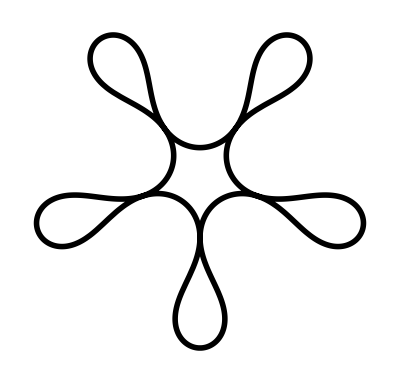

```mathematica
ParametricPlot[{x1,y1},{s,0,2 Pi},PlotStyle->{Thickness[0.01],Black},Axes->False]
```

```mathematica
p3 = 97.02966819277236167141354857142240471929565028591849511365980560123828863522700062034502838691397966753902455391870177330437586`111.37491216594877;
```

```mathematica
Clear[A]
```

```mathematica
delb2 = -((3 (-659178312118679288778285666795520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5-711785812028150808940398849818624000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6-178628702560080535298985238119789363200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7+79760973808648665606204635647064408064000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8+46752657224998506953399325035023302656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9-32830483712136901399924585004193651097600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10-4549153804222410165748005903213649698226176000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-622412904622018757841637011219419538642698240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12+253061052403252947272073286756283021280044646400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+65477852841503675675264692343506920947291521024000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14-8346882267893278537378859080793349588428699729920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-4019615041317392524833231742219983144690759027916800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16+92731590310313048903094593478450400186185696673792000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+177099583249077634834834735556707811030476910200094720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+7133443397590355638452216026775857502814067480749670400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19-6032553033075696621526070748167630661715137530483965952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-552190126165349982919459605634780187139320774915879075840000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21+164120828181034480611840872527424745760403112796763455488000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+23660492747900819272331455986426621035873626014446956576768000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23-3590018167662058087083394961939605505549630143946919877017600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-761997084248711298633864196904174730467668261094534444954419200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25+61436201919316609565423626440951222569170351133815271824818176000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26+20095336402557269056993957881686015555430099443819475169160724480000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27-724806359302479942322558085057387564985909283538620013871523430400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28-451490115626062777862739904987623764561158362941057980091957510144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^29+1658874314852733695507303883990811983840212100156875983176031272960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^30+8841842026011944379444816712290496725775804358612787400316355294003200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^31+199430157528460777000663793930443438114602836900384907590268633481216000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^32-153198577256619372379788953101969168395251013248706443174360583472414720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^33-7006451899090811301180487372384114895444505647657201678945845729925529600000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^34+2373084974327008824652315377844124801211122712921963703098897862167101440000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^35+160951567821047135047548971194530637986898119719230796748983040552982282240000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^36-33113794977603995846905210779104799083625010738000754931260550421897491251200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^37-2991021550155458880183788278843671679991349051316244403059882298374300368896000000000000000000000000000000000000000000000000000000000000000000000000000000 A^38+418569401620639663658524438876996808106634305660272497600100408291057729536000000000000000000000000000000000000000000000000000000000000000000000000000000 A^39+47984987457594636979249963401409208205757397082070906750451948240612540547072000000000000000000000000000000000000000000000000000000000000000000000000000 A^40-4812434093158658359236798911448754738389652457878193523539895599954471371669504000000000000000000000000000000000000000000000000000000000000000000000000 A^41-684881650135172243710179757091634193428140317128348388192950657143602677725265920000000000000000000000000000000000000000000000000000000000000000000000 A^42+50473319606337887449775055031651971976291052275651629936163269985121707875526246400000000000000000000000000000000000000000000000000000000000000000000 A^43+8847022711222793867396325429089700824162577992720279590602929728980218980100734976000000000000000000000000000000000000000000000000000000000000000000 A^44-483842065983438480761943770517634989411729877957477823472827665401331120808153579520000000000000000000000000000000000000000000000000000000000000000 A^45-104584286594801702987243963184010525843250320452310425805023502086691270564052887142400000000000000000000000000000000000000000000000000000000000000 A^46+4244434423250121048675106676385632627666616391722848391050581199155172437156496932864000000000000000000000000000000000000000000000000000000000000 A^47+1140247513570227868925236510515605438085780259788891884981534304836710437370849342259200000000000000000000000000000000000000000000000000000000000 A^48-34102172600818785963123435994981508861593042725147076275027751492338564235389919716966400000000000000000000000000000000000000000000000000000000 A^49-11531476631475652667422468688498316758702637605882524204496592468646114933903018254401536000000000000000000000000000000000000000000000000000000 A^50+251259115602347521594887657043247615246548715909177220230332435086191318792734533432115200000000000000000000000000000000000000000000000000000 A^51+108646427874077908904055172751045510943306897246186364262526876429748787727786132818100224000000000000000000000000000000000000000000000000000 A^52-1703062289416029670327915324740065589929727570137342243086982926679451268479963913219211264000000000000000000000000000000000000000000000000 A^53-956856720319590991103614270703116982423415924685599721427134086829470769654380450858475192320000000000000000000000000000000000000000000000 A^54+10711923686032140131359440075886254698611774863763724579645387723395694806791387116318857625600000000000000000000000000000000000000000000 A^55+7897664804904433304994941575314427540033930022883505070654713151794843877829176190213424152576000000000000000000000000000000000000000000 A^56-63831384724945724788435140615417093107057308267278757715985807293482790051502216291106349383680000000000000000000000000000000000000000 A^57-61209330825397942298448488701994422631630166381420214763425648385241981735483976701827653356748800000000000000000000000000000000000000 A^58+375573069114305327750404724461772853516287971341609300046531461494246074703773908132524632047616000000000000000000000000000000000000 A^59+446090436495049312786249002184362493183828572354213690580904044020358166584550797994109008672194560000000000000000000000000000000000 A^60-2316910329469357513420393596794692966836552676750867943812050824841716173278589477999693861696307200000000000000000000000000000000 A^61-3060129947586540940244013391582749300881820345170048459656888788198386235215356383374713989221056512000000000000000000000000000000 A^62+15669185740037485910807644934819298022944818575581459631848576888516799893224230829498925722139361280000000000000000000000000000 A^63+19770915295365262404382603841312147074768629982024687988970083305821372742066102790466288298188655820800000000000000000000000000 A^64-114649525780277980086620600135369134059364815140864118415151660165135849180744065737063539309340000256000000000000000000000000 A^65-120336347952778791102897200403294491045834032912046917609599001216139150210405416171578591775846333153280000000000000000000000 A^66+857744306945329914401449388521303148879490231709886126978906938439029036332591029514708485035064400281600000000000000000000 A^67+689979366980628977019529382944325706977691147505987822583817540998740778710244302917522309042154187522048000000000000000000 A^68-6224059146625883151553936514980972425801991069367895847791710749925597929787199102049421865494230933176320000000000000000 A^69-3725783688625166858818415099729498224113049289704820904824363428138028781992285986274586662531351330999500800000000000000 A^70+42493993407519608210174340793009993872063555707982656253852186941886727029230811864247056335801638969147392000000000000 A^71+18937004450937340992960994775108314901042771613299829159210230717861778031212701220869256750800279713632747520000000000 A^72-269407935574948809793906654514271475364302736224682159026505237113107600266997480049757174253387091687558348800000000 A^73-90529231001421190329388113029486176306153528737532006818407706235152793989802447488908865994312944372932411392000000 A^74+1579420030395828990083971252823838569309965513275090814464029746128303360670077529046281813840620048034981478400000 A^75+406652606938132884717972580782503840102291153518182776119217020844157602221292036181563412460243796601412046028800 A^76-8559310045810191579022866720821535763918533924072313738542113975775968518086972847336771266287963861579213045760 A^77-1714284699050505606881826243532741187915889502836038141593053884968945561951202852446036392629217590744063148032 A^78+42923033172473278046906191461677033366554788615603639006737526042810953034717852547078515688705482211995942912 A^79+6771932373883997258003968461977271527447600775474959442730774459956579882065010444824719510856404707045277696 A^80-199457227341128190927930187319723157681721404831176263807848181811564233903487174045483992932385738343841792 A^81-25021196703561042057880683563616246351597901710031212678497770990531782231096992918598701081449039377989632 A^82+859930232907984715884891266008183135743204140841303810763287915665242066439731590725033623474755684270080 A^83+86271712021753450893930342420372659507244471403039907280020708868656602881206133860487014134647617486848 A^84-3443138330784328547618633207142451694684278782291226015319273056836311447420029718320497293942660792320 A^85-276771115757843171080858610798006435852401376310556638250010093036510278563616955362966468541886234624 A^86+12811585186305247560036210260340346321877157609107737671958678540347632487154592233857562434649194496 A^87+822989771903561547912515016432328512335011764091007962810460973409168965061305386412369248172113920 A^88-44313979321672483609921940716160917911866137708970904803526516760490964439699605585259041443020800 A^89-2256321159279677622937490913829036386963628356725496674047955482469282592230275581707029284126720 A^90+142480907909815593140019428216887978038585816384590976008991423894279680498859332446326806806528 A^91+5660070873854853887118099315650223165809932480705987800392814027796328737433449594305581678592 A^92-425694841723878737716983659239249748348260361643135219887118175023495529855952543731035406336 A^93-12836925747775061556753115488865149750703106117117137894519299934654126303501107315519520768 A^94+1181061981405831682774375371301356150211987250290832639042925701678186518565450906928676864 A^95+25778037447559154812635359626259005578467365579947391414627249738194795727551267600334848 A^96-3039767532469918978698254774086838853308766113550160461679972712321075910599893877522432 A^97-43905729173300361783111056261316519705813597567482069635684752584016208284052954808320 A^98+7247772074195949861758855143276907269447017064731828443680351123486787441509552619520 A^99+56331698722039570458032666079631666642054437494427920951215296418615153834418241536 A^100-15980477912169645229963339725782403899783107681278521359898439832235584861172137984 A^101-25770189481695435122638145502675714728678112701785932899172974970938716422406144 A^102+32509348553453658651738196546301387815753744188972877850883272620969210257866752 A^103-137044882546481567616670473435782387985768252818911646703685698396249871351808 A^104-60842293142155274480129205708228940533578029655389477630377094755978032709632 A^105+601836266330542059464603840001727046615636774690564640595386333819542962176 A^106+104369330222075220484231036889288082561105387457114340732999295184863756288 A^107-1629926129713202823990702121457157394131864796462244489263042957651476480 A^108-163305394486054427228815234287604075785218966125483182302158183777435648 A^109+3535098215552213013781149811607556166209651565243108446961451801772032 A^110+231536527467665525527579427409579730269240041552289844816384022806528 A^111-6565248936100740953833672291341002162084307552607352416881554227200 A^112-294653497424342634753651832189372370153730591867813700000624410624 A^113+10713353569014650425584867580127338469455020752238552113855070208 A^114+331650493014356182913429617325080805143241751001680813540507648 A^115-15534305660565516886935025154340383546373194444536057096568832 A^116-321778858488780491333397028389744340640730930453600886849536 A^117+20101990228893647518325938999755516473352447622449448615936 A^118+254936963390199229433526393955483370012833467028287258624 A^119-23221978441430739753084958442079149268133340866691465216 A^120-140256857188218342154075487941048791511394500242046976 A^121+23883602582800552356257725560161753903917535877660672 A^122+6415564851797159720203097038400755572705528381440 A^123-21749001715123913793174555821033354146795799707648 A^124+108968280104660063776443989413630195002639384576 A^125+17381130451651313771496628339244758175357861888 A^126-176188571454468140093972821348444419018194944 A^127-12027000211350900700290387030264164521082880 A^128+186581741116605984191249248687337368453120 A^129+7054489727314178066022661268802599649280 A^130-153726527378344047591096127855503605760 A^131-3380934564744748626879854281076768768 A^132+102778650430428732389621569296596992 A^133+1224587876973566965912384144801792 A^134-56124296990368830063704919162880 A^135-258147151448547878718569160704 A^136+24727153956906074361474334720 A^137-32688014197299320159864832 A^138-8518410596682366223313920 A^139+57645161814580520325120 A^140+2145581838986791348480 A^141-27752282792950472704 A^142-329070225802178624 A^143+7891337452498464 A^144+5099020056480 A^145-1292292192728 A^146+9400533332 A^147+75220860 A^148-1492475 A^149+6144 A^150+10 A^151))/(16 (-200-4 A+A^2)^3 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13)^2 (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116)));
```

```mathematica
delm2 := -((3 (33473898662276682633272319016960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+30748945047801703572164366775091200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+4559420315666821243224827415337369600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-4242628166693187931766610294745333760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-1502794507647615231612943003135802081280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+207896710948504877832817257401070649344000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+159593271042905682114826154600428151504896000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11+1798582783622192374486737831448707564830720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-10189629389351797920289508924771015994638336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13-906573920483594725007771651878289703211892736000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+457440138417698354456988803168605527002442629120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15+69063812142023104041441917777511211666650850918400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-15432048740716264092456105542608875850285954629632000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17-3359075717963158291751215143645998449320116795473920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+401299942971364034518856107993926580974352471162880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+124029532167350811823322615786037836688671772359262208000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-7935918732242945755259182340922054899258864949170012160000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^21-3724512158293759828124711371270040582264138398297384550400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^22+107426894397885576905572141903204847486601187827153633280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^23+94479153935774817300934869219402514825290141452555801067520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^24-404214281750165181118253117969399485103790884566789731123200000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^25-2074977576211301289453115491802329490452471916201337535070208000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^26-28987955743622528825499933171324769858946259869184503788339200000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^27+40153539992350482132659200458562878843898140407227139383676108800000000000000000000000000000000000000000000000000000000000000000000000000000000 A^28+1125293572660572042849277615382380452142605834604865731621289984000000000000000000000000000000000000000000000000000000000000000000000000000000 A^29-693812353314175173238030834651534544577788367388418246516576092160000000000000000000000000000000000000000000000000000000000000000000000000000 A^30-27078822510395631902700763284783330989623043988214306276913866342400000000000000000000000000000000000000000000000000000000000000000000000000 A^31+10817329277586667020071586735469853602557410193737001951122583191552000000000000000000000000000000000000000000000000000000000000000000000000 A^32+515196517188395359520988474729791260924223152477601029347956165181440000000000000000000000000000000000000000000000000000000000000000000000 A^33-153474688310499525320359430328866174027099406566356192616894855276134400000000000000000000000000000000000000000000000000000000000000000000 A^34-8316798114068380032204903353931429386150553063491466587190637306576896000000000000000000000000000000000000000000000000000000000000000000 A^35+1995280821269615709490783468588050291296052150971825372432794095011758080000000000000000000000000000000000000000000000000000000000000000 A^36+117601096231934487441564923350319495251814416087160488913326324314433126400000000000000000000000000000000000000000000000000000000000000 A^37-23905225906619970814787336736807176759557224623943122049891208712723365888000000000000000000000000000000000000000000000000000000000000 A^38-1482610102597493450118404080795950785973775914772296951405387856428463554560000000000000000000000000000000000000000000000000000000000 A^39+265163378292365728852845397918378072102950271949777140859106549587061296332800000000000000000000000000000000000000000000000000000000 A^40+16850360905831369225557335387083368890674279416593440787048198804712150007808000000000000000000000000000000000000000000000000000000 A^41-2733194901077593048951110682121093146415505036412440645079160717648814019706880000000000000000000000000000000000000000000000000000 A^42-173927693163838245824137638333519812781097381534507240077631969517236211259801600000000000000000000000000000000000000000000000000 A^43+26254604483964625875824645562209671735028347840518824049006134673886618337673216000000000000000000000000000000000000000000000000 A^44+1638758575810361120775824221791186039109862660568917701678116389440715814841876480000000000000000000000000000000000000000000000 A^45-235524145479629451010592178013392836528984708310794153242581762126758784334508851200000000000000000000000000000000000000000000 A^46-14143585721740545763203427096504374697514856256559795022210565589147397774769127424000000000000000000000000000000000000000000 A^47+1976026380582727009722525203780321807607918079097165921581091437728325490497101496320000000000000000000000000000000000000000 A^48+112066918243536614571520627345887682153062702605248881101540970386020297257274625228800000000000000000000000000000000000000 A^49-15519057171601893477344454939459643368230350743566637456352483629731022757396448542720000000000000000000000000000000000000 A^50-816182937684336292393158564883677506350298862060399754134901717543562497140872624209920000000000000000000000000000000000 A^51+114140014619312430420252875568711383840647729349603360957090115165578464180977820657254400000000000000000000000000000000 A^52+5464820166103233580207781284405476155208604337260657738700851370973183280557087562661888000000000000000000000000000000 A^53-786196798739402185007889342116807250220934900114730391846738910732387903481515086257848320000000000000000000000000000 A^54-33609817540006755786394887955369269692150147432768479615420678346493855368273477364193689600000000000000000000000000 A^55+5070344601865993058672782422704978514720182118503604510836532672540781206785744344654544896000000000000000000000000 A^56+189461859410318669016614359630594425837778736558645200821127650124799001264352702160888135680000000000000000000000 A^57-30601986661296622478180839768627896462338555475451044181076977129626000334179247185426435276800000000000000000000 A^58-975072930462068023545838409572260808883232109068892715692890317221206254709547855571899645952000000000000000000 A^59+172736880024833902130351126136632768193059136824905670027334276628587531878524920184897305313280000000000000000 A^60+4551047516259617000386029690754965004773276918846762541235108652518501559067345830068950663168000000000000000 A^61-911176903427362827195167791899784059982275841111301965291377161893003092362177107660212753399808000000000000 A^62-19042882789292908781534183387467769247676368979775131847940933568764187469520308541423173500928000000000000 A^63+4487609416305090619908404855931006499113487571099219283131396030089318740267562444446149708978585600000000 A^64+69912423389390191549851752515469858334224701233836338113174938700588329238290689772424645799051264000000 A^65-20615644647154236639939688776363874106300442136134428907423068619069061803962633417547177334071623680000 A^66-214921306130890774650362907380575570647790507393729171209549380139471219989525913632378065636871372800 A^67+88245476010227858192956020058000959523138407966569749766712474380008213518139847806496842333485531136 A^68+482006392812072111792068897318088518054097083774534603100288405135161844989179906128885967698788352 A^69-351579156685233078122648377111424814913641357471293465185877010055029362553302343482941369883820032 A^70-247634681528718007260184444475761129309905241533600951235411862157891121996043748955619330097152 A^71+1302266762326793642238457518957313261630719455899847284682757334758947767709155561376547958947840 A^72-4998553753740982528790912773543619810859917163879320764280038970555443290196957617979643658240 A^73-4479655166113333077635134101172769208833802422731814018776765240408075079377019624843194138624 A^74+36531908862607613102466715101034032713688966090250492429269932717271984942266880162980167680 A^75+14296378563182026108726943374638147830714655368041633180748487728558690546992131958613475328 A^76-174794267617802481180008340708885494477070964370598126648151970360825130137634448934436864 A^77-42298391951284520700220142387334373629309011775039286987371911801554596767656888357617664 A^78+677406784794587886569482614216920003388695533539456057103336324433017829717013566586880 A^79+115993320120386967030359828304230516388792140111975646526760276109845894172071147077632 A^80-2256186382149675488277064759425027407027294687233153012517087742457805685835536793600 A^81-295006294489614926539460391922739702141697190260272395170343490079536439275083005952 A^82+6612504218940250804851638305644338622024829902808224879911458585605405729489944576 A^83+697317763002691569913833198283243168221947650177285773402199614051568649546760192 A^84-17234206959184892230686433943891924382737651449603376999707612921818227440353280 A^85-1538554664021034341633192287633692116347449389529533028680533370029369404162048 A^86+40118309927013009674127419968744287394262652071020576727010288199401346170880 A^87+3192101881986650109202795666349905543071839927396476226688714542360087756800 A^88-83496585995443074196183282215038516364769544309769693463450080179742834688 A^89-6294516068472014592270976188755174269536976468371842733707173164377702400 A^90+155277831288819317062051706585695155927970439078748571438779140736548864 A^91+11948476024071655706864281230614965968753204769658100527944512433029120 A^92-257960096853236253659723533355794536726363670319227698680782611546112 A^93-22080010284765496866791970177297316423419916399401027624977402167296 A^94+384393934483644994676750191335222962618588538658926139738953875456 A^95+39904427684365414850016755248341942904746006952234510928318562304 A^96-522938133486883320558529337887710378237751403346578053556862976 A^97-70166264367157577500450749921519887405731332467840921651642368 A^98+681562731246772180622460688546837793148170363299907846012928 A^99+118426902974824547054280437944629876047390477326877687021568 A^100-928895503272658623195508139363621083447024135690145234944 A^101-188586495804640621355947139424340778921573027743654739968 A^102+1424630398211938701691451071928295781227650647641292800 A^103+278633238307463139866666581826692005565943463762984960 A^104-2389602081539823522296403455969813610711643798372352 A^105-376440484627022606821578643942114739472246027321344 A^106+3980613898346712304357686814772498271882461577216 A^107+459201329442547918238483021978292424250081935360 A^108-6105755335757199662718037167525485481084059648 A^109-499698137017466368126381896271802387111346176 A^110+8307037411528051903414793745461783241424896 A^111+478697923511237775724314856461877009973248 A^112-9858407141686628906684118218693802983424 A^113-397052011974169054728264720908119179264 A^114+10106277885612598966446527907710107648 A^115+278489049118641528452878039631527936 A^116-8866972748865503623792595890470912 A^117-158896562491865093234232467324928 A^118+6579741703727577953415976599552 A^119+68100913526667786922008674304 A^120-4061015849984411489971437568 A^121-16872243880910689805881344 A^122+2033346481823815907820544 A^123-2431860249779515760640 A^124-792743117467205680128 A^125+4948061861670212864 A^126+222135977683739584 A^127-2652768225534720 A^128-35732215444064 A^129+800449362480 A^130-655680372 A^131-122049808 A^132+1630552 A^133+242 A^134-249 A^135+2 A^136))/(16 (-200-4 A+A^2)^2 (-51200000000000000-5632000000000000 A+1262080000000000 A^2+123008000000000 A^3-14450432000000 A^4-1097571840000 A^5+97097600000 A^6+4951693568 A^7-390280320 A^8-11005696 A^9+859008 A^10+8548 A^11-788 A^12+3 A^13) (302231454903657293676544000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+272008309413291564308889600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A+46093319187356773858609725440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^2-30081157152851991171085159628800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^3-11546224282895327860134370082816000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^4+981142609828723818987618062827520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^5+1010620512944697605592384814238924800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^6+41805821257879317744049458828541952000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^7-53326466993351583716229380552513290240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^8-6091524385073594644285814496269277593600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^9+1960379596336514041110851010337609613312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^10+353493578133882202178469928357636037672960000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^11-53073521206152960533807308397085057875968000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^12-13975906791108825490522217656586873379749888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^13+1060370205137452721785896584719505736985477120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^14+427056806925325008430852352298705973118238720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^15-14249032136781215689731841060746364605603774464000000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^16-10684939802378885654752819767994403770171738030080000000000000000000000000000000000000000000000000000000000000000000000000000000000 A^17+56827249055525191872631117879682145272502367027200000000000000000000000000000000000000000000000000000000000000000000000000000000 A^18+226480386591167165551133774597881097897911374577664000000000000000000000000000000000000000000000000000000000000000000000000000000 A^19+3349106944261303328470793430745454069787582204477440000000000000000000000000000000000000000000000000000000000000000000000000000 A^20-4161426800505224971246749515218724823587258283694489600000000000000000000000000000000000000000000000000000000000000000000000000 A^21-124452827894490298725565926510691725612119528661057536000000000000000000000000000000000000000000000000000000000000000000000000 A^22+67408306902658544542575836004494988197257413580742983680000000000000000000000000000000000000000000000000000000000000000000000 A^23+2798700915012983576533551007476317455975910535649348812800000000000000000000000000000000000000000000000000000000000000000000 A^24-975164122633367636844570019672658794098864292511961055232000000000000000000000000000000000000000000000000000000000000000000 A^25-49151527703303495206891350019936678884455594202082542878720000000000000000000000000000000000000000000000000000000000000000 A^26+12729755866327136031311697977991974688005785216318859273830400000000000000000000000000000000000000000000000000000000000000 A^27+725284647968578056382490430155477184743908648173067057496064000000000000000000000000000000000000000000000000000000000000 A^28-151205368243639674060871447210484561020858181786206066568069120000000000000000000000000000000000000000000000000000000000 A^29-9293261476940559525853612846718202800219177663399214574469120000000000000000000000000000000000000000000000000000000000 A^30+1645330846040845975966716526048863833253056363418988165155782656000000000000000000000000000000000000000000000000000000 A^31+105301417168818265468690538127909327011991416490509251376935075840000000000000000000000000000000000000000000000000000 A^32-16489870436204021263309469496811526083686540381002739581515621990400000000000000000000000000000000000000000000000000 A^33-1067097523061485748132572196427779838063865317441059614053183258624000000000000000000000000000000000000000000000000 A^34+152850537977199857065937748207700475990384919778700903429471113052160000000000000000000000000000000000000000000000 A^35+9742496330980349280121561390044924013636915145496201953298639486976000000000000000000000000000000000000000000000 A^36-1314409597951196390719677459242161629870401084240785746692104349810688000000000000000000000000000000000000000000 A^37-80522626800046727109754298429820115173580178615106155294296834404515840000000000000000000000000000000000000000 A^38+10507766861356864714478429118327580859041699858790576448902464914902220800000000000000000000000000000000000000 A^39+604246649961037794193966249449519816090707924515244401237035102987354112000000000000000000000000000000000000 A^40-78188208515456492764183362688707346323996091691219165450686333435594670080000000000000000000000000000000000 A^41-4122244245157016816218144586288386626337933118422715880558174098497627750400000000000000000000000000000000 A^42+541822160133136951130977889761726362880299237455342501799669656230587006976000000000000000000000000000000 A^43+25560474484191234246190264498578088140409762952114948724475659153395259801600000000000000000000000000000 A^44-3496670304400852139205704582096982730099031390683496497844062675673155423436800000000000000000000000000 A^45-143754204544351676471650259674057133450254940571065419725524018306231759273984000000000000000000000000 A^46+21006691273103164239385015246987680647982709877103711117211694824576877141688320000000000000000000000 A^47+729965576723245070741949632019124395728588807163548992598860769442250266509312000000000000000000000 A^48-117398848742074207496783774898255822292682705110598767449787035407856505714638848000000000000000000 A^49-3317976227616779895351941241174008217738258009980243969078986609937091080256225280000000000000000 A^50+609796660167413878849773357477534044970947285273783056176188513334248164527859302400000000000000 A^51+13281695646683404665277396375947879227104950957966687694156361046608122942784012288000000000000 A^52-2940841958161004778241242205214906135620043437772101207011208501389555030142945853440000000000 A^53-45253099408470513656047318829496604489775798629165783053878629298059528729431061299200000000 A^54+13153024948217722188421415876043453516408931900338845189651143981357541361623762993152000000 A^55+120058382030700922897977569156847479731442357709081037627529183971240698102581622210560000 A^56-54488180168400143579115902616515760395066533547450865778883600213357753220987250278400000 A^57-163919106566248617454548042594676177632034330133409159231539970026854641181651969769472 A^58+208786755511689154622165437316204630340268531875309306050823415548807741756453190369280 A^59-625226486961487058915811326934836206820269818845187330463024437052354776366577614848 A^60-738852032437333964967762712259755920943165630984057272641030581638797285820672770048 A^61+6601443653933451217802321221638388873884004938935373004324707691202467870929846272 A^62+2410437253141196544487506543230759461651864394099897719922150187148052155187855360 A^63-35909229225056180975671122418444635536106769267549175398460382545448425735847936 A^64-7234422167106186218116937952932720416556777961779614990237253723005108015333376 A^65+151966759675806345453278589522440573940631845390128751466073792444105794519040 A^66+19923003519543635956930472368294134655550974395867495332744219125142748397568 A^67-546642433700590133491537002123644897257874639029061702290852665720406278144 A^68-50176458761060737209125824837993732830220147096734886641852600022470754304 A^69+1728736221797142717563643348621865759034709218323682722251234523738013696 A^70+115049514387472879968528023813350833984702225305189073862191043819077632 A^71-4884594735469563896823190908468336942637288681491786834577233847255040 A^72-238626473115349601977990450409072049507469378136186528987201469939712 A^73+12437402077912425299430715060761014078335410579799473891706719436800 A^74+443332630741678530243802103240569685418244334466485251148869533696 A^75-28673049248938197939254964075143002442606105972758119804068429824 A^76-725678167519493367786926297428113939746810129714596632374280192 A^77+59992616517842512361882780411136187303049571366618318197751808 A^78+1013848621843483796719197481713863121408158393062326343303168 A^79-114011166932055985300740998262419092047730015234084606836736 A^80-1120045639338132096368769652139485727185585470527789596672 A^81+196707144031874500541911282021916732340674294513139712000 A^82+724362375221721637474011648906171102769111629807222784 A^83-307617999538038744909178417120239756015243117927071744 A^84+558054329157309457048631643067831459309887051268096 A^85+434807156386923123387328420484094874971832737333248 A^86-2997457880675782487004781821328820511553152352256 A^87-553155963131552976374599598890509458258161303552 A^88+6504370950705254825021367922518311047618625536 A^89+629622332568618122627323100686535547619901440 A^90-10462448843984464569702286457547574241918976 A^91-635894995465205280321309730065174799319040 A^92+13814539279312513690789976632052813922304 A^93+563201333415403132793549254740411940864 A^94-15464072496485265069990782047384240128 A^95-429973732185341894484320654918811648 A^96+14823220002524831808746525668147200 A^97+275388151494425954144923277066240 A^98-12161238264714254011387721023488 A^99-140885211256971343387966603264 A^100+8477715836200989637627142144 A^101+51211876173721471246508032 A^102-4956345088816721044936704 A^103-7398032758833454470144 A^104+2382521099003112670976 A^105-5595258916745789824 A^106-914256749213146880 A^107+5196563382936736 A^108+267352905322480 A^109-2316199864600 A^110-55048907232 A^111+627771162 A^112+6859422 A^113-96198 A^114-357 A^115+6 A^116)))
```

```mathematica
b3 = b2 + delb2;
```

```mathematica
m3 = m2 + delm2;
```

```mathematica
p3 = m3 + b3 -1;
```

General::munfl: 0.000163429^82 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000163429^83 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000163429^84 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

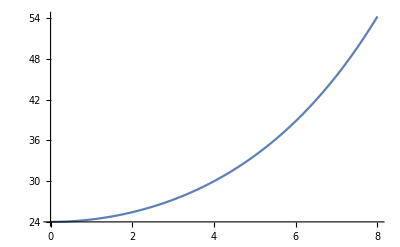

```mathematica
Plot[p3,{A,0,8}]
```

```mathematica
A:=10.9999999341124591211266462595651516565147495151515232333333331111111111111141246167975798717527573727375273175797571251725721791971719775
```

```mathematica
p3
```

97.0296681927723616714135485714224047192956502859184951136598056012382886352270006203450283869139796675390245539

```mathematica
N[3761022780508335673293603907535309296428433609536546311633163060675757/47282261052426357688856982804833165055751312004966033463247140815838]
```

79.5441

```mathematica
N[3761022780508335673293603907535309296428433609536546311633163060675757/47282261052426357688856982804833165055751312004966033463247140815838]
```

79.5441